```mathematica
Get["/Volumes/GoogleDrive/Il mio Drive/Varie/Mathematica/LogLogTicks.m"]//Quiet;
```

```mathematica
DGreen=Darker@Green;
```

# Initializations

### SM

Parameters

```mathematica
vev=174.;MZ=91.187;MW=80.38;ccW=MW^2/MZ^2;ssW=1-ccW;MPl=1.221 10^19;
g2MZ=Sqrt[2]MW/vev;α2MZ=g2MZ^2/(4π);
gYMZ=g2MZ Sqrt[ssW/ccW];αYMZ=gYMZ^2/(4π);
Tc=155.;
α3MZ=0.118;g3MZ=Sqrt[4π α3MZ];
```

Thermal masses

```mathematica
Clear[Rvev,CalcolaMT];
sQ[x_]:=If[x>0,x^2,0];Rvev[T_]:=Re[Sqrt[1-T^2/Tc^2]];vevT[T_]:=vev*Rvev[T];
(* CalcolaMT:=(Clear[MWT,root,MZT,MγT,ssWT,ΔMT,MgT];
MWT=Sqrt[MW^2 Rvev[T]^2+11/6 g2MZ^2 T^2];
root=√(121 (g2MZ^2-gYMZ^2)^2 T^4+66 (g2MZ^2-gYMZ^2)^2 T^2 vevT[T]^2+9 (g2MZ^2+gYMZ^2)^2 vevT[T]^4);MZT=Sqrt[1/12 ((g2MZ^2+gYMZ^2) (11 T^2+3 vevT[T]^2)+root)];
MγT=Sqrt[1/12 ((g2MZ^2+gYMZ^2) (11 T^2+3 vevT[T]^2)-root)];
       ssWT=1/2-((g2MZ^2-gYMZ^2) (11 T^2+3 vevT[T]^2))/(2 root); 
ΔMT=164.80/161.17 α2MZ/2(ssWT (MZT-MγT)+(MWT-MZT));
MgT=Sqrt[2 g3MZ^2 T^2];); *)
```

```mathematica
Clear[ssWT,MWT,MZT,MγT,MgT];
MgT[T_]:=Sqrt[2]g3MZ T;
MWT[T_]:=Sqrt[MW^2 Rvev[T]^2+11/6 g2MZ^2 T^2];
root[T_]:=√(121 (g2MZ^2-gYMZ^2)^2 T^4+66 (g2MZ^2-gYMZ^2)^2 T^2 vevT[T]^2+9 (g2MZ^2+gYMZ^2)^2 vevT[T]^4);
MZT[T_]:=Sqrt[1/12 ((g2MZ^2+gYMZ^2) (11 T^2+3 vevT[T]^2)+root[T])];
MγT[T_]:=Sqrt[1/12 ((g2MZ^2+gYMZ^2) (11 T^2+3 vevT[T]^2)-root[T])];
ssWT[T_]:=1/2-((g2MZ^2-gYMZ^2) (11 T^2+3 vevT[T]^2))/(2 root[T]); (* ssWT[0] = ssW;  ssWT[T>Tc] = 0 *)
ccWT[T_]:=1-ssWT[T];
```

```mathematica
ΔMT[T_]:=164.80/161.17 α2MZ/2(ssWT[T] (MZT[T]-MγT[T])+(MWT[T]-MZT[T]));
```

### Running couplings

Here t=2 Log[μ/MZ]/(4π)^2.

```mathematica
Clear[t,λJ,loop,ggt,λ,gg1,gg2,gg3];converti={λJ->6 λ[t],gt->Sqrt[ggt[t]],g3->Sqrt[gg3[t]],g2->Sqrt[gg2[t]],gY->Sqrt[3 gg1[t]/5],gτ->Sqrt[ggτ[t]]};
βλ1=4 λJ^2 + 12 λJ gt^2 - 36 gt^4-9λJ g2^2 - 3 λJ gY^2+9/4 gY^4+9/2 g2^2 gY^2+27/4 g2^4;
βλ2=-26/3 λJ^3-24 λJ^2 gt^2+6 λJ^2(3 g2^2+gY^2)-3λJ gt^4+80λJ g3^2 gt^2+
45/2 λJ gY^2 gt^2+85/6 λJ gY^2 gt^2-73/8 λJ gY^4+39/4 λJ g2^2 gY^2+629/24 λJ gY^4+
180 gt^6-192 gt^4 g3^2-16 gt^4 gY^2-27/2 gt^2 g2^4+63 gt^2 g2^2 gY^2-
57/2 gt^2 gY^4+915/8 g2^6-289/8 g2^4 gY^2-559/8 g2^2 gY^4-379/8 gY^6;
βτ1=gτ(-15/4 gY^2-9/4 g2^2+3 gt^2);
βt1=9/2 gt^3-8 g3^2 gt-9/4 g2^2 gt-17/12 gY^2 gt;
βt2=gt(-12 gt^4+gt^2(131/16 gY^2+225/16 g2^2+36 g3^2-2λJ)+1187/216 gY^4-
3/4 g2^2 gY^2+19/9 gY^2 g3^2-23/4 g2^4+9 g2^2 g3^2-108 g3^4+λJ^2/6);
βmm=mm(2 λJ+6gt^2-9/2 g2^2-3/2gY^2)/.converti;
βλ=Collect[Expand[(βλ1+loop  βλ2)/12/.converti],{loop,gg1},Expand];
βt=Collect[Expand[(βt1+loop  βt2) gt/.converti],{loop,gg1},Expand];
βτ=Collect[Expand[(βτ1) gτ/.converti],{loop,gg1},Expand];
β3=Collect[Expand[(-7 g3^3+loop  g3^3(11/6 gY^2+9/2 g2^2-26 g3^2-2 gt^2)) g3/.converti],{loop},Simplify];
β2=Collect[Expand[(-19/6 g2^3+loop  g2^3(3/2 gY^2+35/6 g2^2+12 g3^2-3/2 gt^2)) g2/.converti],{loop},Simplify];
β1=Collect[Expand[5/3(41/6 gY^3+loop  gY^3(199/18 gY^2+9/2 g2^2+44/3 g3^2-17/6 gt^2)) gY/.converti],{loop},Simplify];
```

```mathematica
MZ=91.187;mh=115;Mt=172;GF=1.16639 10^-5;vev=2^(-3/4)GF^(-1/2);VEV=Sqrt[2]vev;loop=1/N[4π]^2;mτ=1.777;
t[ϕ_]:=(τ=2 Log[ϕ/MZ]/(4π)^2;If[τ<tZ,τ=tZ];If[τ>tmax,0,τ]);
t1[ϕ_]:=2 Log[ϕ/MZ]/(4π)^2;
qu=2/3;αemZ=1/128.9;ss=0.231;cc=1-ss;
ggiZ={gg1Z,gg2Z,gg3Z}=N[4π{5/3 αemZ/cc,αemZ/ss,0.1184}];μ0=MZ;
λZ=mh^2/(2 vev)^2;gg3Mt=gg3Z-0.1;α3Mt=gg3Mt/(4π);ggtZ0=(Mt/vev)^2;
mtMZ=Mt/(1+α3Mt/(4π)(16/3-8Log[Mt/μ0])+(16.11-5*1.04)(α3Mt/π)^2-1/(4π)^2(λZ/4+ggtZ0(13/8+3/2 Log[Mt/mh]-9/2 Log[Mt/μ0])));ggtZ=(mtMZ/vev)^2;
```

```mathematica
RGE2loop:=(sol = NDSolve[{
gg1'[t]==Evaluate[β1],gg2'[t]==Evaluate[β2],gg3'[t]==Evaluate[β3],
ggt'[t] == Evaluate[βt],
λ'[t] == Evaluate[βλ],
ggt[t0] == ggtμ, λ[t0] == λμ,gg1[t0]==gg1μ,gg2[t0]==gg2μ,gg3[t0]==gg3μ}, {gg1,gg2,gg3,ggt, λ}, {t, t0, tmax}];)
```

Funzione di loop per la correzione a λ (da Sirlin Zucchini).
In δtEW  tengo solo la parte logaritmica della correzione EM perchè il resto è già incluso nella approssimazione numerica (da Hempfling Kniehl)
Poi V'' andrebbe convertito nella massa di polo dell'higgs, ma questa e'una piccola correzione. 
La correzione di QCD a NNLO a mt e'valida per mt(μ = mt)

```mathematica
Zloop[z_]:=(AA=Sqrt[Abs[1-4z]];If[z>1/4,2 AA ArcTan[1/AA],AA Log[(1+AA)/(1-AA)]]);
```

```mathematica
CalcolaRGE[mhx_,mtopx_]:=(Clear[gHS,gS,mm,MM,λ,gg1,gg2,gg3,ggt];mh=mhx;Mt=mtopx;μ0=Mt;t0=t[μ0];
λ0=mh^2/(2 vev)^2;gg3Mt=gg3Z-0.1;α3Mt=gg3Mt/(4π);ggtZ0=(Mt/vev)^2;r=mh^2/(4 Mt^2);ξ=(mh/MZ)^2;
δtQCD=α3Mt/(4π)(8Log[Mt/μ0]-16/3)-(16.11-5*1.04)(α3Mt/π)^2;
δtEW=qu^2 αemZ/(4π) (6Log[Mt/μ0]-4*0)+(GF Mt^2)/(8 π^2 Sqrt[2])(-9 Log[Mt/μ0]+11/2-r+2r(2r-3)Log[4r]-8 r^2(1/r-1)^(3/2)ArcCos[Sqrt[r]])+10^(-3)(-6.9 +1.73 Log[mhx/300.]-5.82 Log[Mt/175.]);
Zξ=Zloop[1/ξ];Zcξ=Zloop[cc/ξ];ZZξ=Zloop[Mt^2/(MZ^2 ξ)];
f1=12 Log[μ0/mh]+3/2 Log[ξ]-Zξ/2-Zcξ-Log[cc]+9/2(25/9-Sqrt[1/3]π);
f0=-12Log[μ0/MZ](1+2cc-2 Mt^2/MZ^2)+(3cc ξ)/(ξ-cc)Log[ξ/cc]+2Zξ+4cc Zcξ+3cc Log[cc]/ss+12 cc Log[cc]-15/2(1+2cc)-3 Mt^2/MZ^2(2 ZZξ+4 Log[Mt^2/MZ^2]-5);
f3=12 Log[μ0/MZ](1+2 cc^2-4 Mt^4/MZ^4)-6Zξ-12 cc^2 Zcξ-12 cc^2 Log[cc]+8(1+2 cc^2)+24 Mt^4/MZ^4(Log[Mt^2/MZ^2]-2+ZZξ);
δh = (GF MZ^2)/(8 π^2 Sqrt[2])(ξ f1+f0+f3/ξ);
mtμ=Mt/(1-δtQCD-δtEW);
ggtμ=(mtμ/vev)^2;λμ=λ0 (1+δh);
ggiμ={gg1μ,gg2μ,gg3μ}={gg1Z,gg2Z,gg3Z}/(1-{41/10,-19/6,-7} ggiZ t[μ0]);RGE2loop;);
```

```mathematica
gg3Z=N[4π 0.118];tmax=0.5;CalcolaRGE[115,175];
Clear[ggt];RGE2loop;
dash=Dashing[{0.01,0.01}];{gg1s,gg2s,gg3s,ggts,λs}={sol⟦1,1,2⟧,sol⟦1,2,2⟧,sol⟦1,3,2⟧,sol⟦1,4,2⟧,sol⟦1,5,2⟧};
sPlot[{gg3s[t[10^μ]],gg2s[t[10^μ]], gg1s[t[10^μ]],ggts[t[10^μ]],λs[t[10^μ]]},{μ,Log[10,μ0],19.},Frame->True,PlotStyle->{dash,dash,dash,Hue[0.5],Hue[1]},
	PlotRange->{{1.99,20},{-0.201,1}},
FrameLabel->{"RGE scale in GeV",""}];
```

Final result: g2 e gY in funzione dell'energia

```mathematica
g3I=Interpolation[Table[{En=10^lE,If[En>μ0,Sqrt[gg3s[t[En]]],Sqrt[gg3s[t0]]]},{lE,-3,9,0.05}]];
g2I=Interpolation[Table[{En=10^lE,If[En>μ0,Sqrt[gg2s[t[En]]],Sqrt[gg2s[t0]]]},{lE,-3,9,0.05}]];
gYI=Interpolation[Table[{En=10^lE,If[En>μ0,Sqrt[3/5  gg1s[t[En]]],Sqrt[3/5  gg1s[t0]]]},{lE,-3,9,0.05}]];
```

```mathematica
Calcolaα3Mt:=(nf=5;ζ3=Zeta[3.];
b0QCD=(33-2nf)/(12π);
b1QCD=(153-19nf)/(24 π^2);
b2QCD=(2857-5033 nf/9+325 nf^2/27)/(128 π^3);
b3QCD=(149753/6+3564 ζ3-(1078361/162+6508/27 ζ3)nf+(50065/162+6472/81 ζ3)nf^2+1093/729 nf^3)/(256 π^4);
α3Mt5=NDSolve[{αs'[t]==-2(b0QCD  αs[t]^2+b1QCD  αs[t]^3+b2QCD αs[t]^4+b3QCD αs[t]^5)+((11 α1MZ+45 α2MZ) αs[t]^2)/(80 π^2),αs[0]==α3MZ},{αs},{t,0,Log[Mt/MZ]}]⟦1,1,2⟧[Log[Mt/MZ]];
C2=7/(24 π^2);C3=(5.32389-5)/π^2;
α3Mt=α3Mt5+C2 α3Mt5^2+C3 α3Mt5^3;
gg3μ=gg3Mt=4π α3Mt;gg3Z=4π α3MZ;g3Mt=Sqrt[gg3Mt];
(*Mt=173.2;*)
α1MZ=1/128;
α3Runs[Mscale_]:=NDSolve[{αs'[t]==-2(b0QCD  αs[t]^2+b1QCD  αs[t]^3+b2QCD αs[t]^4+b3QCD αs[t]^5)+((11 α1MZ+45 α2MZ) αs[t]^2)/(80 π^2),αs[0]==α3MZ},{αs},{t,0,Log[Mscale/MZ]}]⟦1,1,2⟧[Log[Mscale/MZ]];
Clear[α3,α3Calc];
α3Calc[M_]:=α3Runs[M]+C2 α3Runs[M]^2+C3 α3Runs[M]^3;
α3=Interpolation[Table[{10^lM,α3Calc[10^lM]},{lM,-0.1,4,0.01}]]

);
```

### Cosmological functions

geffSM: con FD/BE, senza correzioni radiative

ρ, n, s[g,m,T] per un fermione

lmT=Log[m/T]
e=E/m

lρFeq e le seguenti due funzioni interpolano (la parte che viene interpolata è quella tra le prime due parentesi graffe) “lmT” e le integrazioni numeriche di ρ, n, s nell’intervallo m/Exp5<T<m*Exp5 (cioè qundo il fermione nel limbo tra rgime relativistico e non relativistico)

ρFeq e le seguenti due funzioni definiscono ρ, n, s per tutti i valori di T

```mathematica
Clear[ρFeq,nFeq,sFeq];Exp5=Exp[5.];
lρFeq=Interpolation[Table[mT=Exp[lmT];{lmT,Log[1/(2 π^2)NIntegrate[Sqrt[e^2-1]/(Exp[e mT]+1)e^2,{e,1,1+20/mT}]]},{lmT,-5,5,0.1}],InterpolationOrder->2];
lnFeq=Interpolation[Table[mT=Exp[lmT];{lmT,Log[1/(2 π^2)NIntegrate[Sqrt[e^2-1]/(Exp[e mT]+1)e,{e,1,1+20/mT}]]},{lmT,-5,5,0.02}],InterpolationOrder->3];
lsFeq=Interpolation[Table[mT=Exp[lmT];{lmT,Log[1/(6 π^2)NIntegrate[Sqrt[e^2-1]/(Exp[e mT]+1)(4 e^2-1),{e,1,1+20/mT}]]},{lmT,-5,5,0.1}],InterpolationOrder->2];  
ρFeq[m_?NumberQ,T_?NumberQ]:=Which[T>Exp5 m,(7 π^2)/240 T^4,T<m/Exp5,m((m T)/(2π))^(3/2)Exp[-m/T],True, m^4 Exp[lρFeq[Log[m/T]]]];
nFeq[m_?NumberQ,T_?NumberQ]:=Which[T>Exp5 m,3/4 Zeta[3]/π^2 T^3,T<m/Exp5, ((m T)/(2π))^(3/2)Exp[-m/T](1+(15 T)/(8 m)),True, m^3 Exp[lnFeq[Log[m/T]]]];
sFeq[m_?NumberQ,T_?NumberQ]:=Which[T>Exp5 m,4/3 7/8 π^2/30 T^3,T<m/Exp5, (m+T)/T ((m T)/(2π))^(3/2)Exp[-m/T],True, m^4/T Exp[lsFeq[Log[m/T]]]];
```

Ripete lo stesso procedimento per i bosoni

ρ, n, s[g,m,T] per un bosone

```mathematica
Clear[ρBeq,nBeq,sBeq];
lρBeq=Interpolation[Table[mT=Exp[lmT];{lmT,Log[1/(2 π^2)NIntegrate[Sqrt[e^2-1]/(Exp[e mT]-1)e^2,{e,1,1+20/mT}]]},{lmT,-5,5,0.1}],InterpolationOrder->2];
lnBeq=Interpolation[Table[mT=Exp[lmT];{lmT,Log[1/(2 π^2)NIntegrate[Sqrt[e^2-1]/(Exp[e mT]-1)e,{e,1,1+20/mT}]]},{lmT,-5,5,0.1}],InterpolationOrder->2];
lsBeq=Interpolation[Table[mT=Exp[lmT];{lmT,Log[1/(6 π^2)NIntegrate[Sqrt[e^2-1]/(Exp[e mT]-1)(4 e^2-1),{e,1,1+20/mT}]]},{lmT,-5,5,0.1}],InterpolationOrder->2];
ρBeq[m_?NumberQ,T_?NumberQ]:=Which[T>Exp5 m,π^2/30 T^4,T<m/Exp5,m((m T)/(2π))^(3/2)Exp[-m/T],True, m^4 Exp[lρBeq[Log[m/T]]]];
nBeq[m_?NumberQ,T_?NumberQ]:=Which[T>Exp5 m,Zeta[3]/π^2 T^3,T<m/Exp5, ((m T)/(2π))^(3/2)Exp[-m/T],True, m^3 Exp[lnBeq[Log[m/T]]]];
sBeq[m_?NumberQ,T_?NumberQ]:=Which[T>Exp5 m,4/3 π^2/30 T^3,T<m/Exp5,(m+T)/T ((m T)/(2π))^(3/2)Exp[-m/T],True, m^4/T Exp[lsBeq[Log[m/T]]]];
```

SM homogeneous ρ, s, g, H. Non approssimo con Boltzmann.

```mathematica
Clear[ΓT,sSM,ρSM,YTeq,z,ρR,T,H,ρSM,sSM];
gSM=ndofSM=2(8+3+1)+7/8(3 15 2)+4.;
ndofMSSM=(2 7/8+2)(8+3+1+3 15+4);
```

Assume g_*=g_(*S) e calcola quest’utltimo sommando le densità per unità di volume di tutte le paerticelle del modello standard e dividendole per 4/3 π^2/30 T^3. Ricorda che s=g_(*S)4/3 π^2/30 T^3.

Il termine (2+7/8 3 2 ) tiene contoi dei gradi di libertà dei fotoni e dei neutrini (approssimati a particelle massless), che in questo conto vengono sempre considerati in equilibro tra di loro.

```mathematica
MZ=91.1875;MW=80.425;MHiggs=125;Mgluon=0.3;
Mto=171;Mbo=4;Mτ=1.77;
Mch=1.3;Ms=0.17;Mμ=0.105;
Mup=0.3;Mdw=0.3;Me=0.511/1000;
Clear[gSMT,T];
gSMT[T_]:=(2+7/8 3 2 )+(sBeq[MHiggs,T]+3 sBeq[MZ,T]+6sBeq[MW,T]+16 sBeq[Mgluon,T]+(12(sFeq[Mto,T]+sFeq[Mbo,T]+sFeq[Mch,T]+sFeq[Ms,T]+sFeq[Mup,T]+sFeq[Mdw,T])+4 (sFeq[Mτ,T]+sFeq[Mμ,T]+sFeq[Me,T])))/(4/3 π^2/30 T^3);
gSMTI=Interpolation[Table[{10^lT,gSMT[10^lT]},{lT,-4,9,0.05}]];
```

```mathematica
dgSMTI=Interpolation[Table[{10^lT,10^lT gSMTI'[10^lT]/gSMT[10^lT]},{lT,-4,9,0.05}]]
```

InterpolatingFunction[…]

Interpolation gSMTI is orders of magntitude faster than gSMT

```mathematica
fig=LogLinPlot[{gSMT[T],gSMTI[T],ndofSM},{T,10^-4,10^3},FrameLabel->{"T in GeV","degrees of freedom g_*"},Axes->False,AspectRatio->1,ImageSize->200]
```

LogLinPlot[{29/4+1/(2 π^2 T^3)45 (16 sBeq[0.3,T]+6 sBeq[80.425,T]+3 sBeq[91.1875,T]+sBeq[125,T]+4 (sFeq[0.000511,T]+sFeq[0.105,T]+sFeq[1.77,T])+12 (sFeq[0.17,T]+2 sFeq[0.3,T]+sFeq[1.3,T]+sFeq[4,T]+sFeq[171,T])),InterpolatingFunction[…][T],106.75},{T,1/10000,1000},FrameLabel→{T in GeV,degrees of freedom g_*},Axes→False,AspectRatio→1,ImageSize→200]

```mathematica
(*Export["/Users/astrumia/AASS/Articoli/Review/figsSM/SMdofT.pdf",fig]*)
```

```mathematica
ρSM[T_]:= T^4 π^2/30 gSMTI[T] ;
sSM[T_]:=(4 ρSM[T])/(3  T); (* not exact when T ≈ some SM mass, but good enough *)
H[T_]:=Evaluate[Sqrt[(8π)/3 ρSM[T]]/MPl]
```

### Sommerfeld

```mathematica
κS=1.74;Clear[Sommerfeld];
Sommerfeld[0,ϵ_]:=1; Sommerfeld[x_,0]:=(-π x)/(1-Exp[π x]);
Sommerfeld[x_,ϵ_]:=(π x Sinh[(-2 π)/(Abs[ϵ x] κS)])/(Cosh[(2 π)/(Abs[x ϵ] κS)]-Cosh[(2π √(1+Abs[ϵ] Sign[x] x^2 κS))/(Abs[x ϵ] κS)]); 
Sommerfeld[β_,α_,MV_,M_]:=Sommerfeld[α/β,-MV/(M α)];
```

### Wave functions

```mathematica
Rnl[n_,l_,λ_,r_]:=If[Wave=="Coulombic",RC[n,l,λ,r],RH[n,l,λ,r]];
Rk[λ_,l_,p_,r_]:=If[Wave=="Coulombic",RCk[λ,l,p,r],RHk[λ,l,p,r]];
```

HULTEN WAVE-FUNCTIONS

```mathematica
Clear[RH,qH,Norma];κ=1.74;
RH[n_,l_,λ_,r_]:=Norma[n,l,λ] ⅇ^(-MV qH[n,l,λ] r κ)((1-ⅇ^(-MV r κ))^(1+l))/r JacobiP[-1-l+n,2 qH[n,l,λ],1+2 l,1-2 ⅇ^(-MV r κ)];
qH[n_,l_,λ_]:=(MDM (λ α2MZ) (1-(MV n^2 κ)/(MDM (λ α2MZ))))/(2 MV n κ);
Norma[n_,0,λ_]:=Sqrt[κ MV (1-n^4 y^2)/(2 y^3 n^5)]/.y->(κ MV)/((λ α2MZ)MDM);
Norma[n_,1,λ_]:=Norma[n,0,λ]Sqrt[(1-n^2 y^2)/((n^2-1) n^2 y^2)]/.y->(κ MV)/((λ α2MZ)MDM);

Somm[λ_,p_]:=(2π (λ α2MZ) Sinh[π MDM vrel/(κ MV)])/(vrel(Cosh[π MDM vrel/(κ MV)]-Cosh[π MDM vrel/(κ MV) Sqrt[1-(4(λ α2MZ) κ MV)/(MDM vrel^2)]]))/.{vrel->p/(MDM/2)};
ap[λ_,l_,p_]:=(1+l)+ⅈ*MDM*vrel/(2 κ MV)(1+Sqrt[1-(4(λ α2MZ) κ MV)/(MDM vrel^2)])/.{vrel->p/(MDM/2)};
am[λ_,l_,p_]:=(1+l)+ⅈ*MDM*vrel/(2 κ MV)(1-Sqrt[1-(4(λ α2MZ) κ MV)/(MDM vrel^2)])/.{vrel->p/(MDM/2)};
RHk[λ_,l_,p_,r_]:=Sqrt[Somm[λ,p]]/(Sqrt[(2l+1)/(4π)](2l)!(λ α2MZ))((1-ⅇ^(-κ MV r))^(l+1))/(MDM r)ⅇ^(-1/2 I MDM r vrel)Hypergeometric2F1[am[λ,l,p],ap[λ,l,p],2(l+1),1-ⅇ^(-κ MV r)]Sqrt[Product[k^4+(MDM^2 (λ α2MZ)^2)/(MV^2 κ^2)+k^2 (MDM^2 vrel^2)/(MV^2 κ^2)(1-(2 MV (λ α2MZ) κ)/(MDM vrel^2)),{k,0,l}]]/.{vrel->p/(MDM/2)};
θsq[x_]:=If[x<0,0,x^2];
Bnum[αeff_,n_,l_,Mχ_,MV_]:= (αeff^2 Mχ)/(4 n^2)θsq[1-1.9 n^2 MV/(αeff Mχ)-1.91 n^2(MV/(αeff Mχ))^2 l(l+1)];
```

COULOMB WAVE-FUNCTIONS

```mathematica
Clear[RC,RCk];
```

```mathematica
RC[n_,l_,λ_,r_]:=√((1/n λ α2MZ MDM)^3((n-l-1)!)/(2n ((l+n)!))) Exp[-r/n λ α2MZ MDM/2] (r/n λ α2MZ MDM)^l LaguerreL[n-l-1,2 l+1, r/n λ α2MZ MDM];
RCk[λ_,l_,p_,r_]:=((4π)^(1/2)(2l+1)^(1/2)  ⅇ^((π λ ζ)/2) Gamma[l+1-ⅈ λ ζ])/((2l+1)!)(2 p r)^l ⅇ^(-ⅈ p r)Hypergeometric1F1[l+1+ⅈ λ ζ,2l+2,2ⅈ p r]/.{ζ->(MDM α2MZ)/(2 p)};
```

### Functions

```mathematica
Campione[min_,max_,num_]:=Table[min + (max-min) i/(num-1),{i,0,num-1}];
```

```mathematica
ThermalAverage2[state_]:=(Clear[β,z];integrand= β^2  Exp[-z β^2] σv[state]/σ0/.vrel->2β;
βmin=0;
βmax=5/Sqrt[z];
Table[σ0(4 z^(3/2))/(√π)NIntegrate[integrand ,{β,βmin,Min[βmax,1]}],{z,ztab}]);
```

```mathematica
GT1factors:=(If[dR==3,{
CG1[2,1,β_]:=Chop[2(1+γ1[β])*(1+γ1[β])*];CG1[1,2,β_]:=Chop[2(1-γ1[β])*(1-γ1[β])*];CG1[1,-1,β_]:=Chop[5/2 (1+2γ1[β])*(1+2γ1[β])*];CG1[-1,1,β_]:=Chop[5/2 (1-2γ1[β])*(1-2γ1[β])*]; },{CG1[6,5,β_]:=Chop[6(1+γ1[β])(1+γ1[β])*];CG1[5,6,β_]:=Chop[6(1-γ1[β])(1-γ1[β])*];CG1[5,3,β_]:=Chop[21/2 (1+2γ1[β])(1+2γ1[β])*];CG1[3,5,β_]:=Chop[21/2 (1-2γ1[β])(1-2γ1[β])*];
CG1[3,0.0001,β_]:=Chop[12(1+3γ1[β])(1+3γ1[β])*];
CG1[0.0001,3,β_]:=Chop[12(1-3γ1[β])(1-3γ1[β])*];
CG1[0.0001,-4,β_]:=Chop[9(1+4γ1[β])*(1+4γ1[β])*];
CG1[-4,0.0001,β_]:=Chop[9(1-4γ1[β])*(1-4γ1[β])*]}]);
```

```mathematica
GT2factors:=(If[dR==3,{
CG2[2,1,β_]:=Chop[2(1+γ2[β])*(1+γ2[β])*];CG2[1,2,β_]:=Chop[2(1-γ2[β])*(1-γ2[β])*];CG2[1,-1,β_]:=Chop[5/2 (1+2γ2[β])*(1+2γ2[β])*];CG2[-1,1,β_]:=Chop[5/2 (1-2γ2[β])*(1-2γ2[β])*]; },{CG2[6,5,β_]:=Chop[6(1+γ2[β])(1+γ2[β])*];CG2[5,6,β_]:=Chop[6(1-γ2[β])(1-γ2[β])*];CG2[5,3,β_]:=Chop[21/2 (1+2γ2[β])(1+2γ2[β])*];CG2[3,5,β_]:=Chop[21/2 (1-2γ2[β])(1-2γ2[β])*];
CG2[3,0.0001,β_]:=Chop[12(1+3γ2[β])(1+3γ2[β])*];
CG2[0.0001,3,β_]:=Chop[12(1-3γ2[β])(1-3γ2[β])*];
CG2[0.0001,-4,β_]:=Chop[9(1+4γ2[β])*(1+4γ2[β])*];
CG2[-4,0.0001,β_]:=Chop[9(1-4γ2[β])*(1-4γ2[β])*]}]);
```

```mathematica
(*Calcolaσv[n_,l_,λi_,λf_,T_]:=(Clear[β,IJ1tab,IT1tab,IJ2tab,IT2tab,CG1,CG2];σ0=(π α2MZ^2)/MDM^2;
vtab=Table[10^lv,{lv,-3,0,0.03}];
IJ1tab={};IT1tab={};IJ2tab={};IT2tab={};
MV=MWT[T];
BE=Bnum[λf α2MZ,n,l,MDM,MV];
(*MV=80;*)
(*BE=(λi^2 α2MZ^2 MDM)/(4 n^2);*)
If[BE==0,0,{
Do[β=vtab[[iv]];Clear[p];
p=MDM β;
IJ1=NIntegrate[If[l==0,4/3 r^2 Rk[λi,l+1,p,r]*D[Rnl[n,l,λf,r],r],(32/15)^(1/2) r^2 Rk[λi,l+1,p,r]*(D[Rnl[n,l,λf,r],r]-1/r Rnl[n,l,λf,r])],{r,0,9/MV},WorkingPrecision->WP,Method->Met];
IT1=-(α2MZ MDM)/2 (NIntegrate[If[l==0,4/3 r^2 Exp[-MV r]Rk[λi,l+1,p,r]*Rnl[n,l,λf,r],(32/15)^(1/2) r^2 Exp[-MV r]Rk[λi,l+1,p,r]*Rnl[n,l,λf,r]],{r,0,9/MV},WorkingPrecision->WP,Method->Met]);
IJ1tab=Join[IJ1tab,{{β,IJ1}}];
IT1tab=Join[IT1tab,{{β,IT1}}];
If[l==0,0,{IJ2=(48/9)^(1/2)NIntegrate[r^2 Rnl[n,l,λf,r]D[Rk[λi,l-1,p,r],r],{r,0,9/MV},WorkingPrecision->WP,Method->Met];IT2=(48/9)^(1/2)(α2MZ MDM)/2 NIntegrate[r^2 Exp[-MV r]Rk[λi,l-1,p,r]*Rnl[n,l,λf,r],{r,0,9/MV},WorkingPrecision->WP,Method->Met];IJ2tab=Join[IJ2tab,{{β,IJ2}}];
IT2tab=Join[IT2tab,{{β,IT2}}];}];
,{iv,Length[vtab]}];
IJ1=Interpolation[IJ1tab,InterpolationOrder->2];
IT1=Interpolation[IT1tab,InterpolationOrder->2];
γ1[β_]:=Evaluate[IT1[β]/IJ1[β]];
If[l==0,0,{IJ2=Interpolation[IJ2tab,InterpolationOrder->2];
IT2=Interpolation[IT2tab,InterpolationOrder->2];γ2[β_]:=Evaluate[IT2[β]/IJ2[β]];
GT2factors}];
GT1factors;
ω[β_]:=MDM β^2+BE;
k[β_]:=If[Kinematics=="True",Re[(ω[β]^2-MW^2 Rvev[T])^(1/2)],ω[β]];
σv1[β_]:=w^(2(l+1))/Product[(l+1-k)^2+w^2,{k,0,l}]*(8 α2MZ)/(MDM^2 gχ^2)Abs[IJ1[β]]^2*CG1[λi,λf,β]*If[Kinematics=="True",(k[β](1-k[β]^2/(3 ω[β]^2))(1+1/2 ccWT[T])+1/2 ssWT[T]*ω[β]),k[β]]/.{w->MDM/(α2MZ*MV*Pi^2/12/β)*α2MZ};
If[l==0,0,{σv2[β_]:=w^(2(l-1))/Product[(l-1-k)^2+w^2,{k,0,l-2}]*(8 α2MZ)/(MDM^2 gχ^2)Abs[IJ2[β]]^2*CG2[λi,λf,β]*If[Kinematics=="True",(k[β](1-k[β]^2/(3 ω[β]^2))(1+1/2 ccWT[T])+1/2 ssWT[T]*ω[β]),k[β]]/.{w->MDM/(α2MZ*MV*Pi^2/12/β)*α2MZ};}];
σv[β_]:=σv1[β]+If[l==0,0,σv2[β]];}];);*)
```

```mathematica
ThermalAverage[state_]:=(Clear[σvTtab1,σvTtab2,i,n,l];σvTtab1={};σvTtab2={};{i,n,l}=IntegerDigits[state];
Print["Computing state (inl)=(",i,n,l,")"];
{lnzmin,lnzmax}=Log[{10,10000.}];
lnztab=Join[Campione[lnzmin,lnzmax,zSamplingPoints]];
Do[z=Exp[lnztab⟦iz⟧];T=MDM/z;Calcolaσv[n,l,λ[i+2],λ[i],T];
If[BE==0,0,{σ=(4 z^(3/2))/(√π)σ0 NIntegrate[β^2  Exp[-z β^2] σv[β]/σ0,{β,0,1},AccuracyGoal->7,PrecisionGoal->7,WorkingPrecision->7];
σvTtab1=Join[σvTtab1,{{z,σ}}];}]
,{iz,Length[lnztab]}];
σvT[n,l,i+2->i]=Interpolation[σvTtab1,InterpolationOrder->2];
If[i==1,0,{Do[z=Exp[lnztab⟦iz⟧];T=MDM/z;Calcolaσv[n,l,λ[i-2],λ[i],T];
If[BE==0,0,{σ=(4 z^(3/2))/(√π)σ0 NIntegrate[β^2  Exp[-z β^2] σv[β]/σ0,{β,0,1},AccuracyGoal->6,PrecisionGoal->6,WorkingPrecision->10];
σvTtab2=Join[σvTtab2,{{z,σ}}];}]
,{iz,Length[lnztab]}];
σvT[n,l,i-2->i]=Interpolation[σvTtab2,InterpolationOrder->2];}];Clear[z];State=state;
σvTI[State,z_]:=Evaluate[σvT[n,l,i+2->i][z]+If[i==1,0,σvT[n,l,i-2->i][z]]];
Print[LogLogPlot[σvTI[State,z]/σ0,{z,10,10^4},PlotRange->{{10,10^4},{10^-2,10^3}}]]);
```

```mathematica
DefineState[state_]:=(Clear[z];{i,n,ℓ}=IntegerDigits[state];
λf=λ[i];αeff=λf α2MZ;
S=Which[(EvenQ[(i-1)/2]&&EvenQ[ℓ])||(OddQ[(i-1)/2]&&OddQ[ℓ]),0,(EvenQ[(i-1)/2]&&OddQ[ℓ])||(OddQ[(i-1)/2]&&EvenQ[ℓ]),1,True,Print["State ",state," not allowed"]];
thisMV=MWT[MDM/z];State=state;
decaysto=100 i+10(n-1);αeff=α2MZ λ[i];
gdof[state]=i*(2S+1)*(2ℓ+1);
EBQ[state,z_]:=Evaluate[1-1.74 n^2 thisMV/(αeff MDM)-1.61 n^2(thisMV/(αeff MDM))^2 ℓ(ℓ+1)];
EB[state,z_]:=Evaluate[αeff^2 MDM/(4 n^2)EBQ[state,z]^2];
If[ℓ==0,BR[state,z_]:=If[EBQ[state,z]>0,(1+E^(-EB[state,z]z/MDM)/(z^(3/2)16 π^(3/2))(gχ^2 MDM^3)/gdof[state]((2S+1)/4*σvTI[state,z])/(Γann[state]+10^-100))^-1,0]];
If[ℓ==1,
BR[state,z_]:=BR[Evaluate[decaysto],z]*If[EBQ[state,z]>0,(1+E^(-EB[state,z]z/MDM)/(z^(3/2)16 π^(3/2))(gχ^2 MDM^3)/gdof[state]((2S+1)/4*σvTI[state,z])/(Γdecay[state]+10^-100))^-1,0]];
RσvTeff[State,z_]:=Evaluate[(2S+1)/4*σvTI[state,z]BR[state,z]];
Print[LogLogPlot[RσvTeff[state,z]/σ0,{z,10,10000},PlotRange->{{10,10^4},{10^-2,10^3}},Frame->True]]);
```

```mathematica
DefineStateGlu[state_]:=(Clear[z];If[NumberQ[state]&&group==SU2,
{i,n,ℓ}=IntegerDigits[state];thisMV=MWT[MDM/z];
S=Which[(EvenQ[(i-1)/2]&&EvenQ[ℓ])||(OddQ[(i-1)/2]&&OddQ[ℓ]),0,(EvenQ[(i-1)/2]&&OddQ[ℓ])||(OddQ[(i-1)/2]&&EvenQ[ℓ]),1,True,Print["State ",state," not allowed"]];
decaysto=100 i+10(n-1);αeff=α2MZ λ[i]];
If[group==SU3,{i,S,n,ℓ}=state;thisMV=MgT[MDM/z];If[Particle==Fermion,decaysto={i,1-S,1,0}];If[Particle==Scalar,decaysto={i,0,1,0}];αeff=α3[α3MZ MDM] λ[i]];
gdof[state]=dim[i]*(2S+1)*(2ℓ+1);
EBQ[state,z_]:=Evaluate[1-1.74 n^2 thisMV/(α3[α3MZ MDM] λ[i] MDM)-1.61 n^2(thisMV/(αeff MDM))^2 ℓ(ℓ+1)];
EB[state,z_]:=Evaluate[(α3[α3MZ MDM] λ[i])^2 MDM/(4 n^2)EBQ[state,z]^2];
If[ℓ==0,BR[state,z_]:=If[EBQ[state,z]>0,(1+E^(-EB[state,z]z/MDM)/(z^(3/2)16 π^(3/2))(gχ2^2 MDM^3)/gdof[state](σvTI[state][z])/(Γann[state]+10^-100))^-1,0]];
If[ℓ==1,
BR[state,z_]:=BR[Evaluate[decaysto],z]*If[EBQ[state,z]>0,(1+E^(-EB[state,z]z/MDM)/(z^(3/2)16 π^(3/2))(gχ2^2 MDM^3)/gdof[state](σvTI[state][z])/(Γdecay[state]+10^-100))^-1,0]];
RσvTeff[state,z_]:=σvTI[state][z]BR[state,z]/σ0;);
```

```mathematica
R[n_,l_]:=√((2/n Λ α2MZ μ)^3((n-l-1)!)/(2n ((l+n)!))) Exp[-r/n Λ α2MZ μ] ((2r)/n Λ α2MZ μ)^l LaguerreL[n-l-1,2 l+1, (2r)/n Λ α2MZ μ];
ψ[n_,l_,m_]:=R[n,l]*SphericalHarmonicY[0,0,θ,φ];
```

```mathematica
BuiltVmatrix[nmax_]:=(Do[Do[vnm[i,j]=Module[{E0=(M Λ^2 α2MZ^2)/4},Table[Table[4π NIntegrate[ψ[n,l,0] r^2/E0 *(V[[i,j]]+If[i==j,(Λ α2MZ)/r-E0/m^2,0])ψ[m,l,0],{r,0,∞},AccuracyGoal->10,Method->"Trapezoidal"],{m,l+1,nmax}],{n,l+1,nmax}]],{i,1,dim}],{j,1,dim}];Vnm=ArrayFlatten[Table[Table[vnm[i,j],{j,1,dim}],{i,1,dim}]];);
```

```mathematica
ScanSpectrumT[sys_,SamplingPoints_,nmax_,Tmin_,Tmax_]:=(E0=(M Λ^2 α2MZ^2)/4;μ=M/2;Clear[Btab];Table[Btab[n,l]={},{n,1,2*(nmax-l)}];Ttab=Join[Campione[Tmin,Tmax,SamplingPoints]];Do[T=Ttab[[iT]];
PrintTemporary["Computing T=",T];
Clear[En,Ev,V,vnm,Vnm];
defV[sys];
BuiltVmatrix[nmax];
En=Re[Eigenvalues[Vnm]];
Ev=Chop[Re[Eigenvectors[Vnm]]];
n=1+l;
Do[If[En[[i]]<0,{PrintTemporary["Found a bound state with E/|E0|=",En[[i]]],ϕ1[n,l,T]=Sum[Ev[[i,m]]*R[m+l,l],{m,1,nmax-l}];
ϕ2[n,l,T]=Sum[Ev[[i,m]]*Rnl[m+l,l],{m,nmax,dim*(nmax-l)}];Btab[n,l]=Join[Btab[n,l],{{T,(-M*Λ^2*α2MZ^2)/4 En[[i]]}}],n++},0],{i,1,dim(nmax-l)}];Clear[n];,{iT,Length[Ttab]}]);
```

```mathematica
Evolvi:=({zmin,zmax}={10,100000};nDMeq[z_]:=Evaluate[Which[TrueQ[Particle==Fermion],gχ2*nFeq[MDM,MDM/z],
TrueQ[Particle==Scalar],gχ2 *nFeq[MDM,MDM/z],True,Print["Neither a fermion nor a scalar??"];Abort[]]];
YDMeq[z_]:=nDMeq[z]/sSM[MDM/z];lYtab=Table[{zz=10^lz,Log[YDMeq[zz]]},{lz,-1,Log[10,zmax],0.01}];
lYi=Interpolation[lYtab,InterpolationOrder->2];Clear[lYtab];
dlz=0.005;
fAtab=Table[{z=10^lz,Log[( sSM[MDM/z] σAv[z])/( H[MDM/z] z)(1-1/3 dgSMTI[MDM/z]) ]},{lz,-1,Log[10,zmax]+dlz,dlz}];
fIA=Interpolation[fAtab,InterpolationOrder->2];
Clear[YDM,ΔYDM,z,Z];solY=NDSolve[{ΔYDM[zmin]==0,ΔYDM'[z]==-Exp[lYi[z]] lYi'[z]-Exp[fIA[z]] ΔYDM[z] ( ΔYDM[z]+2(Exp[lYi[z]]))},ΔYDM[z],{z,zmin,zmax},MaxSteps->Infinity,PrecisionGoal->PG,AccuracyGoal->AG,Method->"StiffnessSwitching",WorkingPrecision->20];
ΔYDM[z_]:=Evaluate[ΔYDM[z]/.solY];
YDM[z_]:=YDMeq[z]+ΔYDM[z];
Yfit=Fit[Table[{10^lz,YDM[10^lz][[1]]},{lz,Log[10,zmax/10],Log[10,zmax],0.1}],{1,1/z},z];
YDM∞=Yfit/.z->∞;ΩDMhh=0.274 10^9 MDM YDM∞;

);
```

```mathematica
Δscan[copart_]:=(Mtab=Campione[Mmin,Mmax,60];Δtab=Campione[Δmin,Δmax,20];dtab1m={};dtab1p={};dtab2m={};dtab2p={};dtab3m={};
dtab3p={};
dtab4m={};
dtab4p={};
Do[MDM=Mtab[[j]];
Ωtab1={};Ωtab2={};Ωtab3={};Ωtab4={};Calcolaσv[copart];
Do[Δ=Δtab[[i]];(*PrintTemporary["ΔM=",Δ];*)
R[z_]:=(1+gχ1/gχ2*Exp[z Δ/MDM]/(1+Δ/MDM)^(3/2))^-1;
σAv[z_]:=If[z≤MDM,R[z]^2*(RσvTeff["tot",z]σ0+ (3/z)^(1/2)((z Λ)/MDM)^2*1/Λ^2 Min[1,0.8*(αe^(22/13)Λ^(34/13))/(MDM^(8/13) (MDM/z)^2.4)]),R[z]^2*(RσvTeff["ann",z]σ0+ (3/z)^(1/2)((z Λ)/MDM)^2*1/Λ^2 Min[1,0.8*(αe^(22/13)Λ^(34/13))/(MDM^(8/13) (MDM/z)^2.4)])];
Evolvi;
Ωtab1=Join[Ωtab1,{{Δ,ΩDMhh}}];
σAv[z_]:=If[z≤MDM,R[z]^2*(RσvTeff["tot",z]σ0+ (3/z)^(1/2)HeavisideTheta[z-MDM/Λ]*1/Λ^2 Min[1,0.8*(αe^(22/13)Λ^(34/13))/(MDM^(8/13) (MDM/z)^2.4)]),R[z]^2*(RσvTeff["ann",z]σ0+ (3/z)^(1/2)HeavisideTheta[z-MDM/Λ]*1/Λ^2 Min[1,0.8*(αe^(22/13)Λ^(34/13))/(MDM^(8/13) (MDM/z)^2.4)])];
Evolvi;
Ωtab2=Join[Ωtab2,{{Δ,ΩDMhh}}];
(*If[MDM≤8500,{σAv[z_]:=If[z≤MDM,R[z]^2*RσvTeff["Sann",z]σ0,R[z]^2*RσvTeff["ann",z]σ0];
Evolvi;
Ωtab3=Join[Ωtab3,{{Δ,ΩDMhh}}];},0];
If[MDM≤4000,{σAv[z_]:=R[z]^2*RσvTeff["ann",z]σ0;
Evolvi;
Ωtab4=Join[Ωtab4,{{Δ,ΩDMhh}}];},0]*)
,{i,1,Length[Δtab]}];
Δm1=Interpolation[Ωtab1,InterpolationOrder->2];
dtab1m=Join[dtab1m,{{MDM,d/.FindRoot[Δm1[d]==0.1199-3*0.0027,{d,10.}]}}];
dtab1p=Join[dtab1p,{{MDM,d/.FindRoot[Δm1[d]==0.1199+3*0.0027,{d,10.}]}}];
Δm2=Interpolation[Ωtab2,InterpolationOrder->2];
dtab2m=Join[dtab2m,{{MDM,d/.FindRoot[Δm2[d]==0.1199-3*0.0027,{d,10.}]}}];
dtab2p=Join[dtab2p,{{MDM,d/.FindRoot[Δm2[d]==0.1199+3*0.0027,{d,10.}]}}];
If[MDM≤8500,{Δm3=Interpolation[Ωtab3,InterpolationOrder->2];dtab3m=Join[dtab3m,{{MDM,d/.FindRoot[Δm3[d]==0.1199-3*0.0027,{d,10.}]}}];
dtab3p=Join[dtab3p,{{MDM,d/.FindRoot[Δm3[d]==0.1199+3*0.0027,{d,10.}]}}];},0];
If[MDM≤4000,{Δm4=Interpolation[Ωtab4,InterpolationOrder->2];
dtab4m=Join[dtab4m,{{MDM,d/.FindRoot[Δm4[d]==0.1199-3*0.0027,{d,10.}]}}];
dtab4p=Join[dtab4p,{{MDM,d/.FindRoot[Δm4[d]==0.1199+3*0.0027,{d,10.}]}}];},0];
PrintTemporary["MDM = ",MDM,"  ΔM_tot = ",d/.FindRoot[Δm1[d]==0.1199-3*0.0027,{d,10.}] ];
,{j,1,Length[Mtab]}]);
```

# Quintuplet

## SU(2) un-broken BS

```mathematica
model="Fermion 5plet";dR=5;gχ=2 dR;MDM=11500;σ0=(π α2MZ^2)/MDM^2;Clear[σv,λ];
λ[1]=6;
λ[3]=5;
λ[5]=3;
λ[7]=0.0001;
λ[9]=-4;
Γann[110]=3240 α2MZ^5 MDM;
Γann[310]=15625 α2MZ^5 MDM/48;
Γann[510]=567 α2MZ^5 MDM/4;
Γann[120]=405 α2MZ^5 MDM;
Γann[320]=15625 α2MZ^5 MDM/384;
Γann[520]=567 α2MZ^5 MDM/32;
Γann[121]=0;Γdecay[121]= 2 ssW α2MZ^5 MDM;
Γann[321]=0;Γdecay[321]= 1.3 ssW α2MZ^5 MDM;
Γann[521]=0;Γdecay[521]= 0.2 ssW α2MZ^5 MDM;
Bstates={110,310,510,120,320,520,121,321,521};
```

### Checks (Hulten -> Coulomb)

```mathematica
Wave="Hulten";Kinematics="False";
Attributes[CJ]={Orderless};
CJ[1,3]=√6;CT[1,3]=√6;CT[3,1]=-CT[1,3];(* group factors for I = 1 ↔ 3 *)
CJ[3,5]=√(21/2);CT[3,5]=√42;CT[5,3]=-CT[3,5];(* group factors for I = 3 ↔ 5 *)
CJ[5,7]=√12;CT[7,5]=-√108;(* group factors for I = 5 ↔ 7 *)
Clear[σvbsf10,σvbsf20,σvbsf21];
σvbsf10[β_,i1_,i2_,s_]:=σ0 1/2 1/gχ^2(2 s+1)(2^12 π)/3 ⅇ^(-4 λ[i1] ζ ArcCot[λ[i2] ζ])/(1-ⅇ^(-2 π λ[i1] ζ))(λ[i1] λ[i2]^5  ζ^5 (1+λ[i1]^2 ζ^2))/((1+λ[i2]^2 ζ^2)^3)(Cj+Cτ/λ[i2])^2/.{ζ->α2MZ/(2 β),Cj->CJ[i1,i2],Cτ->CT[i1,i2]};


σvbsf20[β_,i1_,i2_,s_]:=σ0/2 1/gχ^2(2 s+1)(2^15 π)/3 ⅇ^(-4 ζ λ[i1]  ArcCot[(ζ λ[i2])/2])/(1-ⅇ^(-2 π λ[i1] ζ))1/((4+ζ^2 λ[i2]^2)^5) ζ^5 λ[i2]^3 λ[i1] (1+ζ^2 λ[i1]^2) (CJ λ[i2] (4-ζ^2 λ[i2] (λ[i2]-2 λ[i1]))+Cτ (4+ζ^2 λ[i2] (-3 λ[i2]+4 λ[i1])))^2 /.{ζ->α2MZ/(2 β),CJ->CJ[i1,i2],Cτ->CT[i1,i2]};


σvbsf21[β_,i1_,i2_,s_]:=σ0/2 Simplify[(2^13 π)/(9 gχ^2 (4+ζ^2 λ[i2]^2)^5)ⅇ^(-4 ζ λ[i1]  ArcCot[(ζ λ[i2])/2])/(1-ⅇ^(-2 π λ[i1] ζ)) (1+2 s)  ζ^7 λ[i2]^5  λ[i1] (CJ (-12 λ[i1]+λ[i2] (8+ζ^2 (3 λ[i2]-4 λ[i1]) λ[i1]))+ Cτ (4+ζ^2 (-3 λ[i2]^2+12 λ[i2] λ[i1]-8 λ[i1]^2)))^2 +(2^18 π)/(9 gχ^2 (4+ζ^2 λ[i2]^2)^5) ⅇ^(-4 ζ λ[i1]  ArcCot[(ζ λ[i2])/2])/(1-ⅇ^(-2 π λ[i1] ζ))(1+2 s) ζ^7 λ[i2]^5 λ[i1] (2 Cτ+CJ λ[i2])^2  (1+ζ^2 λ[i1]^2) (4+ζ^2 λ[i1]^2)]/.{ζ->α2MZ/(2 β),CJ->CJ[i1,i2],Cτ->CT[i1,i2]};
```

BS(10)

```mathematica
(* The three numbers in each element of "transitions" define the isospin of the initial and final state, and the spin of the final state *)
```

```mathematica
(* Nella transizione 750 i coefficienti di terioia dei gruppi si cancellano esattamente *)
```

```mathematica
transitions10={310,131,531,350};WP=4;
```

```mathematica
Do[{i1,i2,S}=IntegerDigits[transition]; Calcolaσv[1,0,λ[i1],λ[i2],10];Clear[β];σv[10,i1->i2,β_]:=Evaluate[(2S+1)/4 σv[β]];Clear[i1,i2,S];,{transition,transitions10}];
```

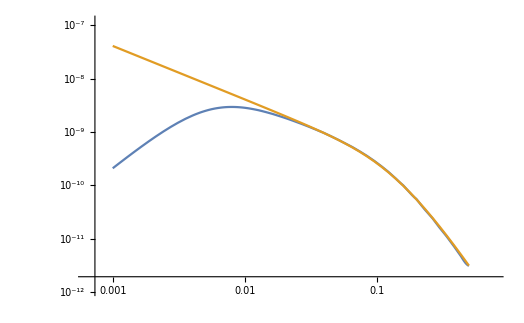

```mathematica
LogLogPlot[{σv[10,3->1,β],σvbsf10[β,3,1,0]},{β,10^-3,0.5}]//Quiet
```

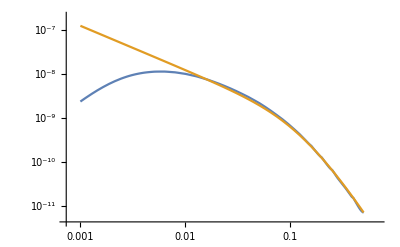

```mathematica
LogLogPlot[{σv[10,1->3,β],σvbsf10[β,1,3,1]},{β,10^-3,0.5}]//Quiet
```

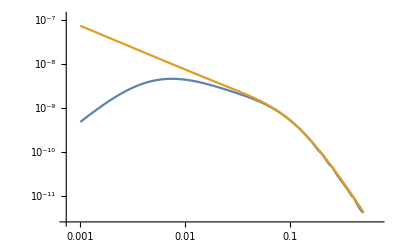

```mathematica
LogLogPlot[{σv[10,5->3,β],σvbsf10[β,5,3,1]},{β,10^-3,0.5}]//Quiet
```

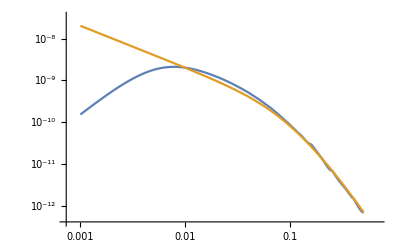

```mathematica
LogLogPlot[{σv[10,3->5,β],σvbsf10[β,3,5,
0]},{β,10^-3,0.5}]//Quiet
```

BS(20)

```mathematica
transitions20={310,131,531,350};WP=6;
```

```mathematica
Do[{i1,i2,S}=IntegerDigits[transition]; Calcolaσv[2,0,λ[i1],λ[i2],10];Clear[β];σv[20,i1->i2,β_]:=Evaluate[(2S+1)/4 σv[β]];Clear[i1,i2,S];,{transition,transitions20}];
```

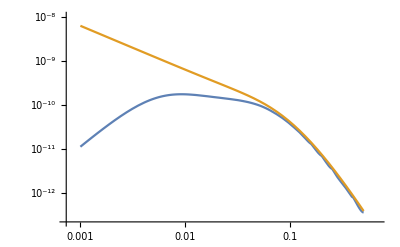

```mathematica
LogLogPlot[{σv[20,3->1,β],σvbsf20[β,3,1,0]},{β,10^-3,0.5}]//Quiet
```

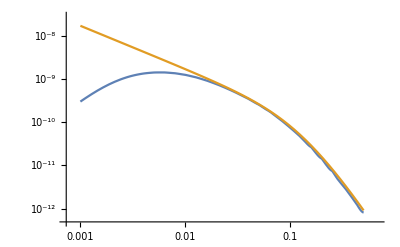

```mathematica
LogLogPlot[{σv[20,1->3,β],σvbsf20[β,1,3,1]},{β,10^-3,0.5}]//Quiet
```

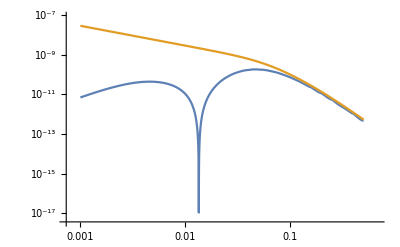

```mathematica
LogLogPlot[{σv[20,5->3,β],σvbsf20[β,5,3,1]},{β,10^-3,0.5}]//Quiet
```

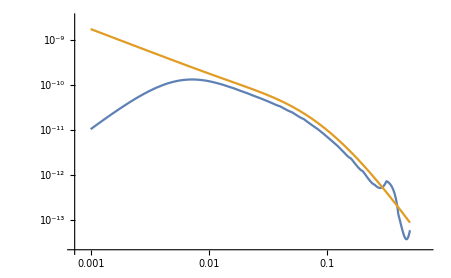

```mathematica
LogLogPlot[{σv[20,3->5,β],σvbsf20[β,3,5,0]},{β,10^-3,0.5}]//Quiet
```

BS(21)

```mathematica
transitions21={311,130,530,351};WP=6;
```

```mathematica
Do[{i1,i2,S}=IntegerDigits[transition]; Calcolaσv[2,1,λ[i1],λ[i2],10];Clear[β];σv[21,i1->i2,β_]:=Evaluate[(2S+1)/4 σv[β]];Clear[i1,i2,S];,{transition,transitions21}];
```

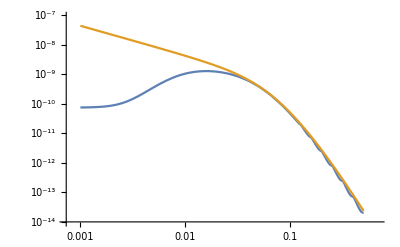

```mathematica
LogLogPlot[{σv[21,3->1,β],σvbsf21[β,3,1,1]},{β,10^-3,0.5}]//Quiet
```

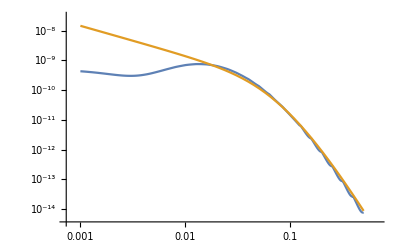

```mathematica
LogLogPlot[{σv[21,1->3,β],σvbsf21[β,1,3,0]},{β,10^-3,0.5}]//Quiet
```

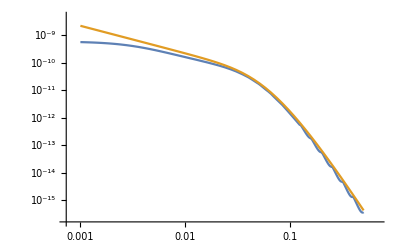

```mathematica
LogLogPlot[{σv[21,5->3,β],σvbsf21[β,5,3,0]},{β,10^-3,0.5}]//Quiet
```

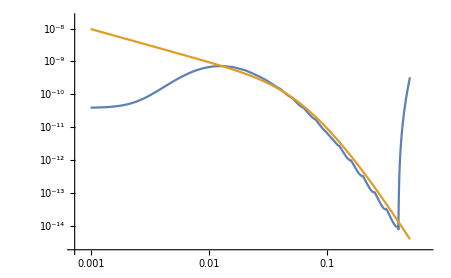

```mathematica
LogLogPlot[{σv[21,3->5,β],σvbsf21[β,3,5,1]},{β,10^-3,0.5}]//Quiet
```

Looking for the fastest integration method

```mathematica
(*WP=5 and no particualr integration method or precision/accuracy goal *)
```

```mathematica
Timing[Calcolaσv[2,1,3,5,10]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{106.443,Null}

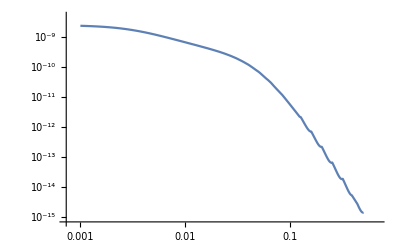

```mathematica
LogLogPlot[σv[β],{β,10^-3,0.5}]
```

```mathematica
(*WP=5 integration method=Trapezoidal no specification for precision and accuracy goal *)
```

```mathematica
WP=5;
```

```mathematica
Timing[Calcolaσv[2,1,3,5,10]]
```

{29.0152,Null}

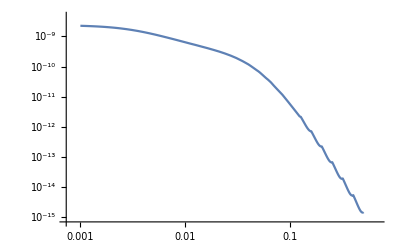

```mathematica
LogLogPlot[σv[β],{β,10^-3,0.5}]
```

```mathematica
Meth="None";WP=4;
```

```mathematica
Timing[Calcolaσv[2,1,3,5,10]]
```

{18.207,Null}

```mathematica
Calcolaσv[2,0,0.0005,3,10]
```

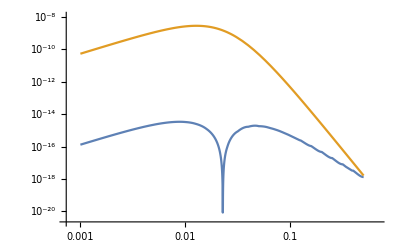

```mathematica
LogLogPlot[{σv[β],σvbsf20[β,7,5,0]},{β,10^-3,0.5}]//Quiet
```

```mathematica
Clear[σv]
```

```mathematica
σv[0.1]
```

5.04974×10^-12 CG1[0.001,3,0.1]

### Checks (Thermal averages)

```mathematica
z=MDM/100;
```

```mathematica
Calcolaσv[1,0,5,6,100]
```

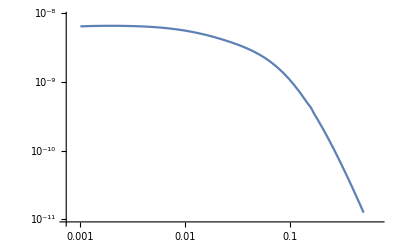

```mathematica
LogLogPlot[σv[β],{β,10^-3,0.5}]
```

```mathematica
(4 z^(3/2))/(√π)σ0 NIntegrate[β^2  Exp[-z β^2] σv[β]/σ0,{β,0,0.99},AccuracyGoal->7,PrecisionGoal->7,WorkingPrecision->7]
```

```mathematica
1.1586551805994196*^-9/σ0
```

31.9719

Computing state (inl)=(110)

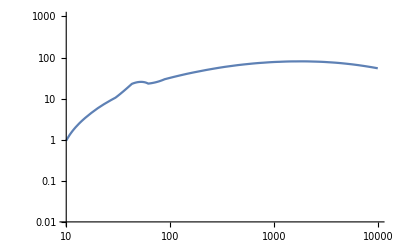

```mathematica
ThermalAverage[110]
```

```mathematica
Calcolaσv[1,0,6,5,100]
```

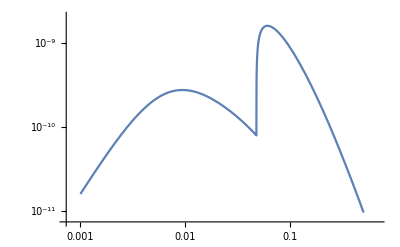

```mathematica
LogLogPlot[σv[β],{β,10^-3,0.5}]
```

```mathematica
(4 z^(3/2))/(√π)σ0 NIntegrate[β^2  Exp[-z β^2] σv[β]/σ0,{β,0,0.99},AccuracyGoal->7,PrecisionGoal->7,WorkingPrecision->7]
```

7.29218×10^-10

Computing state (inl)=(310)

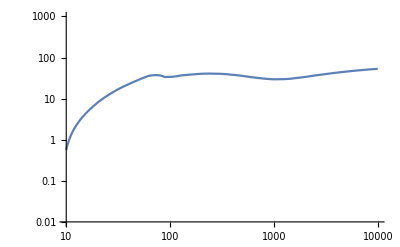

```mathematica
ThermalAverage[310]
```

```mathematica
Calcolaσv[1,0,3,5,100]
```

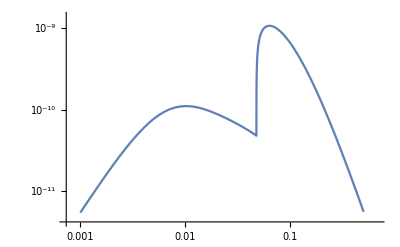

```mathematica
LogLogPlot[σv[β],{β,10^-3,0.5}]
```

```mathematica
(4 z^(3/2))/(√π)σ0 NIntegrate[β^2  Exp[-z β^2] σv[β]/σ0,{β,0,0.99},AccuracyGoal->7,PrecisionGoal->7,WorkingPrecision->7]
```

5.17351×10^-10

```mathematica
(7.29217898878591*^-10+5.173512961901895*^-10)/σ0
```

34.3978

```mathematica
3 1.2465691950687805*^-9
```

3.73971×10^-9

### Cross sections

```mathematica
Wave="Hulten";Kinematics="True";WP=4;
```

```mathematica
States={110,310,510,120,320,520,121,321,521};
```

Computing state (inl)=(110)

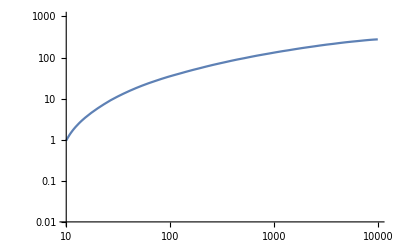

```mathematica
WP=4;zSamplingPoints=15;ThermalAverage[110];
```

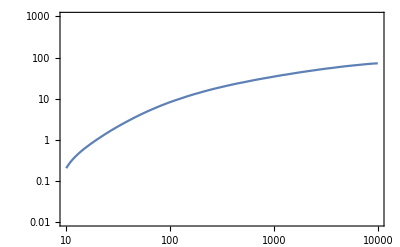

```mathematica
DefineState[110]
```

Computing state (inl)=(310)

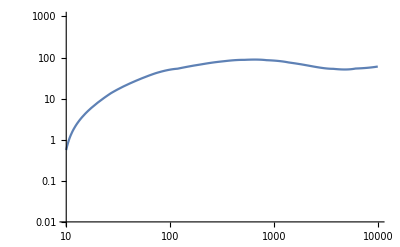

```mathematica
WP=6;zSamplingPoints=20;ThermalAverage[310];
```

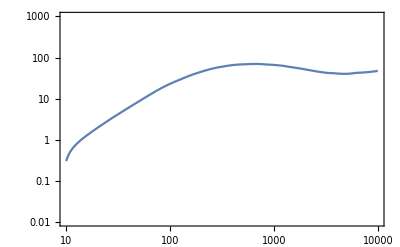

```mathematica
DefineState[310]
```

Computing state (inl)=(510)

InterpolatingFunction::dmval: Input value {10.0014} lies outside the range of data in the interpolating function. Extrapolation will be used.

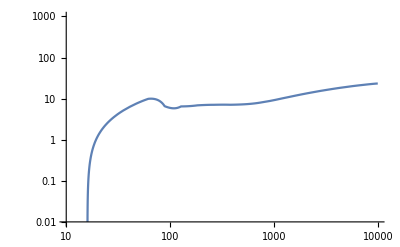

```mathematica
WP=5;zSamplingPoints=20;ThermalAverage[510];
```

InterpolatingFunction::dmval: Input value {10.0014} lies outside the range of data in the interpolating function. Extrapolation will be used.

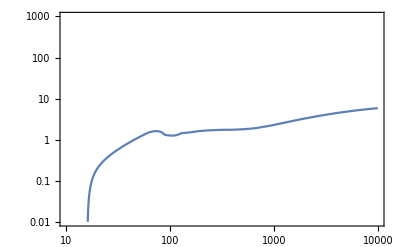

```mathematica
DefineState[510]
```

Computing state (inl)=(120)

InterpolatingFunction::dmval: Input value {10.0014} lies outside the range of data in the interpolating function. Extrapolation will be used.

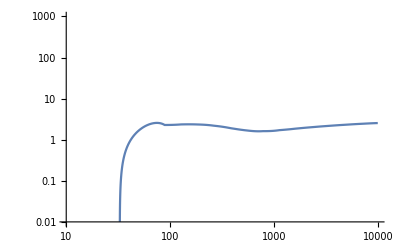

```mathematica
WP=6;zSamplingPoints=20;ThermalAverage[120];
```

InterpolatingFunction::dmval: Input value {10.0014} lies outside the range of data in the interpolating function. Extrapolation will be used.

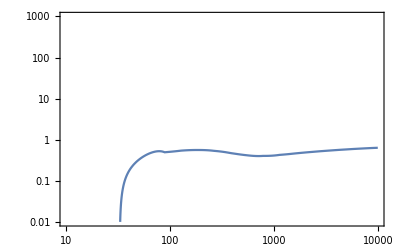

```mathematica
DefineState[120]
```

```mathematica
WP=6;zSamplingPoints=20;ThermalAverage[320];
```

Computing state (inl)=(320)

InterpolatingFunction::dmval: Input value {10.0014} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {10.0014} lies outside the range of data in the interpolating function. Extrapolation will be used.

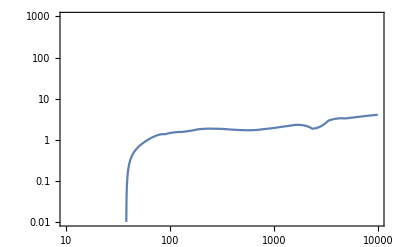

```mathematica
DefineState[320]
```

Computing state (inl)=(520)

InterpolatingFunction::dmval: Input value {10.0014} lies outside the range of data in the interpolating function. Extrapolation will be used.

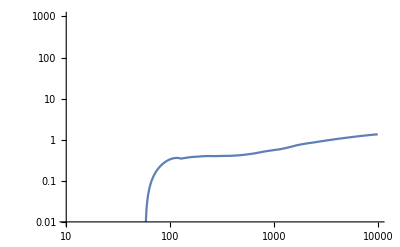

```mathematica
ThermalAverage[520]
```

InterpolatingFunction::dmval: Input value {10.0014} lies outside the range of data in the interpolating function. Extrapolation will be used.

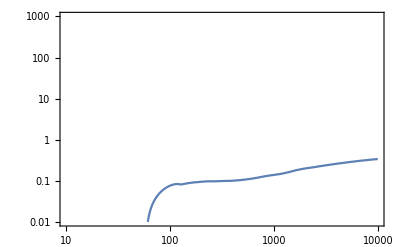

```mathematica
DefineState[520]
```

Computing state (inl)=(121)

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in r in the region {{0,0.04562831}}. NIntegrate obtained 1.044171×10^-6-6.327518×10^-17 ⅈ and 4.237501×10^-9 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in r in the region {{0,0.04562831}}. NIntegrate obtained 8.58567×10^-7+2.392088×10^-17 ⅈ and 2.47637×10^-9 for the integral and error estimates.

InterpolatingFunction::dmval: Input value {10.0014} lies outside the range of data in the interpolating function. Extrapolation will be used.

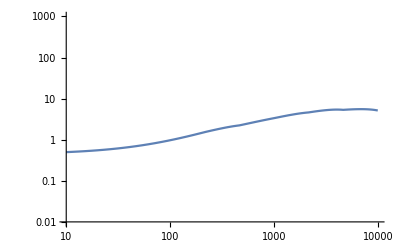

```mathematica
WP=7;zSamplingPoints=10;Met="Trapezoidal";ThermalAverage[121];
```

InterpolatingFunction::dmval: Input value {10.0014} lies outside the range of data in the interpolating function. Extrapolation will be used.

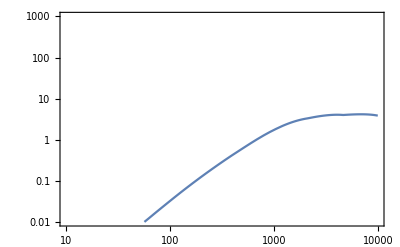

```mathematica
DefineState[121]
```

Computing state (inl)=(321)

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in r in the region {{0,0.04562831}}. NIntegrate obtained -0.0000321518-5.326258×10^-15 ⅈ and 8.188251×10^-8 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in r in the region {{0,0.04562831}}. NIntegrate obtained -0.00006423477+2.561306×10^-14 ⅈ and 1.981872×10^-7 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in r in the region {{0,0.04562831}}. NIntegrate obtained -8.906752×10^-6-1.127462×10^-14 ⅈ and 2.640826×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvi will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {10.0014} lies outside the range of data in the interpolating function. Extrapolation will be used.

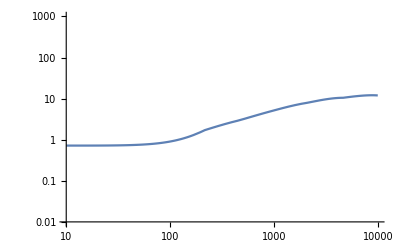

```mathematica
WP=7;zSamplingPoints=10;Met="Trapezoidal";ThermalAverage[321];
```

InterpolatingFunction::dmval: Input value {10.0014} lies outside the range of data in the interpolating function. Extrapolation will be used.

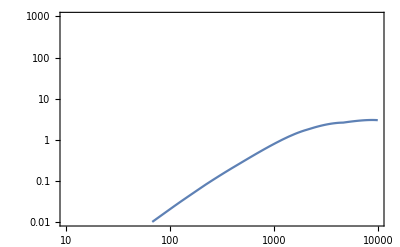

```mathematica
DefineState[321]
```

Computing state (inl)=(521)

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in r in the region {{0,0.0781793487}}. NIntegrate obtained -0.0000388661934-6.3418471×10^-14 ⅈ and 2.35083102×10^-8 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in r in the region {{0,0.0781793487}}. NIntegrate obtained -0.0000315871284-8.37336456×10^-15 ⅈ and 1.67599242×10^-8 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in r in the region {{0,0.0781793487}}. NIntegrate obtained -0.0000521069432+4.58761359×10^-14 ⅈ and 2.70385666×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvi will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {10.0014} lies outside the range of data in the interpolating function. Extrapolation will be used.

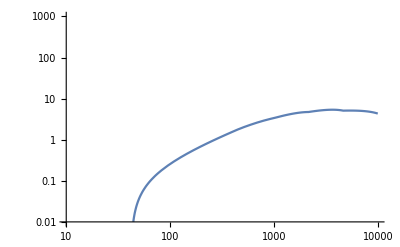

```mathematica
WP=9;zSamplingPoints=10;Met="Trapezoidal";ThermalAverage[521];
```

InterpolatingFunction::dmval: Input value {10.0014} lies outside the range of data in the interpolating function. Extrapolation will be used.

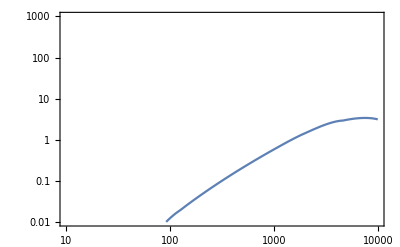

```mathematica
DefineState[521]
```

```mathematica
ztab=Table[10^lz,{lz,1,4,0.1}];zmax=Max[ztab];zmin=Min[ztab];Clear[σvTtab,β,σv];
pert={"ann","Sann"};
Somm[Isospin_]:=Sommerfeld[vrel/2,-λ[Isospin]α2MZ,MWT[MDM/z],MDM];
σv["ann"]=207/20 σ0;σv["Sann"]=σv["ann"](16/69 Somm[1]+25/69 Somm[3]+28/69 Somm[5]);
Do[PrintTemporary[state];σvTtab[state]=ThermalAverage2[state,βcut=1];,{state,pert}];
Do[σvTI[state]=Interpolation[Transpose[{ztab,σvTtab[state]}]],{state,pert}];
states=Join[{"Sann"},States];
σvTtab["tot"]=Sum[σvTI[state],{state,Drop[states,1]}];
RσvTeff["ann",z_]:=σvTI["ann"][z];
RσvTeff["Sann",z_]:=σvTI["Sann"][z];
RσvTeff["Btot",z_]:=Sum[RσvTeff[state,z],{state,States}];
RσvTeff["tot",z_]:=RσvTeff["Sann",z]+RσvTeff["Btot",z];
```

InterpolatingFunction::dmval: Input value {10.0014} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

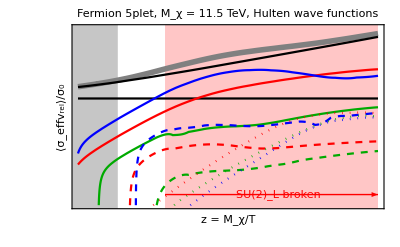

```mathematica
{xmin,xmax,ymin,ymax}={0,4,-2,3};plot5=Plot[Evaluate[Table[Log[10,RσvTeff[state,10^lz]/σ0],{state,Join[{"tot","ann","Sann"},States]}]],{lz,Log[10,zmin],Log[10,zmax]},Frame->True,FrameLabel->{"z = M_χ/T","⟨σ_effv_rel⟩/σ_0"},
FrameTicks->LogLogTicks[normale],
Prolog->{Lighter@Lighter@Pink,Rectangle[{Log[10,MDM/Tc],-4},{xmax,4}],Lighter@Lighter@Gray,Rectangle[{0,-4},{Log[10,25],4}]},
PlotLegends->Map[Style[#,Small,FontFamily->"Times"]&,{"tot","tree","Som","1s_1","1s_3","1s_5","2s_1","2s_3","2s_5","2p_1","2p_3","2p_5"}],PlotStyle->{{Gray,Thickness[0.01]},{Black,Thin},Black,Red,Blue,DGreen,{Red,Dashed},{Blue,Dashed},{DGreen,Dashed},{Red,Dotted},{Blue,Dotted},{DGreen,Dotted},Black},PlotLabel->"Fermion 5plet, M_χ = 11.5 TeV, Hulten wave functions",PlotRange->{ymin,ymax},Axes->False,Epilog->{Red,Arrow[{{Log[10,MDM/Tc],ymin+0.3},{xmax,ymin+0.3}}],Text[" SU(2)_L broken ",{3,ymin+0.29},Background->Lighter@Lighter@Pink]}]
```

## SU(2) broken BS

### Initializations

```mathematica
(* I changed the notation in the sys tab to facilitate the contraction with the group theory factors. Now the (+2,+1,0,-1,-2) component of the triplet are identifyed by the indexes (1,2,3,4,5). The notation for the spin has not been modified. *)
```

```mathematica
defAB:=(A=α2MZ/r ssWT[T] Exp[-MγT[T] r]+ α2MZ/r (1-ssWT[T]) Exp[-MZT[T] r];B= α2MZ Exp[-MWT[T] r]/r);ΔM=0.165;
defV[{{5,1,0},{4,2,0},{3,3,0}}]:=(dim=3;sys={{5,1,0},{4,2,0},{3,3,0}};
defAB;V=({{8ΔMT[T]-4A, -2B, 0}, {-2B, 2ΔMT[T]-A, -3B √2}, {0, -3B √2, 0}}););
defV[{{5,1,1},{4,2,1}}]:=(dim=2;sys={{5,1,1},{4,2,1}};
defAB;V=({{8ΔMT[T]-4 A, -2 B}, {-2 B, 2ΔMT[T]-A}}););
defV[{{4,1,0},{3,2,0}}]:=(dim=2;sys={{4,1,0},{3,2,0}};
defAB;V=({{5 ΔMT[T]-2A, -Sqrt[6] B}, {-Sqrt[6] B, ΔMT[T]-3B}}););
defV[{{4,1,1},{3,2,1}}]:=(dim=2;sys={{4,1,1},{3,2,1}};
defAB;V=({{5 ΔMT[T]-2A, -Sqrt[6] B}, {-Sqrt[6] B, ΔMT[T]-3B}}););
defV[{{3,1,0},{2,2,0}}]:=(dim=2;sys={{3,1,0},{2,2,0}};
defAB;V=({{4 ΔMT[T], -2Sqrt[3] B}, {-2Sqrt[3] B, 2 ΔMT[T]+ A}}););
```

```mathematica
systab={{{5,1,0},{4,2,0},{3,3,0}},{{5,1,1},{4,2,1}},{{4,1,0},{3,2,0}},{{4,1,1},{3,2,1}},{{3,1,0},{2,2,0}}};
```

### Spectrum

```mathematica
l=0;M=MDM=14000;Λ=6;group=SU2;Clear[r];
```

```mathematica
ScanSpectrumT[{{5,1,0},{4,2,0},{3,3,0}},50,15,0.,600.];
```

```mathematica
BS[110]={{0.,129.6104974184211},{12.244897959183673,129.52361774164567},{24.489795918367346,129.26127296451054},{36.73469387755102,128.83284923799656},{48.97959183673469,128.2524917007141},{61.224489795918366,127.53718273537177},{73.46938775510203,126.7049001179164},{85.71428571428571,125.77318757275044},{97.95918367346938,124.7582401644531},{110.20408163265307,123.67444556610121},{122.44897959183673,122.53425517711844},{134.69387755102042,121.34825825180455},{146.93877551020407,120.12536074806557},{159.18367346938777,118.65044119465756},{171.42857142857142,116.75227437318424},{183.67346938775512,114.87491798329762},{195.91836734693877,113.01812337581292},{208.16326530612244,111.18164836245629},{220.40816326530614,109.36525700821517},{232.6530612244898,107.5687194383518},{244.89795918367346,105.79181165864438},{257.1428571428571,104.0343153875929},{269.38775510204084,102.29601789945205},{281.6326530612245,100.57671187711865},{293.87755102040813,98.87619527397061},{306.12244897959187,97.19427118387212},{318.36734693877554,95.53074771863294},{330.61224489795916,93.88543789228261},{342.85714285714283,92.25815951156719},{355.1020408163265,90.64873507215371},{367.34693877551024,89.05699166005107},{379.5918367346939,87.48276085779875},{391.83673469387753,85.92587865502288},{404.0816326530612,84.38618536297422},{416.3265306122449,82.86352553268786},{428.57142857142856,81.35774787644449},{440.8163265306123,79.86870519220658},{453.0612244897959,78.39625429074523},{465.3061224489796,76.94025592516202},{477.55102040816325,75.50057472254812},{489.7959183673469,74.07707911751207},{502.04081632653066,72.66964128733015},{514.2857142857142,71.27813708847272},{526.530612244898,69.90244599427162},{538.7755102040817,68.54245103349622},{551.0204081632653,67.19803872960965},{563.265306122449,65.86909904048471},{575.5102040816327,64.55552529835548},{587.7551020408163,63.25721414979167},{600.,61.974065495475394},{614.2857142857143,60.49609333225272},{628.5714285714286,59.03847873374272},{642.8571428571429,57.6010788649965},{657.1428571428571,56.183756422470765},{671.4285714285714,54.786379493747766},{685.7142857142857,53.40882141342517},{700.,52.050960614623214}};

BS[510]={{0.,24.049286816761825},{12.244897959183673,24.013062406430908},{24.489795918367346,23.899865569170544},{36.73469387755102,23.714100604141468},{48.97959183673469,23.462551178936184},{61.224489795918366,23.153422834461562},{73.46938775510203,22.795423070997437},{85.71428571428571,22.39704627145093},{97.95918367346938,21.96611590376046},{110.20408163265307,21.509555117678463},{122.44897959183673,21.03332277512209},{134.69387755102042,20.54245130064842},{146.93877551020407,20.04113698367165},{159.18367346938777,19.44309626633711},{171.42857142857142,18.68442121332513},{183.67346938775512,17.946277187143608},{195.91836734693877,17.228161544179372},{208.16326530612244,16.52959599882725},{220.40816326530614,15.850124901547924},{232.6530612244898,15.189313698945766},{244.89795918367346,14.546747552360374},{257.1428571428571,13.922030095097607},{269.38775510204084,13.314782311299194},{281.6326530612245,12.72464152175289},{293.87755102040813,12.151260463841057},{306.12244897959187,11.594306454392632},{318.36734693877554,11.053460625526464},{330.61224489795916,10.528417224702737},{342.85714285714283,10.018882971169173},{355.1020408163265,9.524576461837327},{367.34693877551024,9.045227620371891},{379.5918367346939,8.58057718393879},{391.83673469387753,8.130376222663859},{404.0816326530612,7.69438568739579},{416.3265306122449,7.272375981874644},{428.57142857142856,6.864126555876674},{440.8163265306123,6.469425516347618},{453.0612244897959,6.088069253957204},{465.3061224489796,5.719862082906794},{477.55102040816325,5.364615892208254},{489.7959183673469,5.022149807022352},{502.04081632653066,4.692289858999944},{514.2857142857142,4.374868664912198},{526.530612244898,4.0697251131766325},{538.7755102040817,3.7767040581901705},{551.0204081632653,3.4956560226487023},{563.265306122449,3.2264369082742212},{575.5102040816327,2.968907715558691},{587.7551020408163,2.7229342732726973},{600.,2.4883869785558774},{614.2857142857143,2.229022937436562},{628.5714285714286,1.9848488435996903},{642.8571428571429,1.75567983032694},{657.1428571428571,1.5413376684037638},{671.4285714285714,1.3416503511722995},{685.7142857142857,1.1564517118295936},{700.,0.9855810713349267}};

BS[120]={{0.,22.39058334759059},{12.244897959183673,22.32412148837254},{24.489795918367346,22.12276091577729},{36.73469387755102,21.795360926088893},{48.97959183673469,21.355334380906516},{61.224489795918366,20.818777933590063},{73.46938775510203,20.20267741524298},{85.71428571428571,19.523519103195092},{97.95918367346938,18.79640827238177},{110.20408163265307,18.034635990363906},{122.44897959183673,17.24956885630743},{134.69387755102042,16.450735995749607},{146.93877551020407,15.646016248379743},{159.18367346938777,14.701113421216306},{171.42857142857142,13.526870853269447},{183.67346938775512,12.411916901211892},{195.91836734693877,11.354656030175448},{208.16326530612244,10.353578262513398},{220.40816326530614,9.407247125254287},{232.6530612244898,8.514288574682023},{244.89795918367346,7.67338103895602},{257.1428571428571,6.883246724024194},{269.38775510204084,6.14264430380337},{281.6326530612245,5.4503630639135245},{293.87755102040813,4.805218494178655},{306.12244897959187,4.206049237818177},{318.36734693877554,3.6517152174647376},{330.61224489795916,3.1410966844311017},{342.85714285714283,2.6730938918789673},{355.1020408163265,2.2466270847279572},{367.34693877551024,1.8606365324010359},{379.5918367346939,1.5140823988482905},{391.83673469387753,1.2059443323584909},{404.0816326530612,0.9352207436976026},{416.3265306122449,0.7009278042944067},{428.57142857142856,0.502098226385778},{440.8163265306123,0.33777988966728645},{453.0612244897959,0.20703436827491556},{465.3061224489796,0.10893540236172405},{477.55102040816325,0.0425677573392571},{489.7959183673469,0.0070047079167133396}};

BS[520]={{0.,4.676243042685377},{12.244897959183673,4.6369173626629525},{24.489795918367346,4.516476187146422},{36.73469387755102,4.322215235721188},{48.97959183673469,4.065503019984507},{61.224489795918366,3.7600625639589524},{73.46938775510203,3.4203070124936996},{85.71428571428571,3.0600531961596795},{97.95918367346938,2.691713485975361},{110.20408163265307,2.3259101369631248},{122.44897959183673,1.9713921812428172},{134.69387755102042,1.635134848808994},{146.93877551020407,1.3225295021559675},{159.18367346938777,0.9908569650386259},{171.42857142857142,0.6374848666127456},{183.67346938775512,0.36735849932440223},{195.91836734693877,0.17515827892931535},{208.16326530612244,0.060971085650226416},{220.40816326530614,0.014540319609301534}};

BS[130]={{0.,2.472293556181831},{12.244897959183673,2.455305678478507},{24.489795918367346,2.398781486775001},{36.73469387755102,2.305637771876651},{48.97959183673469,2.1809338249732786},{61.224489795918366,2.031032721071801},{73.46938775510203,1.8627615366769512},{85.71428571428571,1.6827491588305512},{97.95918367346938,1.4970019032258237},{110.20408163265307,1.31069353570159},{122.44897959183673,1.1281107902802965},{134.69387755102042,0.9526937382670811},{146.93877551020407,0.787123490791396},{159.18367346938777,0.6080183912606053},{171.42857142857142,0.41264927933845114},{183.67346938775512,0.2578677747784662},{195.91836734693877,0.14137471050238348},{208.16326530612244,0.055607006053877674},{220.40816326530614,0.0032184907014526985}};
```

```mathematica
l=1;group=SU2;ScanSpectrumT[{{5,1,0},{4,2,0},{3,3,0}},50,20,0.,600.];
```

$Aborted

```mathematica
BS[121]={{0.,22.02292669942849},{12.244897959183673,21.952411190260634},{24.489795918367346,21.739020033061063},{36.73469387755102,21.391803127106297},{48.97959183673469,20.924441595755887},{61.224489795918366,20.35336218087404},{73.46938775510203,19.69592864882795},{85.71428571428571,18.969040892082177},{97.95918367346938,18.1882433859946},{110.20408163265307,17.367284149740158},{122.44897959183673,16.517998836295277},{134.69387755102042,15.65039398536931},{146.93877551020407,14.772832023343438},{159.18367346938777,13.73773548409623},{171.42857142857142,12.444102853056581},{183.67346938775512,11.208178297617213},{195.91836734693877,10.029373177236787},{208.16326530612244,8.907223893043662},{220.40816326530614,7.841393013163268},{232.6530612244898,6.831674977876614},{244.89795918367346,5.878008597034902},{257.1428571428571,4.98049971948587},{269.38775510204084,4.139459436867176},{281.6326530612245,3.3554669013475857},{293.87755102040813,2.629473560605543},{306.12244897959187,1.962983552756132},{318.36734693877554,1.3583927874794361},{330.61224489795916,0.8197240846919824},{342.85714285714283,0.35469748608412394}};

BS[521]={{0.,4.406603839895675},{12.244897959183673,4.364825327813265},{24.489795918367346,4.237161014779317},{36.73469387755102,4.031282014439984},{48.97959183673469,3.7591010837224608},{61.224489795918366,3.435026922714577},{73.46938775510203,3.07427688578187},{85.71428571428571,2.6915746818604944},{97.95918367346938,2.3003353763107617},{110.20408163265307,1.9122839452934444},{122.44897959183673,1.5373907767669133},{134.69387755102042,1.1840109917810904},{146.93877551020407,0.8591514668612528},{159.18367346938777,0.5220568068982131},{171.42857142857142,0.18325926155295008}};

BS[131]={{0.,2.7016944717114852},{12.244897959183673,2.679784859796664},{24.489795918367346,2.608880741631027},{36.73469387755102,2.4926038605032286},{48.97959183673469,2.336886754779967},{61.224489795918366,2.149085698249366},{73.46938775510203,1.9371095959277371},{85.71428571428571,1.7087414025951426},{97.95918367346938,1.4712111951951126},{110.20408163265307,1.2309980647301053},{122.44897959183673,0.9938053962981765},{134.69387755102042,0.7646582440597279},{146.93877551020407,0.5480985170154102},{159.18367346938777,0.3157604484534219},{171.42857142857142,0.07319100603239859}};
```

```mathematica
l=0;group=SU2;ScanSpectrumT[{{5,1,1},{4,2,1}},50,20,0.,600.];
```

```mathematica
BS[310]={{0.,85.73239263168144},{12.244897959183673,85.66329338019972},{24.489795918367346,85.45016215684153},{36.73469387755102,85.10066288717047},{48.97959183673469,84.62647767222182},{61.224489795918366,84.041694004384},{73.46938775510203,83.36125697103188},{85.71428571428571,82.59976676098519},{97.95918367346938,81.77070821165944},{110.20408163265307,80.88606325582663},{122.44897959183673,79.95620059609433},{134.69387755102042,78.98993614083105},{146.93877551020407,77.99468165454999},{159.18367346938777,76.79584757869745},{171.42857142857142,75.25570394872645},{183.67346938775512,73.73554426562934},{195.91836734693877,72.23513699888781},{208.16326530612244,70.75426015611056},{220.40816326530614,69.29270071538184},{232.6530612244898,67.85025411048089},{244.89795918367346,66.42672376139947},{257.1428571428571,65.02192064386037},{269.38775510204084,63.63566289252827},{281.6326530612245,62.26777543341478},{293.87755102040813,60.91808964162206},{306.12244897959187,59.58644302112257},{318.36734693877554,58.27267890370189},{330.61224489795916,56.97664616458398},{342.85714285714283,55.69819895257519},{355.1020408163265,54.43719643282654},{367.34693877551024,53.193502540568325},{379.5918367346939,51.96698574436288},{391.83673469387753,50.75751881761202},{404.0816326530612,49.56497861721272},{416.3265306122449,48.38924586840046},{428.57142857142856,47.23020495494969},{440.8163265306123,46.08774371402291},{453.0612244897959,44.9617532350638},{465.3061224489796,43.85212766223701},{477.55102040816325,42.758764000009414},{489.7959183673469,41.68156192155933},{502.04081632653066,40.62042357978159},{514.2857142857142,39.57525342074281},{526.530612244898,38.545957999512275},{538.7755102040817,37.532445798372116},{551.0204081632653,36.53462704748016},{563.265306122449,35.55241354812389},{575.5102040816327,34.585718498774234},{587.7551020408163,33.63445632420087},{600.,32.698542507975546},{614.2857142857143,31.625930157958255},{628.5714285714286,30.573963296587692},{642.8571428571429,29.54251140865301},{657.1428571428571,28.531444687787378},{671.4285714285714,27.54063373080815},{685.7142857142857,26.569949248627648},{700.,25.61926179548202}};

BS[320]={{0.,13.249816069442266},{12.244897959183673,13.201876979809754},{24.489795918367346,13.051810689095028},{36.73469387755102,12.806438834383966},{48.97959183673469,12.476388767249716},{61.224489795918366,12.074555551315228},{73.46938775510203,11.614612778900474},{85.71428571428571,11.109853171136978},{97.95918367346938,10.572448290010675},{110.20408163265307,10.013081019339701},{122.44897959183673,9.440847716927326},{134.69387755102042,8.863325742816249},{146.93877551020407,8.286725534252446},{159.18367346938777,7.61689225619001},{171.42857142857142,6.797305046816843},{183.67346938775512,6.033711332317026},{195.91836734693877,5.32418765549808},{208.16326530612244,4.666889429180365},{220.40816326530614,4.060046933836792},{232.6530612244898,3.501962352140255},{244.89795918367346,2.9910072192047927},{257.1428571428571,2.525619792708314},{269.38775510204084,2.1043020019591725},{281.6326530612245,1.7256158053688166},{293.87755102040813,1.3881789493839696},{306.12244897959187,1.0906602521573234},{318.36734693877554,0.8317746094887348},{330.61224489795916,0.6102779310357673},{342.85714285714283,0.42496217521418067},{355.1020408163265,0.27465059067749237},{367.34693877551024,0.15819321732745037},{379.5918367346939,0.07446266151005533},{391.83673469387753,0.022350107065291197},{404.0816326530612,0.0006820344408789945}};

BS[330]={{0.,1.990285040091878},{12.244897959183673,1.9704557082371357},{24.489795918367346,1.9032046737680135},{36.73469387755102,1.7924333294719315},{48.97959183673469,1.6454369445503798},{61.224489795918366,1.4715733023192927},{73.46938775510203,1.2809182583353342},{85.71428571428571,1.0832020995719183},{97.95918367346938,0.8871272611128836},{110.20408163265307,0.7000297752325014},{122.44897959183673,0.5277878752666094},{134.69387755102042,0.3748779167864908},{146.93877551020407,0.24449917140445054},{159.18367346938777,0.1233151568281283},{171.42857142857142,0.028591915477080152}};
```

```mathematica
l=1;group=SU2;ScanSpectrumT[{{5,1,1},{4,2,1}},50,20,0.,600.];
```

$Aborted

```mathematica
BS[321]={{0.,13.404890199546895},{12.244897959183673,13.352429140190155},{24.489795918367346,13.18895690507087},{36.73469387755102,12.921625804867297},{48.97959183673469,12.561488335330603},{61.224489795918366,12.121933362112136},{73.46938775510203,11.617176155314159},{85.71428571428571,11.061083623276838},{97.95918367346938,10.466423307232564},{110.20408163265307,9.844488872219438},{122.44897959183673,9.20499813818142},{134.69387755102042,8.556158649087124},{146.93877551020407,7.904819426182378},{159.18367346938777,7.143589110960882},{171.42857142857142,6.204878735106843},{183.67346938775512,5.322985003116383},{195.91836734693877,4.497463436506952},{208.16326530612244,3.728083327349217},{220.40816326530614,3.014884625338373},{232.6530612244898,2.3582699454790683},{244.89795918367346,1.7591602822746673},{257.1428571428571,1.2192827612549784},{269.38775510204084,0.741784479626423},{281.6326530612245,0.3329129773145154},{293.87755102040813,0.011042981549235838}};

BS[331]={{0.,1.896502122879035},{12.244897959183673,1.8735711689252996},{24.489795918367346,1.7973609312970464},{36.73469387755102,1.6725466026545432},{48.97959183673469,1.5074250492220658},{61.224489795918366,1.3125354165329777},{73.46938775510203,1.0992881711013036},{85.71428571428571,0.8789016995930183},{97.95918367346938,0.6617567789424224},{110.20408163265307,0.45715728552587026},{122.44897959183673,0.27347936464391276},{134.69387755102042,0.11891870248861311},{146.93877551020407,0.005301256985117662}};
```

```mathematica
Bstates={110,310,510,120,121,320,321,130};
```

```mathematica
θsq[x_]:=If[x<0,Null,x^2]
Eb[αeff_,n_,l_,Mχ_,MV_]:= (αeff^2 Mχ)/(4 n^2)θsq[1-1.91 n^2 MV/(αeff Mχ)-1.75 n^2(MV/(αeff Mχ))^2 l(l+1)];
```

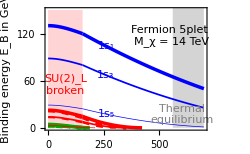

```mathematica
Clear[T]
Mχ=14000.;
ps=Flatten[Outer[List,{Thickness[0.01],Thickness[0.005],Thickness[0.002]},{Blue,Red,{Red,Dashed},Darker@Green,{Darker@Green,Dashed},{Darker@Green,DotDashed}}],1];
{xmax,ymax}={700,150};
EBHulten=Plot[Evaluate[Table[{Eb[λ α2MZ,1,0,Mχ,MWT[T]],Eb[λ α2MZ,2,0,Mχ,MWT[T]],Eb[λ α2MZ,2,1,Mχ,MWT[T]],Eb[λ α2MZ,3,0,Mχ,MWT[T]],Eb[λ α2MZ,3,1,Mχ,MWT[T]],Eb[λ α2MZ,3,2,Mχ,MWT[T]]},{λ,{6,5,3}}]],{T,0,xmax},Frame->True,FrameLabel->{"Temperature in GeV","Binding energy E_B in GeV","z = M_χ/T",""},PlotRange->{0,ymax},
Prolog->{Opacity[0.5],Lighter@Pink,Rectangle[{0,0},{Tc,ymax}],Lighter@Gray,Rectangle[{xmax,0},{Mχ/25,Tc}]},
Epilog->{Gray,Text[Style["Thermal\nequilibrium",Small],{600,17}],Red,
Text[Style["SU(2)_L\nbroken",Small],{Tc/2,55}],Black,
Text["Fermion 5plet \nM_χ = 14 TeV",{0.79 xmax,0.78ymax}],Blue,
Text[" 1s_1",{260,Eb[6 α2MZ,1,0,Mχ,MWT[260]]},Background->White],
Text[" 1s_3",{260,Eb[5 α2MZ,1,0,Mχ,MWT[260]]},Background->White],
Text[" 1s_5",{260,Eb[3 α2MZ,1,0,Mχ,MWT[260]]},Background->White],Red,
(*Text[" 2s_1",{200,Eb[6 α2MZ,2,0,Mχ,MWT[200]]+4}]*)},FrameTicks->{{Automatic,Automatic},{Automatic,Table[{Mχ/z,z},{z,{10,25,50,100}}]}},PlotStyle->ps,ImageSize->250]
```

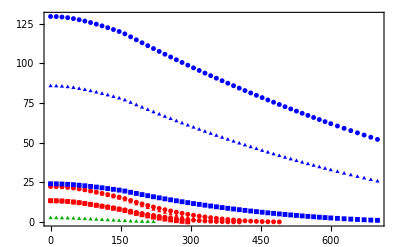

```mathematica
EBNumerics=ListPlot[Table[Sort[BS[state]],{state,Bstates}],Frame->True,PlotMarkers->{{●,5},{▲,5},{■,5},{●,5},{▲,5},{●,5},{■,5},{▲,5}},PlotStyle->{Blue,Blue,Blue,Red,Red,Red,Red,Darker@Green}]
```

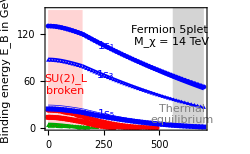

```mathematica
EBplot5=Show[EBHulten,EBNumerics]
```

```mathematica
Export["/Users/Andrea/Dropbox/Finished Works/DM bound state/figs/EB5.pdf",EBplot5]
```

/Users/Andrea/Dropbox/Finished Works/DM bound state/figs/EB5.pdf

#### 11.0 TeV results

```mathematica
BS[110]={{0.,98.63851663736673},{12.244897959183673,98.55364815432611},{24.489795918367346,98.29732501561908},{36.73469387755102,97.87890330451681},{48.97959183673469,97.3124847236487},{61.224489795918366,96.61499766039087},{73.46938775510203,95.80435799523374},{85.71428571428571,94.89804200227765},{97.95918367346938,93.91217369319328},{110.20408163265307,92.8610676372721},{122.44897959183673,91.75710126884458},{134.69387755102042,90.61078990231411},{146.93877551020407,89.43096622665666},{159.18367346938777,88.01092613052629},{171.42857142857142,86.18816375530332},{183.67346938775512,84.39072285251297},{195.91836734693877,82.61824014048675},{208.16326530612244,80.87036408692207},{220.40816326530614,79.1467545027934},{232.6530612244898,77.44708216808382},{244.89795918367346,75.77102848575142},{257.1428571428571,74.1182851608313},{269.38775510204084,72.48855390194554},{281.6326530612245,70.88154614282544},{293.87755102040813,69.29698278169924},{306.12244897959187,67.73459393663785},{318.36734693877554,66.19411871512723},{330.61224489795916,64.6753049962946},{342.85714285714283,63.17790922434436},{355.1020408163265,61.70169621186286},{367.34693877551024,60.24643895174996},{379.5918367346939,58.81191843659593},{391.83673469387753,57.39792348439342},{404.0816326530612,56.00425056951437},{416.3265306122449,54.63070365792901},{428.57142857142856,53.277094045669735},{440.8163265306123,51.94324019957292},{453.0612244897959,50.62896759934842},{465.3061224489796,49.33410858004875},{477.55102040816325,48.05850217402022},{489.7959183673469,46.801993951435755},{502.04081632653066,45.56443585851984},{514.2857142857142,44.345686042799585},{526.530612244898,43.14560873308908},{538.7755102040817,41.964073967690986},{551.0204081632653,40.800957512812026},{563.265306122449,39.65614062762002},{575.5102040816327,38.52950988089247},{587.7551020408163,37.4209569500146},{600.,36.330378411506125}};

BS[510]={{0.,17.499459093487648},{12.244897959183673,17.465485975504503},{24.489795918367346,17.358977238094095},{36.73469387755102,17.18422309191385},{48.97959183673469,16.94786830736915},{61.224489795918366,16.65796325026464},{73.46938775510203,16.323051206236705},{85.71428571428571,15.95145892142423},{97.95918367346938,15.550842953668589},{110.20408163265307,15.127963143289234},{122.44897959183673,14.688620496819274},{134.69387755102042,14.237696134320242},{146.93877551020407,13.779242158328646},{159.18367346938777,13.235146439091732},{171.42857142857142,12.549636559614326},{183.67346938775512,11.887975590577922},{195.91836734693877,11.249489999037221},{208.16326530612244,10.633544139577733},{220.40816326530614,10.039537374767308},{232.6530612244898,9.466901537431323},{244.89795918367346,8.915098683599858},{257.1428571428571,8.383619092643558},{269.38775510204084,7.871979477347161},{281.6326530612245,7.379721371823744},{293.87755102040813,6.906409669522363},{306.12244897959187,6.451631287310799},{318.36734693877554,6.014993934880708},{330.61224489795916,5.596124971622655},{342.85714285714283,5.194670335751198},{355.1020408163265,4.810293532882584},{367.34693877551024,4.442674673529859},{379.5918367346939,4.091509551118891},{391.83673469387753,3.756508754160182},{404.0816326530612,3.437396808145262},{416.3265306122449,3.1339113445590856},{428.57142857142856,2.845802296094255},{440.8163265306123,2.572831118662383},{453.0612244897959,2.314770042070849},{465.3061224489796,2.0714013521833468},{477.55102040816325,1.8425167079216243},{489.7959183673469,1.6279164965244153},{502.04081632653066,1.427409230011023},{514.2857142857142,1.2408109838905454},{526.530612244898,1.0679448854232658},{538.7755102040817,0.9086406307232301},{551.0204081632653,0.7627340617884161},{563.265306122449,0.6300667672221723},{575.5102040816327,0.5104857230963084},{587.7551020408163,0.40384296385119023},{600.,0.3099952809662953}};

BS[120]={{0.,15.186951864358129},{12.244897959183673,15.126973608585844},{24.489795918367346,14.9449431882414},{36.73469387755102,14.649432760926311},{48.97959183673469,14.253469152792471},{61.224489795918366,13.772694822829004},{73.46938775510203,13.223600510435649},{85.71428571428571,12.62215874812891},{97.95918367346938,11.982959273234155},{110.20408163265307,11.318787673829865},{122.44897959183673,10.640522690937532},{134.69387755102042,9.957227317575077},{146.93877551020407,9.276337433714106},{159.18367346938777,8.487083055459253},{171.42857142857142,7.5234483990516585},{183.67346938775512,6.628058687767811},{195.91836734693877,5.798768552266507},{208.16326530612244,5.033521682159954},{220.40816326530614,4.33033252169721},{232.6530612244898,3.687272803833363},{244.89795918367346,3.1024627151920443},{257.1428571428571,2.5740660175062566},{269.38775510204084,2.1002880579048964},{281.6326530612245,1.679375397046711},{293.87755102040813,1.3096158425723912},{306.12244897959187,0.9893379850510634},{318.36734693877554,0.7169097856509783},{330.61224489795916,0.49073618501746097},{342.85714285714283,0.30925594688480085},{355.1020408163265,0.170938001234443}};

BS[520]={{0.,2.2548525440005336},{12.244897959183673,2.2265542489346926},{24.489795918367346,2.139107666509751},{36.73469387755102,1.9988400587401476},{48.97959183673469,1.8159039068206777},{61.224489795918366,1.602633298763214},{73.46938775510203,1.3719439872864643},{85.71428571428571,1.1360967449668575},{97.95918367346938,0.9059239235914919},{110.20408163265307,0.6904647614214161},{122.44897959183673,0.49689053829493135},{134.69387755102042,0.3305985462202554},{146.93877551020407,0.1953766904143199}};

BS[130]={{0.,1.1755485478262626},{12.244897959183673,1.1650219641549806},{24.489795918367346,1.1268799104917562},{36.73469387755102,1.0630440571842388},{48.97959183673469,0.977569939001208},{61.224489795918366,0.8758427576843242},{73.46938775510203,0.7637536732298468},{85.71428571428571,0.6470432876970365},{97.95918367346938,0.5308766979540375},{110.20408163265307,0.41962884865678474},{122.44897959183673,0.31682267727522606},{134.69387755102042,0.22516120990853905}};

BS[121]={{0.,14.747156994977805},{12.244897959183673,14.682458181599646},{24.489795918367346,14.48643735727779},{36.73469387755102,14.167961005460407},{48.97959183673469,13.740471882009908},{61.224489795918366,13.220125074141377},{73.46938775510203,12.62399885653231},{85.71428571428571,11.968710120600786},{97.95918367346938,11.269535707277887},{110.20408163265307,10.539980959352771},{122.44897959183673,9.791670602821153},{134.69387755102042,9.034436620963774},{146.93877551020407,8.276506374591703},{159.18367346938777,7.39380150022204},{171.42857142857142,6.310073445925995},{183.67346938775512,5.297805499795032},{195.91836734693877,4.356890000656462},{208.16326530612244,3.4875726832274103},{220.40816326530614,2.6905684571356034},{232.6530612244898,1.9672809233036013},{244.89795918367346,1.3202396746691734},{257.1428571428571,0.7540979192545395},{269.38775510204084,0.2786908819232686}};

BS[521]={{0.,1.9667603179808004},{12.244897959183673,1.9362778276073935},{24.489795918367346,1.8425308088624344},{36.73469387755102,1.6924550562069909},{48.97959183673469,1.4971097121406243},{61.224489795918366,1.2700107330888835},{73.46938775510203,1.0255279737991527},{85.71428571428571,0.7776831170525237},{97.95918367346938,0.5394840572277269},{110.20408163265307,0.32283891155224437},{122.44897959183673,0.13930227905706738}};

BS[131]={{0.,1.213869438818708},{12.244897959183673,1.1980332431492473},{24.489795918367346,1.144566844479055},{36.73469387755102,1.056543149785262},{48.97959183673469,0.9394502004209},{61.224489795918366,0.8003410813092061},{73.46938775510203,0.6470092327409886},{85.71428571428571,0.48738903670234707},{97.95918367346938,0.3292899138252568},{110.20408163265307,0.18059185158504792}};

BS[310]={{0.,64.73576627645637},{12.244897959183673,64.668628824716},{24.489795918367346,64.46136124747053},{36.73469387755102,64.12158340023517},{48.97959183673469,63.66092096654872},{61.224489795918366,63.09339645246296},{73.46938775510203,62.433884599926635},{85.71428571428571,61.69691240421972},{97.95918367346938,60.895890541303615},{110.20408163265307,60.04272717029857},{122.44897959183673,59.14771854985766},{134.69387755102042,58.21961010215979},{146.93877551020407,57.26574546059933},{159.18367346938777,56.11962610001601},{171.42857142857142,54.65193744572268},{183.67346938775512,53.2086213138752},{195.91836734693877,51.789358650718796},{208.16326530612244,50.39384590943966},{220.40816326530614,49.02179402595532},{232.6530612244898,47.67292748760036},{244.89795918367346,46.346983479462615},{257.1428571428571,45.04371109574335},{269.38775510204084,43.762870605594706},{281.6326530612245,42.50423276458566},{293.87755102040813,41.26757816434244},{306.12244897959187,40.05269661407557},{318.36734693877554,38.85938654869306},{330.61224489795916,37.687454459050294},{342.85714285714283,36.53671434062672},{355.1020408163265,35.40698715758158},{367.34693877551024,34.29810031972424},{379.5918367346939,33.20988717048102},{391.83673469387753,32.14218648443001},{404.0816326530612,31.094841973440676},{416.3265306122449,30.06770180088956},{428.57142857142856,29.060618103831917},{440.8163265306123,28.073446523397735},{453.0612244897959,27.10604574404154},{465.3061224489796,26.158277042628843},{477.55102040816325,25.230003848648494},{489.7959183673469,24.321091317143807},{502.04081632653066,23.431405916209183},{514.2857142857142,22.56081502671362},{526.530612244898,21.709186587456983},{538.7755102040817,20.876388695350197},{551.0204081632653,20.062289317835297},{563.265306122449,19.266755965394548},{575.5102040816327,18.489655419516318},{587.7551020408163,17.730853487645295},{600.,16.990214791875914}};

BS[320]={{0.,8.56946043611758},{12.244897959183673,8.528175906854978},{24.489795918367346,8.397818649246462},{36.73469387755102,8.184726228755002},{48.97959183673469,7.89895487083574},{61.224489795918366,7.552779270982938},{73.46938775510203,7.1592304371704945},{85.71428571428571,6.73095429062362},{97.95918367346938,6.279482716005973},{110.20408163265307,5.8148727494386145},{122.44897959183673,5.34561242072948},{134.69387755102042,4.878690157585384},{146.93877551020407,4.419747752755996},{159.18367346938777,3.896594301605341},{171.42857142857142,3.273840822444677},{183.67346938775512,2.713533683901585},{195.91836734693877,2.21302969908279},{208.16326530612244,1.769822612286262},{220.40816326530614,1.3815347195868015},{232.6530612244898,1.0459065264687313},{244.89795918367346,0.7607846790607846},{257.1428571428571,0.5241089115147061},{269.38775510204084,0.33389885195346747},{281.6326530612245,0.18824131565736113},{293.87755102040813,0.08527840960278282},{306.12244897959187,0.02319653510757038},{318.36734693877554,0.00007556874448519947}};

BS[330]={{0.,0.5980063643482175},{12.244897959183673,0.5896539541768444},{24.489795918367346,0.555930185175261},{36.73469387755102,0.49875670454838994},{48.97959183673469,0.42339271795643363},{61.224489795918366,0.3371601535984995},{73.46938775510203,0.24813649426206186},{85.71428571428571,0.16410659055126656},{97.95918367346938,0.09187709665360573},{110.20408163265307,0.036925271853822106},{122.44897959183673,0.00336597602769836}};

BS[321]={{0.,8.53491727903212},{12.244897959183673,8.48839345991825},{24.489795918367346,8.34256860685525},{36.73469387755102,8.104295532190399},{48.97959183673469,7.784289355264112},{61.224489795918366,7.395589698312204},{73.46938775510203,6.952069432420738},{85.71428571428571,6.4672729028321205},{97.95918367346938,5.953674017972774},{110.20408163265307,5.422308592189997},{122.44897959183673,4.8826784849575295},{134.69387755102042,4.342823943463316},{146.93877551020407,3.8094842256104338},{159.18367346938777,3.198522233552602},{171.42857142857142,2.4674303854236728},{183.67346938775512,1.8082508634695278},{195.91836734693877,1.222463273847592},{208.16326530612244,0.713357668423452},{220.40816326530614,0.28832350774400656}};

BS[331]={{0.,0.446645936021176},{12.244897959183673,0.43581133653455434},{24.489795918367346,0.39507143326138716},{36.73469387755102,0.3275833111048006},{48.97959183673469,0.24033764956098347},{61.224489795918366,0.14292021806949304},{73.46938775510203,0.04647602678343365}};
```

#### 11.5 TeV results

```mathematica
BS[110]={{0.,103.79448334989105},{12.244897959183673,103.70921080278829},{24.489795918367346,103.45167809152856},{36.73469387755102,103.03124786911337},{48.97959183673469,102.46203130478027},{61.224489795918366,101.7609685292864},{73.46938775510203,100.94598885720721},{85.71428571428571,100.03458317142918},{97.95918367346938,99.04289083842599},{110.20408163265307,97.98524218836621},{122.44897959183673,96.87403056269771},{134.69387755102042,95.7197871362545},{146.93877551020407,94.53136027188212},{159.18367346938777,93.10036749522153},{171.42857142857142,91.26256980289081},{183.67346938775512,89.44920975938368},{195.91836734693877,87.65994800785182},{208.16326530612244,85.89445572193772},{220.40816326530614,84.15241424604432},{232.6530612244898,82.43351476331493},{244.89795918367346,80.73745798828914},{257.1428571428571,79.06395388158981},{269.38775510204084,77.41272138433395},{281.6326530612245,75.78348817021595},{293.87755102040813,74.17599041344855},{306.12244897959187,72.58997257094084},{318.36734693877554,71.02518717724756},{330.61224489795916,69.48139465096615},{342.85714285714283,67.95836311136696},{355.1020408163265,66.45586820414339},{367.34693877551024,64.97369293524723},{379.5918367346939,63.51162751183498},{391.83673469387753,62.06946918942141},{404.0816326530612,60.64702212436818},{416.3265306122449,59.24409723088242},{428.57142857142856,57.86051204172922},{440.8163265306123,56.49609057188431},{453.0612244897959,55.15066318437957},{465.3061224489796,53.82406645760662},{477.55102040816325,52.516143053358256},{489.7959183673469,51.226741584899976},{502.04081632653066,49.95571648437573},{514.2857142857142,48.70292786885948},{526.530612244898,47.46824140437421},{538.7755102040817,46.25152816721651},{551.0204081632653,45.05266450193318},{563.265306122449,43.87153187515065},{575.5102040816327,42.70801672578599},{587.7551020408163,41.56201030762756},{600.,40.43340852942712}};

BS[510]={{0.,18.584847361606748},{12.244897959183673,18.550426515807892},{24.489795918367346,18.44258759290039},{36.73469387755102,18.265645228331152},{48.97959183673469,18.02627392111195},{61.224489795918366,17.73255716279647},{73.46938775510203,17.393073144453382},{85.71428571428571,17.016184071190764},{97.95918367346938,16.609581633924016},{110.20408163265307,16.180059886634083},{122.44897959183673,15.733452757250731},{134.69387755102042,15.274672782394079},{146.93877551020407,14.807801874615032},{159.18367346938777,14.253127700136995},{171.42857142857142,13.55329209661521},{183.67346938775512,12.876679413899302},{195.91836734693877,12.222650077433476},{208.16326530612244,11.590599494141518},{220.40816326530614,10.979955422002963},{232.6530612244898,10.39017564606444},{244.89795918367346,9.82074591664313},{257.1428571428571,9.271178112104566},{269.38775510204084,8.741008593945004},{281.6326530612245,8.229796726317499},{293.87755102040813,7.737123535821438},{306.12244897959187,7.262590490514949},{318.36734693877554,6.805818379821432},{330.61224489795916,6.366446279391162},{342.85714285714283,5.944130587112818},{355.1020408163265,5.538544118410645},{367.34693877551024,5.149375250755833},{379.5918367346939,4.776327108994779},{391.83673469387753,4.419116784681467},{404.0816326530612,4.077474584108685},{416.3265306122449,3.7511433011722564},{428.57142857142856,3.4398775125665497},{440.8163265306123,3.143442894093039},{453.0612244897959,2.861615558033136},{465.3061224489796,2.594181412561268},{477.55102040816325,2.3409355450024782},{489.7959183673469,2.101681631313335},{502.04081632653066,1.876231374430429},{514.2857142857142,1.6644039740394443},{526.530612244898,1.4660256298591516},{538.7755102040817,1.280929079748706},{551.0204081632653,1.1089531729337985},{563.265306122449,0.9499424776782377},{575.5102040816327,0.8037469209552179},{587.7551020408163,0.6702214599294719},{600.,0.5492257789454407}};

BS[120]={{0.,16.36893012478653},{12.244897959183673,16.30766724843151},{24.489795918367346,16.121810315248418},{36.73469387755102,15.819993072232997},{48.97959183673469,15.415324109657961},{61.224489795918366,14.923541316726116},{73.46938775510203,14.361238832059563},{85.71428571428571,13.74449594610525},{97.95918367346938,13.088009065479183},{110.20408163265307,12.404668002696543},{122.44897959183673,11.705451859367294},{134.69387755102042,10.99951945932923},{146.93877551020407,10.294397888458562},{159.18367346938777,9.47472696075316},{171.42857142857142,8.470000679752642},{183.67346938775512,7.531851280719047},{195.91836734693877,6.658254241754307},{208.16326530612244,5.847275578709657},{220.40816326530614,5.097053870035825},{232.6530612244898,4.405786072559767},{244.89795918367346,3.7717172113501354},{257.1428571428571,3.193133699591309},{269.38775510204084,2.668359703686846},{281.6326530612245,2.19575569690056},{293.87755102040813,1.7737182175313144},{306.12244897959187,1.400679908150095},{318.36734693877554,1.0751091484281736},{330.61224489795916,0.7955089291156615},{342.85714285714283,0.5604149296655213},{355.1020408163265,0.36839295468814126},{367.34693877551024,0.2180359353802943},{379.5918367346939,0.1079606716901146},{391.83673469387753,0.03680473693409567},{404.0816326530612,0.003150928991679577}};

BS[520]={{0.,2.6280262444382476},{12.244897959183673,2.597607603746651},{24.489795918367346,2.503783676441659},{36.73469387755102,2.353082677200471},{48.97959183673469,2.155910776496102},{61.224489795918366,1.9248933695904284},{73.46938775510203,1.6732616008626318},{85.71428571428571,1.4136050828501514},{97.95918367346938,1.1570910035150368},{110.20408163265307,0.9130950742832751},{122.44897959183673,0.6891253845191263},{134.69387755102042,0.4909186452976065},{146.93877551020407,0.3226138286303017},{159.18367346938777,0.16692856703982079},{171.42857142857142,0.04785721272911588},{183.67346938775512,0.006358663741947225}};

BS[130]={{0.,1.3793346595874978},{12.244897959183673,1.3674957475785947},{24.489795918367346,1.3256764019650844},{36.73469387755102,1.2560261061101037},{48.97959183673469,1.1628206022537055},{61.224489795918366,1.0516536421995715},{73.46938775510203,0.9286124668671485},{85.71428571428571,0.7996220299522901},{97.95918367346938,0.6700216697178685},{110.20408163265307,0.5443527912119825},{122.44897959183673,0.42630007298096184},{134.69387755102042,0.318727187528084},{146.93877551020407,0.2237622803670356},{159.18367346938777,0.130591746499835},{171.42857142857142,0.04269394826979644}};

BS[121]={{0.,15.94289982451148},{12.244897959183673,15.877038997742046},{24.489795918367346,15.67754911635386},{36.73469387755102,15.35333524623323},{48.97959183673469,14.917889372828188},{61.224489795918366,14.387421817893069},{73.46938775510203,13.779067948633944},{85.71428571428571,13.109500141149354},{97.95918367346938,12.394046392495842},{110.20408163265307,11.64625685399708},{122.44897959183673,10.877793279522384},{134.69387755102042,10.098515897998608},{146.93877551020407,9.316670788727103},{159.18367346938777,8.403461978912947},{171.42857142857142,7.277622463629163},{183.67346938775512,6.22033662930704},{195.91836734693877,5.231332095419134},{208.16326530612244,4.310607166836564},{220.40816326530614,3.458492942362073},{232.6530612244898,2.6757685166591303},{244.89795918367346,1.9638742119728718},{257.1428571428571,1.3253304214232218},{269.38775510204084,0.7646832479221881},{281.6326530612245,0.29135864928342214}};

BS[521]={{0.,2.3418346825608767},{12.244897959183673,2.3091440457402026},{24.489795918367346,2.2087207767469548},{36.73469387755102,2.047646803813861},{48.97959183673469,1.8371474841693054},{61.224489795918366,1.590905924522858},{73.46938775510203,1.3234364707197799},{85.71428571428571,1.0488489246231674},{97.95918367346938,0.7801215980288194},{110.20408163265307,0.5288692190768579},{122.44897959183673,0.30560568089824314},{134.69387755102042,0.12086895178566898}};

BS[131]={{0.,1.4493367889025808},{12.244897959183673,1.4322307966296262},{24.489795918367346,1.375172976014089},{36.73469387755102,1.281360337729512},{48.97959183673469,1.156367055782232},{61.224489795918366,1.0072860975099165},{73.46938775510203,0.8418892606822765},{85.71428571428571,0.6679954564060857},{97.95918367346938,0.4931293744995411},{110.20408163265307,0.324505171528308},{122.44897959183673,0.1694738806390423},{134.69387755102042,0.03747131060880926}};

BS[310]={{0.,68.22945739559503},{12.244897959183673,68.16192562976656},{24.489795918367346,67.95347986182661},{36.73469387755102,67.61174951045047},{48.97959183673469,67.14837243426358},{61.224489795918366,66.57738510273491},{73.46938775510203,65.91367731390565},{85.71428571428571,65.17179167070886},{97.95918367346938,64.36515460579115},{110.20408163265307,63.50568989608259},{122.44897959183673,62.60370908125534},{134.69387755102042,61.66797239771527},{146.93877551020407,60.70583774597018},{159.18367346938777,59.549191842238336},{171.42857142857142,58.067043574783526},{183.67346938775512,56.60840151945086},{195.91836734693877,55.17296430374131},{208.16326530612244,53.76044476052698},{220.40816326530614,52.37056901002745},{232.6530612244898,51.00307562611732},{244.89795918367346,49.657714873546446},{257.1428571428571,48.334248004938665},{269.38775510204084,47.032446608238565},{281.6326530612245,45.752091996757876},{293.87755102040813,44.49297463517291},{306.12244897959187,43.25489359583149},{318.36734693877554,42.03765604057524},{330.61224489795916,40.841076724004694},{342.85714285714283,39.66497751474166},{355.1020408163265,38.50918693179196},{367.34693877551024,37.37353969359942},{379.5918367346939,36.257876277824494},{391.83673469387753,35.16204249027889},{404.0816326530612,34.08588904182116},{416.3265306122449,33.02927113236336},{428.57142857142856,31.99204804146258},{440.8163265306123,30.974082725199402},{453.0612244897959,29.975241419965407},{465.3061224489796,28.995393251861717},{477.55102040816325,28.034409855055717},{489.7959183673469,27.0921649972088},{502.04081632653066,26.168534214696756},{514.2857142857142,25.263394458360086},{526.530612244898,24.376623751331678},{538.7755102040817,23.508100860573457},{551.0204081632653,22.65770498388235},{563.265306122449,21.825315454076666},{575.5102040816327,21.010811463361573},{587.7551020408163,20.21407180662539},{600.,19.434974650958825}};

BS[320]={{0.,9.332028714178964},{12.244897959183673,9.289423048479227},{24.489795918367346,9.155158417665872},{36.73469387755102,8.9356777739968},{48.97959183673469,8.641160197891033},{61.224489795918366,8.284012858282283},{73.46938775510203,7.8774033586754575},{85.71428571428571,7.434114738355438},{97.95918367346938,6.965814276206524},{110.20408163265307,6.482691339416309},{122.44897959183673,5.99336245351606},{134.69387755102042,5.504940260787197},{146.93877551020407,5.023186214466574},{159.18367346938777,4.471676973391549},{171.42857142857142,3.8109918418422137},{183.67346938775512,3.211642924991802},{195.91836734693877,2.6711296441255006},{208.16326530612244,2.1870753259213647},{220.40816326530614,1.757221090326246},{232.6530612244898,1.3794183923802867},{244.89795918367346,1.0516199733813678},{257.1428571428571,0.771869528070834},{269.38775510204084,0.5382907042454609},{281.6326530612245,0.3490760724963725},{293.87755102040813,0.20247652351361134},{306.12244897959187,0.0967913253660406},{318.36734693877554,0.030358905065402373},{330.61224489795916,0.0015297384725504546}};

BS[330]={{0.,0.8055548773623049},{12.244897959183673,0.7949868661409124},{24.489795918367346,0.754770950867383},{36.73469387755102,0.6872508213347596},{48.97959183673469,0.5981125118408129},{61.224489795918366,0.49510238320121414},{73.46938775510203,0.3867146648893671},{85.71428571428571,0.28114169643639914},{97.95918367346938,0.18558924013789674},{110.20408163265307,0.10592099102545947},{122.44897959183673,0.046535600080415435},{134.69387755102042,0.010373344862778364}};

BS[321]={{0.,9.330526986220532},{12.244897959183673,9.28281149321467},{24.489795918367346,9.133447782425801},{36.73469387755102,8.889353238632445},{48.97959183673469,8.56131407572075},{61.224489795918366,8.162442112034054},{73.46938775510203,7.70667964444603},{85.71428571428571,7.20763493786093},{97.95918367346938,6.6778382666621585},{110.20408163265307,6.128372487649875},{122.44897959183673,5.568775297184751},{134.69387755102042,5.007109179425832},{146.93877551020407,4.450118663172071},{159.18367346938777,3.8089611304464244},{171.42857142857142,3.0359219585605546},{183.67346938775512,2.3313063845970583},{195.91836734693877,1.695824595538845},{208.16326530612244,1.1312489954716292},{220.40816326530614,0.641294223018978},{232.6530612244898,0.23432108367052568}};

BS[331]={{0.,0.6621778278953181},{12.244897959183673,0.6489279742158283},{24.489795918367346,0.6010938486435076},{36.73469387755102,0.5221448794355256},{48.97959183673469,0.4193009613255127},{61.224489795918366,0.30223893977042005},{73.46938775510203,0.1818759526187927},{85.71428571428571,0.06968355962505152}};
```

#### 12.2 TeV results

```mathematica
BS[110]={{0.,111.01746345728162},{12.244897959183673,110.93167798275391},{24.489795918367346,110.67260965506225},{36.73469387755102,110.24962908476918},{48.97959183673469,109.67685892494046},{61.224489795918366,108.9712535698606},{73.46938775510203,108.15075867101575},{85.71428571428571,107.23288289908854},{97.95918367346938,106.2337843414621},{110.20408163265307,105.16781257117529},{122.44897959183673,104.04738037968524},{134.69387755102042,102.88303836471565},{146.93877551020407,101.68365411456556},{159.18367346938777,100.23870549627286},{171.42857142857142,98.3817401448897},{183.67346938775512,96.54807457844774},{195.91836734693877,94.73739922274946},{208.16326530612244,92.94941360305427},{220.40816326530614,91.1838260383841},{232.6530612244898,89.44035335881243},{244.89795918367346,87.71872064330351},{257.1428571428571,86.01866097597865},{269.38775510204084,84.33991521893864},{281.6326530612245,82.68223179999674},{293.87755102040813,81.04536651386017},{306.12244897959187,79.42908233544223},{318.36734693877554,77.83314924414321},{330.61224489795916,76.25734405802845},{342.85714285714283,74.70145027694068},{355.1020408163265,73.16525793365872},{367.34693877551024,71.64856345229322},{379.5918367346939,70.15116951315038},{391.83673469387753,68.67288492337084},{404.0816326530612,67.21352449191666},{416.3265306122449,65.77290891350883},{428.57142857142856,64.35086464524116},{440.8163265306123,62.94722380140589},{453.0612244897959,61.56182403986365},{465.3061224489796,60.19450845508226},{477.55102040816325,58.84512547209775},{489.7959183673469,57.513528741624405},{502.04081632653066,56.19957703581248},{514.2857142857142,54.90313414415093},{526.530612244898,53.62406876902709},{538.7755102040817,52.36225442045772},{551.0204081632653,51.11756930951297},{563.265306122449,49.88989623996493},{575.5102040816327,48.679122497696405},{587.7551020408163,47.48513973741937},{600.,46.307843866262196}};

BS[510]={{0.,20.109151977280096},{12.244897959183673,20.07415966000797},{24.489795918367346,19.964622737855407},{36.73469387755102,19.784885739046253},{48.97959183673469,19.54165959720345},{61.224489795918366,19.243068484466885},{73.46938775510203,18.89773356686882},{85.71428571428571,18.514060825533626},{97.95918367346938,18.09978544372832},{110.20408163265307,17.661743942387048},{122.44897959183673,17.20581121798239},{134.69387755102042,16.73693900144985},{146.93877551020407,16.259246487113952},{159.18367346938777,15.690960795417357},{171.42857142857142,14.972676646814502},{183.67346938775512,14.276792656079229},{195.91836734693877,13.602712709567049},{208.16326530612244,12.949872121252735},{220.40816326530614,12.317735307326672},{232.6530612244898,11.705793724297642},{244.89795918367346,11.113564034096164},{257.1428571428571,10.540586465159802},{269.38775510204084,9.986423342882482},{281.6326530612245,9.450657766406422},{293.87755102040813,8.93289241172456},{306.12244897959187,8.432748443578621},{318.36734693877554,7.949864520797303},{330.61224489795916,7.483895881590549},{342.85714285714283,7.034513496969439},{355.1020408163265,6.601403281937832},{367.34693877551024,6.184265355443099},{379.5918367346939,5.782813341308856},{391.83673469387753,5.396773703522975},{404.0816326530612,5.0258851092701535},{416.3265306122449,4.669897822692608},{428.57142857142856,4.328573103381006},{440.8163265306123,4.001682644477496},{453.0612244897959,3.689008011250958},{465.3061224489796,3.390340101785815},{477.55102040816325,3.105478622232106},{489.7959183673469,2.834231578314783},{502.04081632653066,2.576414784294663},{514.2857142857142,2.331851390990091},{526.530612244898,2.1003714346951217},{538.7755102040817,1.881811408843336},{551.0204081632653,1.6760138600466508},{563.265306122449,1.4828270097001726},{575.5102040816327,1.302104401729723},{587.7551020408163,1.13370457634944},{600.,0.9774907690052591}};

BS[120]={{0.,18.03786961541502},{12.244897959183673,17.974963297893957},{24.489795918367346,17.784208754596634},{36.73469387755102,17.47431516062891},{48.97959183673469,17.058491948202064},{61.224489795918366,16.55259523913513},{73.46938775510203,15.973347719005742},{85.71428571428571,15.336961775417116},{97.95918367346938,14.658267109091028},{110.20408163265307,13.95028399252672},{122.44897959183673,13.224117258010711},{134.69387755102042,12.489045751996551},{146.93877551020407,11.752710598195755},{159.18367346938777,10.893828653312037},{171.42857142857142,9.83608120614891},{183.67346938775512,8.842697842016907},{195.91836734693877,7.911798669008196},{208.16326530612244,7.041594870259671},{220.40816326530614,6.230372056925445},{232.6530612244898,5.476476224938045},{244.89795918367346,4.77830254228565},{257.1428571428571,4.134287027919796},{269.38775510204084,3.542900966474642},{281.6326530612245,3.0026476742589128},{293.87755102040813,2.512061040021476},{306.12244897959187,2.0697051555698645},{318.36734693877554,1.6741743577114065},{330.61224489795916,1.3240931268861909},{342.85714285714283,1.0181154958359786},{355.1020408163265,0.754923848949887},{367.34693877551024,0.5332271676018453},{379.5918367346939,0.35175885886153146},{391.83673469387753,0.20927430922074575},{404.0816326530612,0.1045482772165726},{416.3265306122449,0.03637260219018411},{428.57142857142856,0.003481965543760488}};

BS[520]={{0.,3.1734887056385594},{12.244897959183673,3.140306048827951},{24.489795918367346,3.038200151379247},{36.73469387755102,2.8739510826139547},{48.97959183673469,2.6582809235155658},{61.224489795918366,2.404176116505832},{73.46938775510203,2.125257435202249},{85.71428571428571,1.8345197950923284},{97.95918367346938,1.5435422855697156},{110.20408163265307,1.2621136589907425},{122.44897959183673,0.9981543148646612},{134.69387755102042,0.7578149626663062},{146.93877551020407,0.5456594198367885},{159.18367346938777,0.3368040001159882},{171.42857142857142,0.14391693449284024},{183.67346938775512,0.04208807802743028},{195.91836734693877,0.004956738356509314}};

BS[130]={{0.,1.673652188213108},{12.244897959183673,1.660163390418758},{24.489795918367346,1.6136749866063396},{36.73469387755102,1.5366034624682219},{48.97959183673469,1.4334898788711048},{61.224489795918366,1.3101838718775942},{73.46938775510203,1.1730160236624456},{85.71428571428571,1.0281414610203177},{97.95918367346938,0.8811173395640558},{110.20408163265307,0.736692273465102},{122.44897959183673,0.5987498585403964},{134.69387755102042,0.470346604397645},{146.93877551020407,0.3537975569561211},{159.18367346938777,0.23448724244559924},{171.42857142857142,0.11766038308299596},{183.67346938775512,0.03399804023320663}};

BS[121]={{0.,17.62984137795791},{12.244897959183673,17.562501178734728},{24.489795918367346,17.358594066987806},{36.73469387755102,17.02707290421078},{48.97959183673469,16.581491348677538},{61.224489795918366,16.03812958077485},{73.46938775510203,15.414195913684036},{85.71428571428571,14.726434485428342},{97.95918367346938,13.99024051025857},{110.20408163265307,13.219224315627391},{122.44897959183673,12.425099028068171},{134.69387755102042,11.61776624698844},{146.93877551020407,10.805502601448216},{159.18367346938777,9.85352810939824},{171.42857142857142,8.674250716773681},{183.67346938775512,7.559962168935739},{195.91836734693877,6.510242027717138},{208.16326530612244,5.524872738163515},{220.40816326530614,4.6038660775949305},{232.6530612244898,3.747513491135885},{244.89795918367346,2.9564760606928946},{257.1428571428571,2.2319447732882614},{269.38775510204084,1.5759397732726264},{281.6326530612245,0.9919334824555123},{293.87755102040813,0.48645319859285596},{306.12244897959187,0.07589289310087673}};

BS[521]={{0.,2.8910774452938885},{12.244897959183673,2.855536263644975},{24.489795918367346,2.7465380289871133},{36.73469387755102,2.571353713709331},{48.97959183673469,2.3414259641756012},{61.224489795918366,2.0706624670769016},{73.46938775510203,1.7737861632810301},{85.71428571428571,1.4650706158729812},{97.95918367346938,1.1575690148726732},{110.20408163265307,0.8627968022555507},{122.44897959183673,0.5907834896905618},{134.69387755102042,0.35047352787055697},{146.93877551020407,0.15077272726165422}};

BS[131]={{0.,1.7882535771495407},{12.244897959183673,1.7695793632987813},{24.489795918367346,1.7080404073120388},{36.73469387755102,1.606980111090074},{48.97959183673469,1.4720858067749165},{61.224489795918366,1.310520865650148},{73.46938775510203,1.1300716510769615},{85.71428571428571,0.9384923927360325},{97.95918367346938,0.7431162384625286},{110.20408163265307,0.5507281804425647},{122.44897959183673,0.36769258742247857},{134.69387755102042,0.20044508403008762},{146.93877551020407,0.0571674022876627}};

BS[310]={{0.,73.12503073379213},{12.244897959183673,73.0569985717393},{24.489795918367346,72.84705736957446},{36.73469387755102,72.50284817349814},{48.97959183673469,72.03602369455187},{61.224489795918366,71.46063748028658},{73.46938775510203,70.79159778569556},{85.71428571428571,70.0434663886068},{97.95918367346938,69.2296891209212},{110.20408163265307,68.36220902844829},{122.44897959183673,67.45135654396842},{134.69387755102042,66.50591025858091},{146.93877551020407,65.53324578714574},{159.18367346938777,64.36319253489927},{171.42857142857142,62.862621347033794},{183.67346938775512,61.38444605344079},{195.91836734693877,59.92838770045461},{208.16326530612244,58.49417995905199},{220.40816326530614,57.081568330479215},{232.6530612244898,55.690309425616284},{244.89795918367346,54.32017030677021},{257.1428571428571,52.970927882497115},{269.38775510204084,51.64236834755588},{281.6326530612245,50.33428666132712},{293.87755102040813,49.04648605902662},{306.12244897959187,47.778777590870945},{318.36734693877554,46.53097968505008},{330.61224489795916,45.302917730950924},{342.85714285714283,44.09442367957916},{355.1020408163265,42.90533565857012},{367.34693877551024,41.73549759956358},{379.5918367346939,40.584758876057485},{391.83673469387753,39.452973950174645},{404.0816326530612,38.34000202573304},{416.3265306122449,37.24570671577604},{428.57142857142856,36.16995569621912},{440.8163265306123,35.112620390968836},{453.0612244897959,34.07357564224249},{465.3061224489796,33.052699393491494},{477.55102040816325,32.04987237578952},{489.7959183673469,31.06497779922124},{502.04081632653066,30.09790104967348},{514.2857142857142,29.148529391590746},{526.530612244898,28.21675167741057},{538.7755102040817,27.302458064536047},{551.0204081632653,26.405539740830253},{563.265306122449,25.525888659726697},{575.5102040816327,24.663397286153824},{587.7551020408163,23.817958354541084},{600.,22.98946464023621}};

BS[320]={{0.,10.412884610365918},{12.244897959183673,10.36859083748413},{24.489795918367346,10.229329431104214},{36.73469387755102,10.001671159203315},{48.97959183673469,9.695945160929348},{61.224489795918366,9.324721101061646},{73.46938775510203,8.901334571282565},{85.71428571428571,8.438737504604209},{97.95918367346938,7.948764109368172},{110.20408163265307,7.441767023735978},{122.44897959183673,6.926521443266321},{134.69387755102042,6.410293577848395},{146.93877551020407,5.898993075980258},{159.18367346938777,5.3106957807272455},{171.42857142857142,4.600712153583968},{183.67346938775512,3.9505258710552016},{195.91836734693877,3.3578197376555377},{208.16326530612244,2.820384389972011},{220.40816326530614,2.3361138600784503},{232.6530612244898,1.9030007227004606},{244.89795918367346,1.5191302163945248},{257.1428571428571,1.182673167775688},{269.38775510204084,0.8918779198512489},{281.6326530612245,0.6450616888577612},{293.87755102040813,0.44060181285984396},{306.12244897959187,0.27692725108739563},{318.36734693877554,0.1525105394245444},{330.61224489795916,0.0658602808423827},{342.85714285714283,0.015514101462894572}};

BS[330]={{0.,1.1145573630423153},{12.244897959183673,1.1011048227374791},{24.489795918367346,1.052464604856456},{36.73469387755102,0.9715014023135633},{48.97959183673469,0.86443188142253},{61.224489795918366,0.7395307219906517},{73.46938775510203,0.6058102610982169},{85.71428571428571,0.471968317227311},{97.95918367346938,0.3457063668419054},{110.20408163265307,0.23338183511864932},{122.44897959183673,0.1398981632865242},{134.69387755102042,0.06873014341793074},{146.93877551020407,0.02199576312754762}};

BS[321]={{0.,10.456625719329166},{12.244897959183673,10.40739724907749},{24.489795918367346,10.253538191492863},{36.73469387755102,10.002044713130756},{48.97959183673469,9.663790980961945},{61.224489795918366,9.2519791872532},{73.46938775510203,8.780639595535108},{85.71428571428571,8.263462675960493},{97.95918367346938,7.713052764518922},{110.20408163265307,7.140556771682195},{122.44897959183673,6.555564679002988},{134.69387755102042,5.966177434743881},{146.93877551020407,5.379161455180047},{159.18367346938777,4.699741211487514},{171.42857142857142,3.87375569800991},{183.67346938775512,3.1121956590984},{195.91836734693877,2.4151766270482455},{208.16326530612244,1.783407671784864},{220.40816326530614,1.2185194631959093},{232.6530612244898,0.7237759162670395},{244.89795918367346,0.30608668868588773}};

BS[331]={{0.,0.9836916774906864},{12.244897959183673,0.9673660992648766},{24.489795918367346,0.910516587640409},{36.73469387755102,0.8170097587812845},{48.97959183673469,0.6943950532730016},{61.224489795918366,0.552574835877602},{73.46938775510203,0.40250335943399757},{85.71428571428571,0.25525371460805724},{97.95918367346938,0.1217004461577533},{110.20408163265307,0.013539244963743487}};
```

# Neutralino

```mathematica
σvbsf[ζ_,λi_,{λf_,Spin_,1,0},CJ_,Cτ_]:=σ1 1/2 1/gχ2^2(2 Spin+1)(2^12 π)/3 ⅇ^(-4 λi ζ ArcCot[λf ζ])/(1-ⅇ^(-2 π λi ζ))(λi λf^5  ζ^5 (1+λi^2 ζ^2))/((1+λf^2 ζ^2)^3)(CJ+Cτ/λf)^2;
σvbsf[ζ_,λi_,{λf_,Spin_,2,0},CJ_,Cτ_]:=σ1 1/2 1/gχ2^2(2 Spin+1)(2^15 π)/3(( ⅇ^(-4 ζ λi  ArcCot[(ζ λf)/2])  ζ^5 λf^3 λi (1+ζ^2 λi^2) (CJ λf (4-ζ^2 λf (λf-2 λi))+Cτ (4+ζ^2 λf (-3 λf+4 λi)))^2 )/( (1-ⅇ^(-2 π ζ λi)) (4+ζ^2 λf^2)^5));
σvbsf[ζ_,λi_,{λf_,Spin_,2,1},CJ_,Cτ_]:=σ1(4096 ⅇ^(-4 ζ λi ArcCot[(ζ λf)/2]) π (1+2 Spin) ζ^7 λf^5 λi (32 (2 Cτ+CJ λf)^2 (1+ζ^2 λi^2) (4+ζ^2 λi^2)+(CJ (-12 λi+λf (8+ζ^2 (3 λf-4 λi) λi))+Cτ (4+ζ^2 (-3 λf^2+12 λf λi-8 λi^2)))^2))/(9 (1-ⅇ^(-2 π ζ λi)) gχ2^2 (4+ζ^2 λf^2)^5);
```

## Neutralino coann. with gluino

### Initializations

```mathematica
Λ=0.27;
model="Co-annihilation with gluino";Calcolaα3Mt;
group=SU3;gχ1=2;gχ2=16;Particle=Fermion;
Clear[σv,λ,CJ,CT,z,A,S,dim];
λ[1]=3;dim[1]=1;
λ[8]=3/2;dim[8]=8; (* 8 is 8A *)
λ[9]=3/2;dim[9]=8; (* 9 is 8S *)
λ[10]=0.0001;dim[10]=10;
λ[27]=-1;dim[27]=27;
Attributes[CJ]={Orderless};
CJ[1,8]=√3;CT[1,8]=-3 √(3/2);CT[8,1]=-CT[1,8];
CJ[8,9]=√6;CT[8,9]=0;CT[9,8]=0;
CJ[9,10]=2 √3;CT[9,10]=-3 √3;CT[10,9]=-CT[9,10];
CJ[8,27]=3;CT[8,27]=-15/2;CT[27,8]=-CT[8,27];
Bstates={{1,0,1,0},{8,1,1,0},{9,0,1,0},{1,0,2,0},{8,1,2,0},{9,0,2,0},{1,1,2,1},{8,0,2,1},{9,1,2,1}};
Bnames={"1s_1","1s_(8_A)","1s_(8_S)","2s_1","2s_(8_A)","2s_(8_S)","2p_1","2p_(8_A)","2p_(8_S)"};
```

```mathematica
Calcolaσv[glu]:=(ClearAll[σ0,σv,Γann,σvTI,RσvTeff];σ0=(π α3[MDM]^2)/MDM^2;σ1=(π α3[(2/z)^(1/2) MDM]^2)/MDM^2;
ζ=α3[(2/z)^(1/2) MDM]/vrel;Somm[channel_]:=Sommerfeld[vrel/2,-λ[channel]α3[(2/z)^(1/2) MDM],MgT[MDM/z],MDM];
σv["ann"]=(27/32+9/8)σ0;σv["Sann"]=27/32 σ0(1/6 Somm[1]+1/3 Somm[8]+1/2 Somm[27])+9/8 σ0 Somm[8];σvbsf[ζ_,Iin_->{If_,Spin_,n_,l_}]:=(Bnum[λ[If] α3[(2/z)^(1/2) MDM],n,l,MDM,MgT[MDM/z]]+(α3[(2/z)^(1/2) MDM]/(2 ζ))^2 MDM)/((λ[If]^2 α3[(2/z)^(1/2) MDM]^2 MDM)/(4 n^2)+(α3[(2/z)^(1/2) MDM]/(2 ζ))^2 MDM)σvbsf[ζ,λ[Iin],{λ[If],Spin,n,l},CJ[Iin,If],CT[Iin,If]];
σv[{1,0,1,0}]=σvbsf[ζ,8->{1,0,1,0}];
σv[{8,1,1,0}]=σvbsf[ζ,1->{8,1,1,0}]+σvbsf[ζ,9->{8,1,1,0}]+σvbsf[ζ,27->{8,1,1,0}];
σv[{9,0,1,0}]=σvbsf[ζ,8->{9,0,1,0}]+σvbsf[ζ,10->{9,0,1,0}];
σv[{1,0,2,0}]=σvbsf[ζ,8->{1,0,2,0}];
σv[{8,1,2,0}]=σvbsf[ζ,1->{8,1,2,0}]+σvbsf[ζ,9->{8,1,2,0}]+σvbsf[ζ,27->{8,1,2,0}];
σv[{9,0,2,0}]=σvbsf[ζ,8->{9,0,2,0}]+σvbsf[ζ,10->{9,0,2,0}];
σv[{1,1,2,1}]=σvbsf[ζ,8->{1,1,2,1}];
σv[{8,0,2,1}]=σvbsf[ζ,1->{8,0,2,1}]+σvbsf[ζ,9->{8,0,2,1}]+σvbsf[ζ,27->{8,0,2,1}];
σv[{9,1,2,1}]=σvbsf[ζ,8->{9,1,2,1}]+σvbsf[ζ,10->{9,1,2,1}];
Γann[{1,0,1,0}]=243 α3[MDM]^2 α3[0.1 MDM]^3 MDM/4;
Γann[{8,1,1,0}]=2/3 243 α3[MDM]^2 α3[0.1 MDM]^3 MDM/64;
Γann[{9,0,1,0}]=243 α3[MDM]^2 α3[0.1 MDM]^3 MDM/128;
Γann[{1,0,2,0}]=243 α3[MDM]^2 α3[0.1 MDM]^3 MDM/32;
Γann[{8,1,2,0}]=2/3 243 α3[MDM]^2 α3[0.1 MDM]^3 MDM/512;
Γann[{9,0,2,0}]=243 α3[MDM]^2 α3[0.1 MDM]^3 MDM/1024;
Γann[{1,1,2,1}]=0;Γdecay[{1,1,2,1}]= α3[α3MZ MDM]^6 MDM;
Γann[{8,0,2,1}]=0;Γdecay[{8,0,2,1}]=0.1 α3[α3MZ MDM]^5 MDM;
Γann[{9,1,2,1}]=0;Γdecay[{9,1,2,1}]=0.1 α3[α3MZ MDM]^5 MDM;ztab=Table[10^lz,{lz,-1,4,0.1}];zmax=Max[ztab];zmin=Min[ztab];
states=Join[{"ann","Sann"},Bstates];Clear[σvTtab];
Do[σvTtab[state]=ThermalAverage2[state];,{state,states}];
σvTtab["tot"]=Sum[σvTtab[state],{state,Drop[states,1]}];
Do[σvTI[state]=Interpolation[Transpose[{ztab,σvTtab[state]}],InterpolationOrder->1],{state,Join[{"tot"},states]}];
Clear[BR,EB,EBQ,RσvTeff];
Do[DefineStateGlu[state];,{state,Bstates}];
RσvTeff["ann",z_]:=σvTI["ann"][z]/σ0;
RσvTeff["Sann",z_]:=σvTI["Sann"][z]/σ0;
RσvTeff["Btot",z_]:=Sum[RσvTeff[state,z],{state,Bstates}];
RσvTeff["tot",z_]:=RσvTeff["Sann",z]+RσvTeff["Btot",z];);
```

### Thermal averaged cross sections (Coulomb)

```mathematica
MDM=6000;Calcolaσv[glu];//Quiet
```

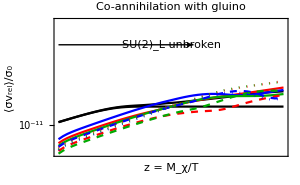
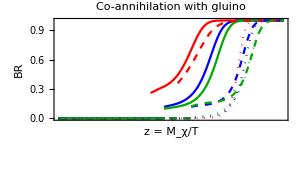

```mathematica
Row[{ListLinePlot[Table[Transpose[Log[10,{ztab,σvTtab[x]}]],{x,states}],Frame->True,FrameLabel->{"z = M_χ/T","⟨σv_rel⟩/σ_0"},
FrameTicks->LogLogTicks[dettaglio1,normale],
PlotLegends->Join[{"σv_tree","S σv"},Table["σv("<>Bname<>")",{Bname,Bnames}]],PlotStyle->{{Black,Thin},Black,Red,Blue,DGreen,{Red,Dashed},{Blue,Dashed},{DGreen,Dashed},{Red,Dotted},{Blue,Dotted},{DGreen,Dotted},Black},PlotLabel->model,Epilog->{Arrow[{{-1,-2.5},{2,-2.5}}],Text[" SU(2)_L unbroken ",{1.5,-2.5},Background->White]},ImageSize->300],
Plot[Evaluate[Table[BR[state,10^lz],{state,Bstates}]],{lz,Log[zmin,10],Log[10,zmax]},Frame->True,FrameLabel->{"z = M_χ/T","BR"},
FrameTicks->LogLinTicks[dettaglio1],
PlotLegends->Table["BR("<>Bname<>")",{Bname,Bnames}],PlotStyle->{Red,Blue,DGreen,{Red,Dashed},{Blue,Dashed},{DGreen,Dashed},{Red,Dotted},{Blue,Dotted},{DGreen,Dotted},Black},PlotLabel->model,Epilog->{Arrow[{{-1,-2.5},{2,-2.5}}],Text[" SU(2)_L unbroken ",{1.5,-2.5},Background->White]},ImageSize->300]}]
```

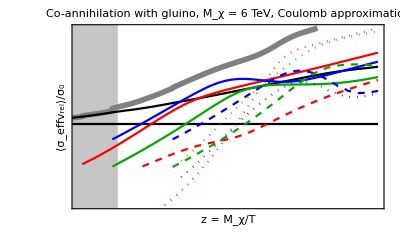

```mathematica
{xmin,xmax,ymin,ymax}={1,4,-2,3};
Plot[Evaluate[Table[Log[10,RσvTeff[state,10^lz]],{state,Join[{"tot"},states]}]],{lz,Log[10,zmin],Log[10,zmax]},Frame->True,FrameLabel->{"
StyleBox[\"z\",\nFontSlant->\"Italic\"] = M_χ/
StyleBox[\"T\",\nFontSlant->\"Italic\"]","⟨σ_effSubscriptBox[
 StyleBox[\"v\",\nFontSlant->\"Italic\"], \"rel\"]⟩/σ_0"},
FrameTicks->LogLogTicks[normale],
Prolog->{If[group===SU2,{Lighter@Lighter@Pink,Rectangle[{Log[10,MDM/Tc],-4},{xmax,4}]},{}],Lighter@Lighter@Gray,Rectangle[{0,-4},{Log[10,25],4}]},
PlotLegends->Map[Style[#,Small,FontFamily->"Times"]&,Join[{"tot","tree","Som"},Bnames]],PlotStyle->{{Gray,Thickness[0.01]},{Black,Thin},Black,Red,Blue,DGreen,{Red,Dashed},{Blue,Dashed},{DGreen,Dashed},{Red,Dotted},{Blue,Dotted},{DGreen,Dotted},Black},PlotLabel->model<>", M_χ = "<>ToString[MDM/1000]<>" TeV, Coulomb approximation",PlotRange->{{xmin,xmax},{ymin,ymax}},Axes->False,
Epilog->If[group===SU2,{Red,Arrow[{{Log[10,MDM/Tc],ymin+0.5},{xmax,ymin+0.5}}],Text[" SU(2)_L broken ",{3,ymin+0.5},Background->Lighter@Lighter@Pink]},{}]]
```

### Relic abundance and (ΔM,Mχ) scan

```mathematica
Mmin=1000.;Mmax=16000;Δmin=0.;Δmax=200;AG=18;PG=18;αe=0.3;Δscan[glu]//Quiet
```

```mathematica
annglu=ListLinePlot[{dtab4m,dtab4p},PlotRange->{{1000,8000},{0,160}},Filling->{1->{2}},PlotStyle->{Blue,Blue},FillingStyle->Blue,AspectRatio->1,Frame->True];
Sannglu=ListLinePlot[{dtab3m,dtab3p},PlotRange->{{1000,8000},{0,160}},Filling->{1->{2}},PlotStyle->{Red,Red},FillingStyle->Red,AspectRatio->1,Frame->True];
totglu=ListLinePlot[{dtab2m,dtab2p},PlotRange->{{1000,16000},{0,200}},Filling->{1->{2}},PlotStyle->{Magenta,Magenta},FillingStyle->Magenta,AspectRatio->1,Frame->True];
totglunp=ListLinePlot[{dtab1mm,dtab1p},PlotRange->{{1000,16000},{0,200}},Filling->{1->{2}},PlotStyle->{Magenta,Magenta},FillingStyle->Magenta,AspectRatio->1,Frame->True];
```

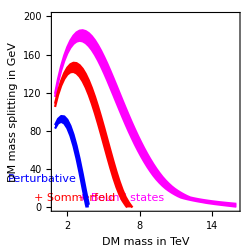

```mathematica
Legend=Show[{Graphics[Text[StyleForm["+ Sommerfeld",Red,Small,Background->None,FontFamily->"Times"],{6000,15},{1,1},{1,-2.4}]],Graphics[Text[StyleForm["+ Bound states",Magenta,Small,Background->None,FontFamily->"Times"],{10000,15},{1,1},{1,-1.7}]],Graphics[Text[StyleForm["Perturbative",Blue,Small,Background->None,FontFamily->"Times"],{2800,35},{1,1},{1,-3}]](*,Graphics[Text[StyleForm["+ Post-confinement\n effects",Darker@Magenta,Small,Background->None,FontFamily->"Times"],{16000,33},{1,1},{1,-0.1}]]*)}];
Gluinoscan=Show[{totglunp,Sannglu,annglu,Legend},Frame->True,FrameLabel->{"DM mass in TeV","DM mass splitting in GeV","Neutralino DM co-annihilating with gluinos"},FrameTicks->{{Automatic,Automatic},{Table[{1000 m,If[Element[m/2,Integers],m],If[Element[m/2,Integers],{0.012,0},{0.006,0}]},{m,1,14,1/2}],Automatic}},ImageSize->250]
```

```mathematica
Export["/Users/Andrea/Dropbox/Finished works/DM bound state/figs/Gluinoscannew_NP.pdf",Gluinoscan]
```

/Users/Andrea/Dropbox/Finished works/DM bound state/figs/Gluinoscannew_NP.pdf

### Tabs α_eff= 1

```mathematica
dtab1m
```

{{1000.,115.624},{1254.24,130.891},{1508.47,143.289},{1762.71,153.316},{2016.95,161.185},{2271.19,167.072},{2525.42,171.178},{2779.66,173.575},{3033.9,174.419},{3288.14,173.823},{3542.37,171.932},{3796.61,168.83},{4050.85,164.685},{4305.08,159.633},{4559.32,153.8},{4813.56,147.292},{5067.8,140.259},{5322.03,132.895},{5576.27,125.221},{5830.51,117.424},{6084.75,109.526},{6338.98,101.746},{6593.22,94.099},{6847.46,86.576},{7101.69,79.3496},{7355.93,72.3545},{7610.17,65.737},{7864.41,59.4198},{8118.64,53.4761},{8372.88,47.8556},{8627.12,42.619},{8881.36,37.8164},{9135.59,33.3661},{9389.83,29.3744},{9644.07,25.8316},{9898.31,22.6401},{10152.5,19.8694},{10406.8,17.5239},{10661.,15.4433},{10915.3,13.5756},{11169.5,11.8783},{11423.7,10.4322},{11678.,9.78093},{11932.2,9.20515},{12186.4,8.68778},{12440.7,8.22299},{12694.9,7.79956},{12949.2,7.41312},{13203.4,7.05834},{13457.6,6.72857},{13711.9,6.42274},{13966.1,6.13884},{14220.3,5.87132},{14474.6,5.62059},{14728.8,5.38679},{14983.1,5.16599},{15237.3,4.95513},{15491.5,4.75636},{15745.8,4.5685},{16000.,4.38654}}

```mathematica
dtab1p
```

{{1000.,118.903},{1254.24,134.81},{1508.47,148.092},{1762.71,159.026},{2016.95,167.813},{2271.19,174.7},{2525.42,179.752},{2779.66,183.161},{3033.9,185.011},{3288.14,185.404},{3542.37,184.477},{3796.61,182.342},{4050.85,179.122},{4305.08,174.858},{4559.32,169.742},{4813.56,163.917},{5067.8,157.452},{5322.03,150.473},{5576.27,143.065},{5830.51,135.447},{6084.75,127.589},{6338.98,119.713},{6593.22,111.858},{6847.46,104.088},{7101.69,96.4576},{7355.93,89.0179},{7610.17,81.8169},{7864.41,74.9392},{8118.64,68.3358},{8372.88,62.0646},{8627.12,56.1404},{8881.36,50.5325},{9135.59,45.2988},{9389.83,40.4306},{9644.07,35.9615},{9898.31,31.8249},{10152.5,28.1819},{10406.8,24.9218},{10661.,21.9756},{10915.3,19.4443},{11169.5,17.2566},{11423.7,15.2989},{11678.,13.5257},{11932.2,11.913},{12186.4,10.4789},{12440.7,9.85489},{12694.9,9.2985},{12949.2,8.79883},{13203.4,8.34756},{13457.6,7.93374},{13711.9,7.55272},{13966.1,7.20251},{14220.3,6.87525},{14474.6,6.57104},{14728.8,6.2883},{14983.1,6.02304},{15237.3,5.77152},{15491.5,5.53519},{15745.8,5.31275},{16000.,5.09886}}

```mathematica
dtab2m
```

{{1000.,115.622},{1254.24,130.887},{1508.47,143.286},{1762.71,153.314},{2016.95,161.183},{2271.19,167.074},{2525.42,171.173},{2779.66,173.578},{3033.9,174.432},{3288.14,173.828},{3542.37,171.927},{3796.61,168.825},{4050.85,164.72},{4305.08,159.631},{4559.32,153.778},{4813.56,147.296},{5067.8,140.263},{5322.03,132.874},{5576.27,125.147},{5830.51,117.399},{6084.75,109.539},{6338.98,101.741},{6593.22,94.0468},{6847.46,86.5577},{7101.69,79.2805},{7355.93,72.3993},{7610.17,65.6893},{7864.41,59.4072},{8118.64,53.4452},{8372.88,47.8527},{8627.12,42.6185},{8881.36,37.801},{9135.59,33.338},{9389.83,29.3361},{9644.07,25.8004},{9898.31,22.6019},{10152.5,19.8169},{10406.8,17.4608},{10661.,15.3622},{10915.3,13.4739},{11169.5,11.7584},{11423.7,10.3444},{11678.,9.5849},{11932.2,8.91064},{12186.4,8.30625},{12440.7,7.75358},{12694.9,7.24088},{12949.2,6.75863},{13203.4,6.31866},{13457.6,5.62929},{13711.9,5.2269},{13966.1,4.87241},{14220.3,4.52381},{14474.6,4.20908},{14728.8,3.90084},{14983.1,3.61289},{15237.3,3.33124},{15491.5,3.06552},{15745.8,2.78336},{16000.,2.52657}}

```mathematica
dtab2p
```

{{1000.,118.9},{1254.24,134.807},{1508.47,148.091},{1762.71,159.027},{2016.95,167.813},{2271.19,174.692},{2525.42,179.748},{2779.66,183.158},{3033.9,185.004},{3288.14,185.404},{3542.37,184.47},{3796.61,182.321},{4050.85,179.102},{4305.08,174.851},{4559.32,169.75},{4813.56,163.906},{5067.8,157.421},{5322.03,150.473},{5576.27,143.031},{5830.51,135.444},{6084.75,127.578},{6338.98,119.75},{6593.22,111.861},{6847.46,104.024},{7101.69,96.4905},{7355.93,88.9686},{7610.17,81.7968},{7864.41,74.9332},{8118.64,68.3097},{8372.88,62.0463},{8627.12,56.1397},{8881.36,50.5361},{9135.59,45.2832},{9389.83,40.4521},{9644.07,35.9397},{9898.31,31.8081},{10152.5,28.163},{10406.8,24.8907},{10661.,21.9247},{10915.3,19.3946},{11169.5,17.1883},{11423.7,15.2204},{11678.,13.4262},{11932.2,11.7946},{12186.4,10.401},{12440.7,9.66648},{12694.9,9.00571},{12949.2,8.40196},{13203.4,7.85291},{13457.6,7.15501},{13711.9,6.66128},{13966.1,6.22061},{14220.3,5.79768},{14474.6,5.41438},{14728.8,5.04552},{14983.1,4.70182},{15237.3,4.37022},{15491.5,4.05795},{15745.8,3.73642},{16000.,3.44154}}

```mathematica
dtab3m={{1000.,105.16477903655662},{1254.2372881355932,117.79003308090623},{1508.4745762711864,127.38137829488478},{1762.7118644067796,134.40111898602512},{2016.9491525423728,139.0496848893578},{2271.186440677966,141.48748968941632},{2525.423728813559,141.85767907125307},{2779.6610169491523,140.30022581943885},{3033.8983050847455,136.93536504785595},{3288.135593220339,131.9333911323116},{3542.372881355932,125.3950167743577},{3796.6101694915255,117.50361457373843},{4050.8474576271187,108.42289854123497},{4305.0847457627115,98.33532510140547},{4559.322033898305,87.45539506806249},{4813.559322033898,76.03309951776347},{5067.796610169491,64.31825938923309},{5322.033898305085,52.621907073115},{5576.271186440678,41.27011903849327},{5830.508474576271,30.62602742671359},{6084.745762711864,21.04359832616466},{6338.983050847458,12.997425061233887},{6593.220338983051,6.706963133998647},{6847.457627118644,1.9005303235726978},{7101.6949152542375,-2.2341329459683403},{7355.932203389831,-5.635400591828642},{7610.169491525424,-8.704925633257423},{7864.406779661017,-11.411235986077898},{8118.64406779661,-13.871260071538261},{8372.881355932204,-16.05666391277926}};
```

```mathematica
dtab3p={{1000.,108.57959724048558},{1254.2372881355932,121.98314254367287},{1508.4745762711864,132.55126310837508},{1762.7118644067796,140.58397662259262},{2016.9491525423728,146.2628851972239},{2271.186440677966,149.8317690784922},{2525.423728813559,151.3646990972649},{2779.6610169491523,150.9965403154508},{3033.8983050847455,148.8475403709355},{3288.135593220339,145.04089649588255},{3542.372881355932,139.70025598097595},{3796.6101694915255,132.9464269381872},{4050.8474576271187,124.918433520221},{4305.0847457627115,115.78142360675373},{4559.322033898305,105.69682428676595},{4813.559322033898,94.84674913974389},{5067.796610169491,83.43423347107061},{5322.033898305085,71.72433380922338},{5576.271186440678,59.94375266031557},{5830.508474576271,48.387088400468336},{6084.745762711864,37.36509686982319},{6338.983050847458,27.223606670831185},{6593.220338983051,18.28352231305733},{6847.457627118644,10.791934153558849},{7101.6949152542375,5.2370309530268},{7355.932203389831,0.7682866961465629},{7610.169491525424,-3.0560208184600244},{7864.406779661017,-6.361990957319131},{8118.64406779661,-9.301912922648713},{8372.881355932204,-11.89771733066153}};
```

```mathematica
dtab4m={{1000.,82.5317777536901},{1254.2372881355932,87.97191305006548},{1508.4745762711864,89.64304199856895},{1762.7118644067796,87.91792487843131},{2016.9491525423728,82.97543917749742},{2271.186440677966,75.06226512096472},{2525.423728813559,64.3587036957886},{2779.6610169491523,51.168622201718996},{3033.8983050847455,35.951403627704806},{3288.135593220339,19.453921849853934},{3542.372881355932,3.5822610173860445},{3796.6101694915255,-9.722865819677029}};
```

```mathematica
dtab4p={{1000.,86.18677089720478},{1254.2372881355932,92.65734003039111},{1508.4745762711864,95.59721679083522},{1762.7118644067796,95.2428245758541},{2016.9491525423728,91.81451200683772},{2271.186440677966,85.44744429100554},{2525.423728813559,76.34531374047592},{2779.6610169491523,64.70402086417477},{3033.8983050847455,50.830998220208116},{3288.135593220339,35.18215628895243},{3542.372881355932,18.522145288731554},{3796.6101694915255,2.789601963967127}};
```

### Tabs α_eff= 0.3

```mathematica
dtab1m
```

{{1000.,115.621},{1254.24,130.889},{1508.47,143.287},{1762.71,153.313},{2016.95,161.182},{2271.19,167.074},{2525.42,171.174},{2779.66,173.575},{3033.9,174.394},{3288.14,173.83},{3542.37,171.918},{3796.61,168.828},{4050.85,164.71},{4305.08,159.641},{4559.32,153.761},{4813.56,147.304},{5067.8,140.27},{5322.03,132.866},{5576.27,125.203},{5830.51,117.388},{6084.75,109.552},{6338.98,101.726},{6593.22,94.0135},{6847.46,86.568},{7101.69,79.3399},{7355.93,72.3404},{7610.17,65.7188},{7864.41,59.4169},{8118.64,53.438},{8372.88,47.8457},{8627.12,42.6281},{8881.36,37.8068},{9135.59,33.3458},{9389.83,29.3449},{9644.07,25.8097},{9898.31,22.6079},{10152.5,19.8201},{10406.8,17.4715},{10661.,15.3753},{10915.3,13.4893},{11169.5,11.7732},{11423.7,10.3587},{11678.,9.61129},{11932.2,8.94372},{12186.4,8.33956},{12440.7,7.78928},{12694.9,7.28082},{12949.2,6.81364},{13203.4,6.37776},{13457.6,5.96969},{13711.9,5.58662},{13966.1,5.22307},{14220.3,4.87968},{14474.6,4.55591},{14728.8,4.2439},{14983.1,3.95619},{15237.3,3.66537},{15491.5,3.39656},{15745.8,3.13111},{16000.,2.8817}}

```mathematica
dtab1p
```

{{1000.,118.9},{1254.24,134.809},{1508.47,148.09},{1762.71,159.024},{2016.95,167.812},{2271.19,174.696},{2525.42,179.751},{2779.66,183.161},{3033.9,184.99},{3288.14,185.402},{3542.37,184.47},{3796.61,182.333},{4050.85,179.079},{4305.08,174.867},{4559.32,169.746},{4813.56,163.917},{5067.8,157.418},{5322.03,150.502},{5576.27,143.085},{5830.51,135.434},{6084.75,127.662},{6338.98,119.747},{6593.22,111.84},{6847.46,104.074},{7101.69,96.4419},{7355.93,88.9858},{7610.17,81.8265},{7864.41,74.9142},{8118.64,68.3362},{8372.88,62.0499},{8627.12,56.1257},{8881.36,50.5463},{9135.59,45.2909},{9389.83,40.4192},{9644.07,35.9472},{9898.31,31.8108},{10152.5,28.165},{10406.8,24.8964},{10661.,21.934},{10915.3,19.4031},{11169.5,17.2008},{11423.7,15.2272},{11678.,13.4383},{11932.2,11.8088},{12186.4,10.411},{12440.7,9.68291},{12694.9,9.0281},{12949.2,8.43641},{13203.4,7.89359},{13457.6,7.39224},{13711.9,6.92605},{13966.1,6.48896},{14220.3,6.08033},{14474.6,5.69643},{14728.8,5.33054},{14983.1,4.99247},{15237.3,4.65733},{15491.5,4.3462},{15745.8,4.04269},{16000.,3.75764}}

```mathematica
dtab2m
```

{{1000.,115.622},{1254.24,130.887},{1508.47,143.286},{1762.71,153.314},{2016.95,161.183},{2271.19,167.074},{2525.42,171.173},{2779.66,173.578},{3033.9,174.432},{3288.14,173.828},{3542.37,171.927},{3796.61,168.825},{4050.85,164.72},{4305.08,159.631},{4559.32,153.778},{4813.56,147.296},{5067.8,140.263},{5322.03,132.874},{5576.27,125.147},{5830.51,117.399},{6084.75,109.539},{6338.98,101.741},{6593.22,94.0468},{6847.46,86.5577},{7101.69,79.2805},{7355.93,72.3993},{7610.17,65.6893},{7864.41,59.4072},{8118.64,53.4452},{8372.88,47.8527},{8627.12,42.6185},{8881.36,37.801},{9135.59,33.338},{9389.83,29.3361},{9644.07,25.8004},{9898.31,22.6019},{10152.5,19.8169},{10406.8,17.4608},{10661.,15.3622},{10915.3,13.4739},{11169.5,11.7584},{11423.7,10.3163},{11678.,9.43317},{11932.2,8.6391},{12186.4,7.92127},{12440.7,7.25311},{12694.9,6.62539},{12949.2,6.03343},{13203.4,5.49765},{13457.6,4.89206},{13711.9,4.40378},{13966.1,3.97215},{14220.3,3.5241},{14474.6,3.12774},{14728.8,2.71601},{14983.1,2.33897},{15237.3,1.94912},{15491.5,1.59073},{15745.8,1.18853},{16000.,0.835267}}

```mathematica
dtab2p
```

{{1000.,118.9},{1254.24,134.807},{1508.47,148.091},{1762.71,159.027},{2016.95,167.813},{2271.19,174.692},{2525.42,179.748},{2779.66,183.158},{3033.9,185.004},{3288.14,185.404},{3542.37,184.47},{3796.61,182.321},{4050.85,179.102},{4305.08,174.851},{4559.32,169.75},{4813.56,163.906},{5067.8,157.421},{5322.03,150.473},{5576.27,143.031},{5830.51,135.444},{6084.75,127.578},{6338.98,119.75},{6593.22,111.861},{6847.46,104.024},{7101.69,96.4905},{7355.93,88.9686},{7610.17,81.7968},{7864.41,74.9332},{8118.64,68.3097},{8372.88,62.0463},{8627.12,56.1397},{8881.36,50.5361},{9135.59,45.2832},{9389.83,40.4521},{9644.07,35.9397},{9898.31,31.8081},{10152.5,28.163},{10406.8,24.8907},{10661.,21.9247},{10915.3,19.3946},{11169.5,17.1883},{11423.7,15.2204},{11678.,13.4262},{11932.2,11.7946},{12186.4,10.3795},{12440.7,9.51273},{12694.9,8.72329},{12949.2,7.99641},{13203.4,7.33513},{13457.6,6.65262},{13711.9,6.06649},{13966.1,5.54063},{14220.3,5.01605},{14474.6,4.54535},{14728.8,4.0717},{14983.1,3.63498},{15237.3,3.19445},{15491.5,2.78623},{15745.8,2.34538},{16000.,1.95142}}

### Cross sections plot

```mathematica
MDM=6000;Calcolaσv[glu];//Quiet
```

Interpolation::innd: First argument in Transpose[{{0.1,0.125893,0.158489,0.199526,0.251189,0.316228,0.398107,0.501187,0.630957,0.794328,1.,1.25893,1.58489,1.99526,2.51189,«21»,398.107,501.187,630.957,794.328,1000.,1258.93,1584.89,1995.26,2511.89,3162.28,3981.07,5011.87,6309.57,7943.28,«1»},ThermalAverage2[Sann]}] does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

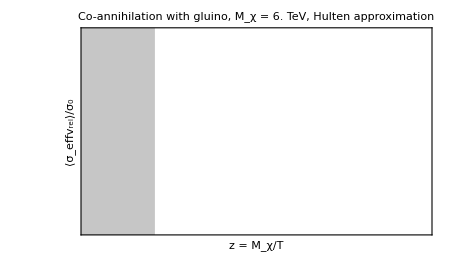

```mathematica
{xmin,xmax,ymin,ymax}={1,3,-2,3};plot5glu=Plot[Evaluate[Table[Log[10,RσvTeff[state,10^lz]],{state,Join[{"tot"},states]}]],{lz,Log[10,zmin],Log[10,zmax]},Frame->True,FrameLabel->{"z = M_χ/T","⟨σ_effv_rel⟩/σ_0"},
FrameTicks->LogLogTicks[normale],
Prolog->{If[group===SU2,{Lighter@Lighter@Pink,Rectangle[{Log[10,MDM/Tc],-4},{xmax,4}]},{}],Lighter@Lighter@Gray,Rectangle[{0,-4},{Log[10,25],4}]},
PlotLegends->Placed[Map[Style[#,Small,FontFamily->"Times"]&,Join[{"tot","tree","Som"},Bnames]],{0.269,0.749}],PlotStyle->{{Gray,Thickness[0.01]},{Black,Thin},Black,Red,Blue,DGreen,{Red,Dashed},{Blue,Dashed},{DGreen,Dashed},{Red,Dotted},{Blue,Dotted},{DGreen,Dotted},Black},PlotLabel->model<>", M_χ = "<>ToString[MDM/1000.]<>" TeV, Hulten approximation",PlotRange->{{xmin,xmax},{ymin,ymax}},Axes->False,ImageSize->450,
Epilog->If[group===SU2,{Red,Arrow[{{Log[10,MDM/Tc],ymin+0.5},{xmax,ymin+0.5}}],Text[" SU(2)_L broken ",{3,ymin+0.5},Background->Lighter@Lighter@Pink]},{}]]
```

```mathematica
Export["/Users/Andrea/Dropbox/DM bound state/figs/Gluinocross.pdf",plot5glu]
```

Export::nodir: Directory /Users/Andrea/Dropbox/DM bound state/figs/ does not exist.

Export::noopen: Cannot open /Users/Andrea/Dropbox/DM bound state/figs/Gluinocross.pdf.

$Failed

### Numerical Binding energy

#### Inits

defV[{{color ,  spin S of DM1+DM2}}].  Negative V means attractive force.

```mathematica
Clear[T,M,ΔM];ThisParticle="Fermion color octet";Particle=Fermion;Colored=True;n=8;Y=0;
defV[{{1,0}}]:=(Clear[r,z];dim=1;sys={{1,0}};αeff=-3  α3[1/r];V={{2ΔM+ αeff/r  Exp[-MgT[T] r]}};);

defV[{{8,0}}]:=(Clear[r,z];dim=1sys={{3,0}};αeff=-3/2 g3I[1/r]^2/(4π);V={{2ΔM+ αeff/r  Exp[-MgT[T] r]}};RΓ={{1}};);
defV[{{8,1}}]:=(Clear[r,z];dim=1;sys={{3,1}};αeff=-3/2 g3I[1/r]^2/(4π);V={{2ΔM+ αeff/r  Exp[-MgT[T] r]}};RΓ={{1}};);
defV[{{27,0}}]:=(Clear[r,z];dim=1;sys={{5,0}};αeff=g3I[1/r]^2/(4π);V={{2ΔM+ αeff/r  Exp[-MgT[T] r]}};RΓ={{1}};);
systab={{{1,0}},{{8,0}},{{27,0}},{{8,1}}};
systabs=Flatten[systab,1];
```

#### Spectrum

```mathematica
α3MZ
```

α3MZ

```mathematica
l=0;M=MDM=6000;ΔM=0;Λ=300;Clear[r];Calcolaα3Mt;
```

```mathematica
ScanSpectrumT[{{1,0}},50,20,0.,600.];
```

```mathematica
Btab[1,0]
```

Btab[1,0]

```mathematica
Btab[2,0]
```

Btab[2,0]

```mathematica
BS[110]={{0.,185.14098075594535},{12.244897959183673,177.787555908853},{24.489795918367346,170.6513302749587},{36.73469387755102,163.72452290448564},{48.97959183673469,157.00006098966944},{61.224489795918366,150.4714755739089},{73.46938775510203,144.13281799065825},{85.71428571428571,137.97859193995558},{97.95918367346938,132.00369757891886},{110.20408163265307,126.20338499038918},{122.44897959183673,120.57321507538806},{134.69387755102042,115.10902639575481},{146.93877551020407,109.80690683920099},{159.18367346938777,104.66316923187526},{171.42857142857142,99.67433021178402},{183.67346938775512,94.83709181795363},{195.91836734693877,90.14832535845568},{208.16326530612244,85.6050572038413},{220.40816326530614,81.2044562176313},{232.6530612244898,76.9438225866289},{244.89795918367346,72.82057785449942},{257.1428571428571,68.83225599427294},{269.38775510204084,64.97649538135916},{281.6326530612245,61.2510315492613},{293.87755102040813,57.65369062636384},{306.12244897959187,54.18238336465174},{318.36734693877554,50.8350996801588},{330.61224489795916,47.60990363026422},{342.85714285714283,44.504928754474896},{355.1020408163265,41.51837370245551},{367.34693877551024,38.648498064328784},{379.5918367346939,35.89361830266229},{391.83673469387753,33.25210366073052},{404.0816326530612,30.722371884954445},{416.3265306122449,28.302884548301673},{428.57142857142856,25.992141692497324},{440.8163265306123,23.78867541814819},{453.0612244897959,21.691041942973026},{465.3061224489796,19.697811522859414},{477.55102040816325,17.8075554996615},{489.7959183673469,16.018829625681523},{502.04081632653066,14.330152755308736},{514.2857142857142,12.739980046826233},{526.530612244898,11.246670056999571},{538.7755102040817,9.848445622368743},{551.0204081632653,8.543349274443582},{563.265306122449,7.329195147285529},{575.5102040816327,6.203520815015441},{587.7551020408163,5.163544001247031},{600.,4.20613023216829}};
```

```mathematica
BS[120]={{0.,46.600353095599495},{12.244897959183673,39.56145277080304},{24.489795918367346,33.307874846189534},{36.73469387755102,27.756295324163975},{48.97959183673469,22.838792325261725},{61.224489795918366,18.497436874458078},{73.46938775510203,14.680815584271706},{85.71428571428571,11.341682871456593},{97.95918367346938,8.435398015415974},{110.20408163265307,5.919004293240969},{122.44897959183673,3.750870859697293},{134.69387755102042,1.8907993192187824},{146.93877551020407,0.3004464415951267}};
```

```mathematica
l=1;ΔM=0;Λ=30;Clear[r];ScanSpectrumT[{{1,0}},50,20,0.,600.];
```

```mathematica
θsq[x_]:=If[x<0,Null,x^2]
Eb[αeff_,n_,l_,Mχ_,MV_]:= (αeff^2 Mχ)/(4 n^2)θsq[1-1.9 n^2 MV/(αeff Mχ)-1.75 n^2(MV/(αeff Mχ))^2 l(l+1)];
```

```mathematica
Bstates={110,120};
```

```mathematica
Clear[T]
Mχ=6000.;
ps=Flatten[Outer[List,{Thickness[0.01],Thickness[0.005]},{Blue,Red,{Red,Dashed}}],1];
Mχ=6000.;xmax=600;ymax=200;
EBHulten=Plot[Evaluate[Table[{Eb[λ α3MZ,1,0,Mχ,MgT[T]],Eb[λ α3MZ,2,0,Mχ,MgT[T]],Eb[λ α3MZ,2,1,Mχ,MgT[T]]},{λ,{3,3/2}}]],{T,0,xmax},Frame->True,FrameLabel->{"Temperature in GeV","Binding energy E_B in GeV","z = M_χ/T",""},PlotRange->{0,ymax},
Prolog->{Lighter@Gray,Rectangle[{xmax,0},{Mχ/25,ymax}]},
Epilog->{Gray,Text[Style["Thermal equilibrium",Small],{400,10}],Black,
Text["Color octet (gluino)\nM_χ = 6 TeV",{450,160}],Blue,Text["1s_1",{200,Eb[3 α3MZ,1,0,Mχ,MgT[200]]},Background->White],
Text["1s_8",{200,Eb[3/2 α3MZ,1,0,Mχ,MgT[200]]},Background->White],Red,
Text["2s_1",{100,Eb[3 α3MZ,2,0,Mχ,MgT[100]]},Background->White]},FrameTicks->{{Automatic,Automatic},{Automatic,Table[{Mχ/z,z},{z,{10,25,50,100}}]}},PlotStyle->ps,ImageSize->250]
```

-Graphics-

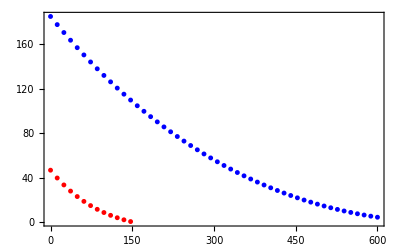

```mathematica
EBNumerics=ListPlot[Table[Sort[BS[state]],{state,Bstates}],Frame->True,PlotMarkers->{{●,5},{●,5},{■,5},{●,5},{▲,5},{●,5},{■,5},{▲,5}},PlotStyle->{Blue,Red,Blue,Red,Red,Red,Red,Darker@Green}]
```

```mathematica
Show[EBHulten,EBNumerics]
```

-Graphics-

```mathematica
MgT[0]
```

MgT[0]

```mathematica
9/4 α3MZ^2 MDM
```

13500 α3MZ^2

## Neutralino coann. with squarks

### Initializations

```mathematica
model="Co-annihilation with a squark";group=SU3;gχ1=2;gχ2=6;Particle=Scalar;Calcolaα3Mt;
Clear[σv,λ,CJ,CT,z,A,S,Bstates,Bnames,Γann,Γdecay];
αe=0.3;Λ=0.27;
λ[1]=4/3;dim[1]=1;
λ[8]=-1/6;dim[8]=8; 
Attributes[CJ]={Orderless};
CJ[1,8]=√(4/3);CT[1,8]=-3/2 √(4/3);CT[8,1]=-CT[1,8];
Bstates={{1,0,1,0},{1,0,2,0},{1,0,2,1}};
Bnames={"1s_1","2s_1","2p_1"};
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

```mathematica
Calcolaσv[sq]:=(ClearAll[σ0,σv,Γann,σvTI,RσvTeff];σ0=(π α3[MDM]^2)/MDM^2;σ1=(π α3[(2/z)^(1/2) MDM]^2)/MDM^2;
ζ=α3[(2/z)^(1/2) MDM]/vrel;Somm[channel_]:=Sommerfeld[vrel/2,-λ[channel]α3[(2/z)^(1/2) MDM],MgT[MDM/z],MDM];
σv["ann"]=7/27 σ0;σv["Sann"]=σv["ann"](2/7 Somm[1]+5/7 Somm[8]);
Attributes[CJ]={Orderless};
CJ[1,8]=√(4/3);CT[1,8]=-3/2 √(4/3);CT[8,1]=-CT[1,8];
σvbsf[ζ_,Iin_->{If_,Spin_,n_,l_}]:=(Bnum[λ[If] α3[(2/z)^(1/2) MDM],n,l,MDM,MgT[MDM/z]]+(α3[(2/z)^(1/2) MDM]/(2 ζ))^2 MDM)/((λ[If]^2 α3[(2/z)^(1/2) MDM]^2 MDM)/(4 n^2)+(α3[(2/z)^(1/2) MDM]/(2 ζ))^2 MDM)*σvbsf[ζ,λ[Iin],{λ[If],Spin,n,l},CJ[Iin,If],CT[Iin,If]];
σv[{1,0,1,0}]=σvbsf[ζ,8->{1,0,1,0}];
σv[{1,0,2,0}]=σvbsf[ζ,8->{1,0,2,0}];
σv[{1,0,2,1}]=σvbsf[ζ,8->{1,0,2,1}];
Γann[{1,0,1,0}]=32 α3[MDM]^2 α3[0.1 MDM]^3 MDM/81;
Γann[{1,0,2,0}]=4 α3[MDM]^2 α3[0.1 MDM]^3 MDM/81;
Γann[{1,0,2,1}]=0;Γdecay[{1,0,2,1}]= α3[α3MZ MDM]^6 MDM;
ztab=Table[10^lz,{lz,1,3,0.1}];zmax=Max[ztab];zmin=Min[ztab];
states=Join[{"ann","Sann"},Bstates];Clear[σvTtab];
Do[σvTtab[state]=ThermalAverage2[state];,{state,states}];
σvTtab["tot"]=Sum[σvTtab[state],{state,Drop[states,1]}];
Do[σvTI[state]=Interpolation[Transpose[{ztab,σvTtab[state]}],InterpolationOrder->1],{state,Join[{"tot"},states]}];
Clear[BR,EB,EBQ,RσvTeff];
Do[DefineStateGlu[state];,{state,Bstates}];
RσvTeff["ann",z_]:=σvTI["ann"][z]/σ0;
RσvTeff["Sann",z_]:=σvTI["Sann"][z]/σ0;
RσvTeff["Btot",z_]:=Sum[RσvTeff[state,z],{state,Bstates}];
RσvTeff["tot",z_]:=RσvTeff["Sann",z]+RσvTeff["Btot",z];);
```

### Relic abundance and (ΔM,Mχ) scan

```mathematica
Mmin=100.;Mmax=3500.;Δmin=0.;Δmax=40;AG=18;PG=18;Δscan[sq]//Quiet
```

```mathematica
annsq=ListLinePlot[{dtab4m,dtab4p},PlotRange->{{200,3000},{0,35}},Filling->{1->{2}},PlotStyle->{Blue,Blue},FillingStyle->Blue,AspectRatio->1,Frame->True];
Sannsq=ListLinePlot[{dtab3m,dtab3p},PlotRange->{{200,3500},{0,35}},Filling->{1->{2}},PlotStyle->{Red,Red},FillingStyle->Red,AspectRatio->1,Frame->True];
totsq=ListLinePlot[{dtab2m,dtab2p},PlotRange->{{15,3500},{0,35}},Filling->{1->{2}},PlotStyle->{Magenta,Magenta},FillingStyle->Magenta,AspectRatio->1,Frame->True];
totsqnp=ListLinePlot[{dtab2m,dtab1p},PlotRange->{{15,3500},{0,35}},Filling->{1->{2}},PlotStyle->{Magenta,Magenta},FillingStyle->Magenta,AspectRatio->1,Frame->True];
```

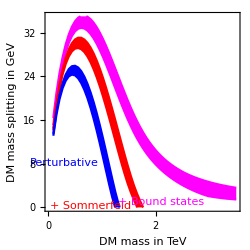

```mathematica
Legendsquark=Show[{Graphics[Text[StyleForm["+ Sommerfeld",Red,Small,Background->None,FontFamily->"Times"],{1550,1.2},{1,1},{1,-2.9}]],Graphics[Text[StyleForm["+ Bound states",Magenta,Small,Background->None,FontFamily->"Times"],{2900,2},{1,1},{1,-0.4}]],Graphics[Text[StyleForm["Perturbative",Blue,Small,Background->None,FontFamily->"Times"],{950,9},{1,1},{1,-3.6}]](*,Graphics[Text[StyleForm["+ Post-confinement \n effects",Darker@Magenta,Small,Background->None,FontFamily->"Times"],{3500,6.5},{1,1},{1,-0.4}]]*)}];
squarkscan=Show[{totsqnp,Sannsq,annsq,Legendsquark},Frame->True,FrameLabel->{"DM mass in TeV","DM mass splitting in GeV","Neutralino DM co-annihilating with squarks"},FrameTicks->{{Automatic,Automatic},{Table[{1000 m,If[Element[m,Integers],m],If[Element[m,Integers],{0.012,0},{0.009,0}]},{m,0,5,1/4}],Automatic}},FrameTicksStyle->Directive[Black,9],ImageSize->250]
```

```mathematica
Export["/Users/Andrea/Dropbox/Finished works/DM bound state/figs/Squarkscannew_NP.pdf",squarkscan]
```

/Users/Andrea/Dropbox/Finished works/DM bound state/figs/Squarkscannew_NP.pdf

```mathematica
Export["/Users/Andrea/Desktop/Squarkscannew_AM.pdf",squarkscan]
```

/Users/Andrea/Desktop/Squarkscannew_AM.pdf

### Tabs

```mathematica
dtab1m={{100.,16.08283917812803},{157.6271186440678,20.45394537673505},{215.25423728813558,23.91879205356568},{272.8813559322034,26.658042235032678},{330.50847457627117,28.813614513430416},{388.135593220339,30.467310445697418},{445.7627118644068,31.673640516922923},{503.3898305084746,32.4972150174054},{561.0169491525423,32.9668024960011},{618.6440677966102,33.12126661857825},{676.271186440678,32.994547425503406},{733.8983050847457,32.612754660446654},{791.5254237288136,32.002347101491026},{849.1525423728814,31.193318081748057},{906.7796610169491,30.210152321372487},{964.4067796610169,29.07708089982147},{1022.0338983050848,27.83049775008419},{1079.6610169491526,26.486478470898263},{1137.2881355932204,25.073277265903744},{1194.915254237288,23.6281341924787},{1252.542372881356,22.171146869675958},{1310.1694915254236,20.717975750057413},{1367.7966101694915,19.306332371841254},{1425.4237288135594,17.94813668561532},{1483.0508474576272,16.658700560903366},{1540.677966101695,15.458741296567622},{1598.3050847457628,14.344832102544828},{1655.9322033898304,13.32339224193773},{1713.5593220338983,12.39038214647202},{1771.1864406779662,11.548035163966226},{1828.8135593220338,10.782075068555228},{1886.440677966102,10.084577819661286},{1944.0677966101696,9.465726539578707},{2001.6949152542372,8.898289680474454},{2059.322033898305,8.377762831846464},{2116.9491525423728,7.914361518314653},{2174.576271186441,7.491640300561457},{2232.2033898305085,7.103499684737283},{2289.830508474576,6.744835519366341},{2347.4576271186443,6.415209750455594},{2405.084745762712,6.118933737689318},{2462.7118644067796,5.849235525870119},{2520.338983050847,5.6016661852155},{2577.966101694915,5.372795379001679},{2635.593220338983,5.160513794703596},{2693.2203389830506,4.962533713766024},{2750.8474576271187,4.779158156287101},{2808.4745762711864,4.60712294937269},{2866.1016949152545,4.447203232421895},{2923.728813559322,4.296475682462154},{2981.35593220339,4.157407965956694},{3038.983050847458,4.0297367827064425},{3096.6101694915255,3.9103573943702616},{3154.237288135593,3.7982674677366566},{3211.864406779661,3.6931531920644325},{3269.4915254237285,3.5940397440371457},{3327.1186440677966,3.500860470260453},{3384.7457627118642,3.413033588196571},{3442.3728813559323,3.3306731000304355},{3500.,3.252564110669747}};
```

```mathematica
dtab1p={{100.,16.389369607080898},{157.6271186440678,20.94624132034799},{215.25423728813558,24.60071088794464},{272.8813559322034,27.518609441912037},{330.50847457627117,29.858355281321842},{388.135593220339,31.687226458324844},{445.7627118644068,33.08290680269259},{503.3898305084746,34.08660718176426},{561.0169491525423,34.74130266648848},{618.6440677966102,35.07862537185623},{676.271186440678,35.13061267408581},{733.8983050847457,34.924251473869255},{791.5254237288136,34.48425634096119},{849.1525423728814,33.83156243613436},{906.7796610169491,32.9976344018469},{964.4067796610169,31.99694791152958},{1022.0338983050848,30.859808707841058},{1079.6610169491526,29.60416096114733},{1137.2881355932204,28.26429107247095},{1194.915254237288,26.846549006787477},{1252.542372881356,25.390006474766523},{1310.1694915254236,23.920703601722586},{1367.7966101694915,22.44329922995231},{1425.4237288135594,21.01305741240089},{1483.0508474576272,19.596555279279926},{1540.677966101695,18.261304545039966},{1598.3050847457628,16.989749868780983},{1655.9322033898304,15.814312460772975},{1713.5593220338983,14.71349764838282},{1771.1864406779662,13.70558800289059},{1828.8135593220338,12.78318813181003},{1886.440677966102,11.942380810243963},{1944.0677966101696,11.181226581258414},{2001.6949152542372,10.485053727942296},{2059.322033898305,9.856151116740312},{2116.9491525423728,9.28375010291236},{2174.576271186441,8.759624475655839},{2232.2033898305085,8.279710858807528},{2289.830508474576,7.846398848474786},{2347.4576271186443,7.449859491455444},{2405.084745762712,7.084475585825984},{2462.7118644067796,6.744158564820494},{2520.338983050847,6.429869282396914},{2577.966101694915,6.1462501126801525},{2635.593220338983,5.889002826524715},{2693.2203389830506,5.649996840123197},{2750.8474576271187,5.429344653644463},{2808.4745762711864,5.223694347180575},{2866.1016949152545,5.032545418769203},{2923.728813559322,4.853153212611352},{2981.35593220339,4.68580886301443},{3038.983050847458,4.5287944297557114},{3096.6101694915255,4.381615683687705},{3154.237288135593,4.242797325813145},{3211.864406779661,4.115878476579483},{3269.4915254237285,3.9975438493966777},{3327.1186440677966,3.8865997732371285},{3384.7457627118642,3.7821655163319137},{3442.3728813559323,3.6843469849583967},{3500.,3.591784589701609}};
```

```mathematica
dtab1mm={{100.,15.274428847453727},{157.6271186440678,19.87804010148125},{215.25423728813558,23.467255363837737},{272.8813559322034,26.306547205350395},{330.50847457627117,28.518417929100107},{388.135593220339,30.208162552182035},{445.7627118644068,31.440226957408534},{503.3898305084746,32.28188066671214},{561.0169491525423,32.76399087561714},{618.6440677966102,32.92698942873826},{676.271186440678,32.80309061602982},{733.8983050847457,32.42261721103403},{791.5254237288136,31.811167732185673},{849.1525423728814,30.99749793489119},{906.7796610169491,30.006622267600193},{964.4067796610169,28.86705859061106},{1022.0338983050848,27.60517609938338},{1079.6610169491526,26.243639770163814},{1137.2881355932204,24.81458881694906},{1194.915254237288,23.344258707858707},{1252.542372881356,21.853107682606193},{1310.1694915254236,20.386288389977064},{1367.7966101694915,18.92928047621009},{1425.4237288135594,17.540393483282127},{1483.0508474576272,16.21468920167612},{1540.677966101695,14.966206064586386},{1598.3050847457628,13.808838124853306},{1655.9322033898304,12.74396639708375},{1713.5593220338983,11.76953821074764},{1771.1864406779662,10.878735167896606},{1828.8135593220338,10.070346946778992},{1886.440677966102,9.332252427671612},{1944.0677966101696,8.659837399897546},{2001.6949152542372,8.047304211347324},{2059.322033898305,7.485177548480231},{2116.9491525423728,6.970541321602299},{2174.576271186441,6.495432652689181},{2232.2033898305085,6.060326288719808},{2289.830508474576,5.66256553960802},{2347.4576271186443,5.295243876365979},{2405.084745762712,4.955389006185617},{2462.7118644067796,4.638921133342513},{2520.338983050847,4.344263361809755},{2577.966101694915,4.0830826810341305},{2635.593220338983,3.8543450077751316},{2693.2203389830506,3.6430460153255426},{2750.8474576271187,3.4434615469489223},{2808.4745762711864,3.268597171094722},{2866.1016949152545,3.10284014742131},{2923.728813559322,2.9481708270347315},{2981.35593220339,2.804339693182075},{3038.983050847458,2.6688928399120964},{3096.6101694915255,2.5431928148108},{3154.237288135593,2.4246650779552636},{3211.864406779661,2.314474623089629},{3269.4915254237285,2.209107258776234},{3327.1186440677966,2.112191215250113},{3384.7457627118642,2.0270786668519993},{3442.3728813559323,1.9497464684029433},{3500.,1.8753077710473633}};
```

```mathematica
dtab2m={{100.,15.090418961467332},{157.6271186440678,19.777068230182294},{215.25423728813558,23.3927334246123},{272.8813559322034,26.250792775476466},{330.50847457627117,28.47235667486005},{388.135593220339,30.168086247961984},{445.7627118644068,31.40466839561218},{503.3898305084746,32.24899787501051},{561.0169491525423,32.73366464860225},{618.6440677966102,32.89694699480937},{676.271186440678,32.77438592800649},{733.8983050847457,32.39301404361852},{791.5254237288136,31.78181866903206},{849.1525423728814,30.967730729476177},{906.7796610169491,29.975596167514645},{964.4067796610169,28.83573308031171},{1022.0338983050848,27.569810121378158},{1079.6610169491526,26.205903968039802},{1137.2881355932204,24.771208212584582},{1194.915254237288,23.301206905444104},{1252.542372881356,21.807947150661104},{1310.1694915254236,20.327685098262897},{1367.7966101694915,18.87062623730033},{1425.4237288135594,17.47429479973453},{1483.0508474576272,16.1374994499442},{1540.677966101695,14.891967222276914},{1598.3050847457628,13.720649599839621},{1655.9322033898304,12.64742110867071},{1713.5593220338983,11.66458783046846},{1771.1864406779662,10.762869595929237},{1828.8135593220338,9.945765818509464},{1886.440677966102,9.195204612737763},{1944.0677966101696,8.510850002844403},{2001.6949152542372,7.884980679266515},{2059.322033898305,7.307433281562601},{2116.9491525423728,6.775938563921276},{2174.576271186441,6.283413893806754},{2232.2033898305085,5.828538455923376},{2289.830508474576,5.405024857522212},{2347.4576271186443,5.0119241360180045},{2405.084745762712,4.6441057833151875},{2462.7118644067796,4.300876595447133},{2520.338983050847,3.9799701641732184},{2577.966101694915,3.679892460448859},{2635.593220338983,3.4007354393433307},{2693.2203389830506,3.138532725351513},{2750.8474576271187,2.892524849214925},{2808.4745762711864,2.6595810007142786},{2866.1016949152545,2.4424161065760726},{2923.728813559322,2.2451441139520716},{2981.35593220339,2.0746031328798105},{3038.983050847458,1.9778453455808835},{3096.6101694915255,1.8895866763014781},{3154.237288135593,1.8071020353911587},{3211.864406779661,1.7333846558844321},{3269.4915254237285,1.6631697087175579},{3327.1186440677966,1.6006955821087439},{3384.7457627118642,1.5574824911254328},{3442.3728813559323,1.508244055079608},{3500.,1.4578481163471817}};
```

```mathematica
dtab2p={{100.,15.460064872891639},{157.6271186440678,20.2923251609352},{215.25423728813558,24.103579814421476},{272.8813559322034,27.119551951540636},{330.50847457627117,29.52161540389669},{388.135593220339,31.40043967956928},{445.7627118644068,32.828364172181125},{503.3898305084746,33.85081385052681},{561.0169491525423,34.52240257272493},{618.6440677966102,34.869792778686836},{676.271186440678,34.92823301611923},{733.8983050847457,34.724572705412044},{791.5254237288136,34.28448503620996},{849.1525423728814,33.63060744967191},{906.7796610169491,32.790700787199164},{964.4067796610169,31.78214177916938},{1022.0338983050848,30.63664812982005},{1079.6610169491526,29.368867163913922},{1137.2881355932204,28.010297189283293},{1194.915254237288,26.57908519947497},{1252.542372881356,25.091718109840908},{1310.1694915254236,23.60026065331759},{1367.7966101694915,22.094607391869925},{1425.4237288135594,20.619681781450268},{1483.0508474576272,19.176432664567372},{1540.677966101695,17.800126245894003},{1598.3050847457628,16.479173294288078},{1655.9322033898304,15.259730670174804},{1713.5593220338983,14.115431557099889},{1771.1864406779662,13.058734652567734},{1828.8135593220338,12.089556670771756},{1886.440677966102,11.196094802750173},{1944.0677966101696,10.381400942667522},{2001.6949152542372,9.63677127538883},{2059.322033898305,8.94983946118832},{2116.9491525423728,8.319119352777587},{2174.576271186441,7.737400983020512},{2232.2033898305085,7.200554358678944},{2289.830508474576,6.701485244183085},{2347.4576271186443,6.238037174382734},{2405.084745762712,5.807053326977713},{2462.7118644067796,5.404560431836367},{2520.338983050847,5.029378234357881},{2577.966101694915,4.676618816269255},{2635.593220338983,4.346347063199207},{2693.2203389830506,4.037476758846161},{2750.8474576271187,3.7501722186412594},{2808.4745762711864,3.4799639150895114},{2866.1016949152545,3.2258433777993303},{2923.728813559322,2.9899710785014832},{2981.35593220339,2.763610161434687},{3038.983050847458,2.5544937251502797},{3096.6101694915255,2.3578829381358446},{3154.237288135593,2.168650634552909},{3211.864406779661,2.0444817930502257},{3269.4915254237285,1.9537158301244721},{3327.1186440677966,1.8737993370880057},{3384.7457627118642,1.80684647016987},{3442.3728813559323,1.7429590889840036},{3500.,1.6800487575611882}};
```

```mathematica
dtab3m={{100.,14.102162101007313},{157.6271186440678,18.482156191769892},{215.25423728813558,21.83483602228468},{272.8813559322034,24.384852354772327},{330.50847457627117,26.303242647290688},{388.135593220339,27.679848370990435},{445.7627118644068,28.5918538625283},{503.3898305084746,29.084747921196847},{561.0169491525423,29.205809081881817},{618.6440677966102,28.989977235556285},{676.271186440678,28.46729088709122},{733.8983050847457,27.664217024149462},{791.5254237288136,26.609980010635216},{849.1525423728814,25.32701915985616},{906.7796610169491,23.84503398572711},{964.4067796610169,22.186036105554216},{1022.0338983050848,20.377273495356516},{1079.6610169491526,18.447453117582672},{1137.2881355932204,16.42535479652123},{1194.915254237288,14.343070614370731},{1252.542372881356,12.234867487944358},{1310.1694915254236,10.138256009790513},{1367.7966101694915,8.095524311627537},{1425.4237288135594,6.152397431355678},{1483.0508474576272,4.362473795091192},{1540.677966101695,2.778614914837929},{1598.3050847457628,1.3717348347138578},{1655.9322033898304,0.11076118709011472},{1713.5593220338983,-1.0199890923315686},{1771.1864406779662,-2.0322691062995375},{1828.8135593220338,-2.9665011721115757},{1886.440677966102,-3.7628750020076267},{1944.0677966101696,-4.542723307078465},{2001.6949152542372,-5.188165897236126},{2059.322033898305,-5.895067570443903},{2116.9491525423728,-6.4232380757352505},{2174.576271186441,-6.998099054518405},{2232.2033898305085,-7.50599916698288},{2289.830508474576,-8.017333300841452},{2347.4576271186443,-8.409973572471872},{2405.084745762712,-8.83686226143296},{2462.7118644067796,-9.209515250764694},{2520.338983050847,-9.559256687868494},{2577.966101694915,-9.892388357648146},{2635.593220338983,-10.181656603175464},{2693.2203389830506,-10.53674139371736},{2750.8474576271187,-10.93459511794672},{2808.4745762711864,-11.157968031958724},{2866.1016949152545,-11.386542445592596},{2923.728813559322,-11.643352959337738},{2981.35593220339,-11.921843651678197},{3038.983050847458,-12.196034628805945},{3096.6101694915255,-12.294410012412413},{3154.237288135593,-12.6599046739626},{3211.864406779661,-12.744483168922239},{3269.4915254237285,-12.956985062560697},{3327.1186440677966,-13.124792755940657},{3384.7457627118642,-13.371715178153629},{3442.3728813559323,-13.458025212074784},{3500.,-13.69387562912249}};
```

```mathematica
dtab3p={{100.,14.423870480192008},{157.6271186440678,19.003271495574808},{215.25423728813558,22.543515164768696},{272.8813559322034,25.27445746756236},{330.50847457627117,27.383135353119762},{388.135593220339,28.95923542776234},{445.7627118644068,30.066965602346855},{503.3898305084746,30.759618733393097},{561.0169491525423,31.08057148378285},{618.6440677966102,31.06602550202442},{676.271186440678,30.744748239413372},{733.8983050847457,30.14249558595331},{791.5254237288136,29.282687719317867},{849.1525423728814,28.191683939703204},{906.7796610169491,26.888579834571217},{964.4067796610169,25.397417418272855},{1022.0338983050848,23.741288727742305},{1079.6610169491526,21.942316984631578},{1137.2881355932204,20.025708960193626},{1194.915254237288,18.015850796675497},{1252.542372881356,15.942957094529337},{1310.1694915254236,13.83464232060223},{1367.7966101694915,11.724261993572155},{1425.4237288135594,9.64690721523567},{1483.0508474576272,7.64285710665331},{1540.677966101695,5.7549903874559485},{1598.3050847457628,4.027917941690143},{1655.9322033898304,2.5109669284652276},{1713.5593220338983,1.1666022848837307},{1771.1864406779662,-0.04392796339936501},{1828.8135593220338,-1.1352599192004684},{1886.440677966102,-2.098590033586297},{1944.0677966101696,-2.999428464773281},{2001.6949152542372,-3.775232934548844},{2059.322033898305,-4.562198602987729},{2116.9491525423728,-5.195403753367594},{2174.576271186441,-5.844138646598288},{2232.2033898305085,-6.42552691069439},{2289.830508474576,-6.995800896656238},{2347.4576271186443,-7.4540812427431025},{2405.084745762712,-7.93333128190321},{2462.7118644067796,-8.357529034901932},{2520.338983050847,-8.754008220577042},{2577.966101694915,-9.129792133248978},{2635.593220338983,-9.459670706126847},{2693.2203389830506,-9.846019029879674},{2750.8474576271187,-10.269075163746235},{2808.4745762711864,-10.527160399622295},{2866.1016949152545,-10.786341341130957},{2923.728813559322,-11.068865064665587},{2981.35593220339,-11.370359032956257},{3038.983050847458,-11.66474734434565},{3096.6101694915255,-11.791136888591456},{3154.237288135593,-12.169360409494269},{3211.864406779661,-12.278590179395154},{3269.4915254237285,-12.508446251086214},{3327.1186440677966,-12.693554425427017},{3384.7457627118642,-12.954015109409333},{3442.3728813559323,-13.058421917717226},{3500.,-13.306206759023954}};
```

```mathematica
dtab4m={{100.,13.132817470039656},{157.6271186440678,16.981659448963807},{215.25423728813558,19.82943214494015},{272.8813559322034,21.852023284098724},{330.50847457627117,23.209304397094975},{388.135593220339,24.019706497786167},{445.7627118644068,24.327552731125333},{503.3898305084746,24.195089838425698},{561.0169491525423,23.663908819639353},{618.6440677966102,22.771353503501274},{676.271186440678,21.55385334272085},{733.8983050847457,20.04072308081587},{791.5254237288136,18.2642827999505},{849.1525423728814,16.258532688898566},{906.7796610169491,14.059185527140432},{964.4067796610169,11.705797578856405},{1022.0338983050848,9.24454193120744},{1079.6610169491526,6.731512920540001},{1137.2881355932204,4.240065890687359},{1194.915254237288,1.891733820783095},{1252.542372881356,-0.0874043129749965},{1310.1694915254236,-1.7898891184214076},{1367.7966101694915,-3.279304998947549},{1425.4237288135594,-4.600957091992035},{1483.0508474576272,-5.786860157036091},{1540.677966101695,-6.862276782275059},{1598.3050847457628,-7.846090018921914},{1655.9322033898304,-8.753563230875086},{1713.5593220338983,-9.594221992151084},{1771.1864406779662,-10.380940303177443},{1828.8135593220338,-11.117175748904335},{1886.440677966102,-11.812374568527163},{1944.0677966101696,-12.469457141848183},{2001.6949152542372,-13.095218010534644},{2059.322033898305,-13.689744420804352},{2116.9491525423728,-14.26146090089426},{2174.576271186441,-14.807547656393767},{2232.2033898305085,-15.334343791807822},{2289.830508474576,-15.841849684783979},{2347.4576271186443,-16.327703222272927},{2405.084745762712,-16.804956624145888},{2462.7118644067796,-17.26404225638519},{2520.338983050847,-17.707033019607778},{2577.966101694915,-18.14139861000612},{2635.593220338983,-18.56578435594725},{2693.2203389830506,-18.97454635770257},{2750.8474576271187,-19.37934589009472},{2808.4745762711864,-19.771035636389872},{2866.1016949152545,-20.15809758495382},{2923.728813559322,-20.529778968365246},{2981.35593220339,-20.90594152870867},{3038.983050847458,-21.266117868102956},{3096.6101694915255,-21.618129212119733},{3154.237288135593,-21.96632428546055},{3211.864406779661,-22.30965737461327},{3269.4915254237285,-22.646173271913575},{3327.1186440677966,-22.982520912711976},{3384.7457627118642,-23.308610559110598},{3442.3728813559323,-23.620667805947548},{3500.,-23.945523455364725}};
```

```mathematica
dtab4p={{100.,13.492930071170845},{157.6271186440678,17.54436496820263},{215.25423728813558,20.546955699830985},{272.8813559322034,22.764689093212148},{330.50847457627117,24.33488655245625},{388.135593220339,25.33707903628633},{445.7627118644068,25.860035137059022},{503.3898305084746,25.941808789151516},{561.0169491525423,25.628044920148803},{618.6440677966102,24.955226091623103},{676.271186440678,23.95712004491845},{733.8983050847457,22.65816240036618},{791.5254237288136,21.089161238250675},{849.1525423728814,19.27982092935013},{906.7796610169491,17.25739448118217},{964.4067796610169,15.053944044484458},{1022.0338983050848,12.704493132970866},{1079.6610169491526,10.250300911384338},{1137.2881355932204,7.739646643812359},{1194.915254237288,5.234378206383613},{1252.542372881356,2.823149419953324},{1310.1694915254236,0.6971647760971765},{1367.7966101694915,-1.0966362896592168},{1425.4237288135594,-2.65917281076941},{1483.0508474576272,-4.040986652094588},{1540.677966101695,-5.2787309204865105},{1598.3050847457628,-6.399276986388544},{1655.9322033898304,-7.4233948493999735},{1713.5593220338983,-8.365013776715344},{1771.1864406779662,-9.239493767566913},{1828.8135593220338,-10.053160547422536},{1886.440677966102,-10.816836509011097},{1944.0677966101696,-11.535082431939461},{2001.6949152542372,-12.215600036390114},{2059.322033898305,-12.85965721281224},{2116.9491525423728,-13.476027126257616},{2174.576271186441,-14.062890960893988},{2232.2033898305085,-14.626831831400436},{2289.830508474576,-15.16840284164592},{2347.4576271186443,-15.685792777339188},{2405.084745762712,-16.191811109435495},{2462.7118644067796,-16.67766807614207},{2520.338983050847,-17.1455891262866},{2577.966101694915,-17.60299504731676},{2635.593220338983,-18.04881017515389},{2693.2203389830506,-18.477744395599906},{2750.8474576271187,-18.901238527384415},{2808.4745762711864,-19.31057119994171},{2866.1016949152545,-19.714098967464754},{2923.728813559322,-20.101454729498066},{2981.35593220339,-20.4920934465985},{3038.983050847458,-20.866139489470896},{3096.6101694915255,-21.23128261027238},{3154.237288135593,-21.59185369248753},{3211.864406779661,-21.946889176083168},{3269.4915254237285,-22.29452782609181},{3327.1186440677966,-22.641341828961217},{3384.7457627118642,-22.977479310803364},{3442.3728813559323,-23.29924601368772},{3500.,-23.63307019380515}};
```

### Hulten cross sections

### Plots

```mathematica
MDM=1500;Calcolaσv[sq];
```

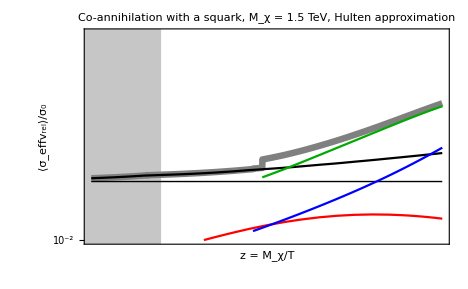

```mathematica
{xmin,xmax,ymin,ymax}={1,3,-2,3};plot5sq=Plot[Evaluate[Table[Log[10,RσvTeff[state,10^lz]],{state,Join[{"tot"},states]}]],{lz,Log[10,zmin],Log[10,zmax]},Frame->True,FrameLabel->{"z = M_χ/T","⟨σ_effv_rel⟩/σ_0"},
FrameTicks->LogLogTicks[normale],
Prolog->{If[group===SU2,{Lighter@Lighter@Pink,Rectangle[{Log[10,MDM/Tc],-4},{xmax,4}]},{}],Lighter@Lighter@Gray,Rectangle[{0,-4},{Log[10,25],4}]},
PlotLegends->Placed[Map[Style[#,Small,FontFamily->"Times"]&,Join[{"tot","tree","Som"},Bnames]],{0.3,0.75}],PlotStyle->{{Gray,Thickness[0.01]},{Black,Thin},Black,Red,Blue,DGreen,{Red,Dashed},{Blue,Dashed},{DGreen,Dashed},{Red,Dotted},{Blue,Dotted},{DGreen,Dotted},Black},PlotLabel->model<>", M_χ = "<>ToString[MDM/1000.]<>" TeV, Hulten approximation",PlotRange->{{xmin,xmax},{ymin,ymax}},Axes->False,ImageSize->400,
Epilog->If[group===SU2,{Red,Arrow[{{Log[10,MDM/Tc],ymin+0.5},{xmax,ymin+0.5}}],Text[" SU(2)_L broken ",{3,ymin+0.5},Background->Lighter@Lighter@Pink]},{}]]
```

```mathematica
Export["/Users/Andrea/Dropbox/DM bound state/figs/Squarkcross.pdf",plot5sq]
```

/Users/Andrea/Dropbox/DM bound state/figs/Squarkcross.pdf

# Triplet

### Inits

defV[{{charge of DM1 , charge of DM2 ,  spin S of DM1+DM2}}].

```mathematica
Clear[T];
defV[{{0,1,0}}]:=(Clear[r,z];dim=1;sys={{0,1,0}};V={{ΔMT[T]+ α2MZ/r  Exp[-MWT[T]r]}};);
defV[{{0,1,1}}]:=(Clear[r,z];dim=1;sys={{0,1,0}};V={{ΔMT[T]+ α2MZ/r  Exp[-MWT[T] r]}};)
defV[{{1,1,0}}]:=(Clear[r,z];dim=1;sys={{1,1,0}};V={{ 2ΔMT[T]+α2MZ/r ssWT[T]Exp[-MγT[T] r]+(α2MZ ccWT[T])/r  Exp[-MZT[T] r]}};);
defV[{{-1,1,1}}]:=(Clear[r,z];dim=1;sys={{-1,1,1}};V={{ 2ΔMT[T]-(α2MZ ccWT[T])/r  Exp[-MZT[T] r]}};);
defV[{{-1,1,0},{0,0,0}}]:=(Clear[r,z];dim=2;sys={{-1,1,0},{0,0,0}};
V={{2ΔMT[T]-(α2MZ ssWT[T])/r Exp[-MγT[T] r]- α2MZ/r ccWT[T] Exp[-MZT[T] r],-Sqrt[2] α2MZ Exp[-MWT[T] r]/r},{-Sqrt[2] α2MZ Exp[-MWT[T] r]/r,0}};);
systab={{{0,1,0}},{{0,1,1}},{{1,1,0}},{{-1,1,1}},{{-1,1,0},{0,0,0}}};
systabs=Flatten[systab,1];Clear[σ];
```

### Spectrum

```mathematica
l=0;M=MDM=Mχ=2700;Λ=6;Clear[r];
```

```mathematica
ScanSpectrumT[{{-1,1,0},{0,0,0}},13,15,0.,50.];
```

```mathematica
θsq[x_]:=If[x<0,Null,x^2]
Eb[αeff_,n_,l_,Mχ_,MV_]:= (αeff^2 Mχ)/(4 n^2)θsq[1-1.9 n^2 MV/(αeff Mχ)-1.75 n^2(MV/(αeff Mχ))^2 l(l+1)];
```

```mathematica
Clear[T]
```

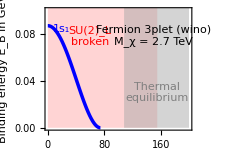

```mathematica
{xmax,ymax}={200,0.10};
ps=Flatten[Outer[List,{Thickness[0.01],Thickness[0.005]},{Blue,Red,{Red,Dashed}}],1];
EBHulten=Plot[Evaluate[Table[{Eb[λ α2MZ,1,0,Mχ,MWT[T]],Eb[λ α2MZ,2,0,Mχ,MWT[T]],Eb[λ α2MZ,2,1,Mχ,MWT[T]]},{λ,{2,1}}]],{T,0,100},Frame->True,FrameLabel->{"Temperature in GeV","Binding energy E_B in GeV","
StyleBox[\"z\",\nFontSlant->\"Italic\"] = M_χ/
StyleBox[\"T\",\nFontSlant->\"Italic\"]",""},PlotRange->{{0,xmax},{0,ymax}},
Prolog->{Opacity[0.5],Lighter@Pink,Rectangle[{0,0},{Tc,100}],Lighter@Gray,Rectangle[{xmax,0},{Mχ/25,Tc}]},
Epilog->{Blue,Gray,Text[Style["Thermal\nequilibrium",Small],{155,0.03}],Red,
Text[Style["SU(2)_L\nbroken",Small],{60,0.78 ymax}],Black,Text["Fermion 3plet (wino)\nM_χ = 2.7 TeV",{0.75xmax,0.78 ymax}],Blue,Text[" 1s_1",{T,0.01+Eb[2 α2MZ,1,0,Mχ,MWT[T]]}/.T->20]},FrameTicks->{{Automatic,Automatic},{Automatic,Table[{Mχ/z,z},{z,{15,25,50,100,300}}]}},PlotStyle->ps,ImageSize->250]
```

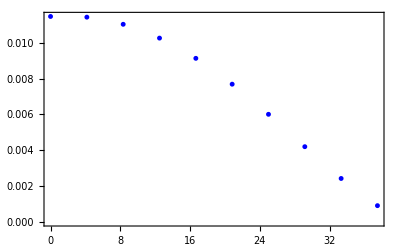

```mathematica
EBNumerics=ListPlot[Btab[1,0],Frame->True,PlotMarkers->{●,5},PlotStyle->Blue]
```

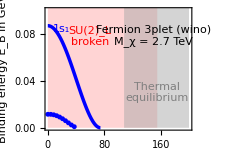

```mathematica
EBplot3=Show[EBHulten,EBNumerics]
```

```mathematica
Export["/Users/Andrea/Dropbox/DM bound state/figs/EB3a.pdf",EBplot3]
```

/Users/Andrea/Dropbox/DM bound state/figs/EB3a.pdf

# Temporary

```mathematica
θsq[x_]:=If[x<0,Null,x^2]
Eb[αeff_,n_,l_,Mχ_,MV_]:= (αeff^2 Mχ)/(4 n^2)θsq[1-1.74 n^2 MV/(αeff Mχ)-1.61 n^2(MV/(αeff Mχ))^2 l(l+1)];
```

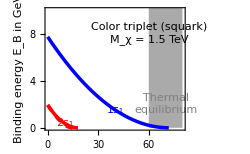

```mathematica
ps=Flatten[Outer[List,{Thickness[0.01],Thickness[0.005]},{Blue,Red,{Red,Dashed}}],1];
Mχ=1500.;xmax=80;
EBplot=Plot[Evaluate[Table[{Eb[λ α3[α3MZ Mχ],1,0,Mχ,MgT[T]],Eb[λ α3[α3MZ Mχ],2,0,Mχ,MgT[T]],Eb[λ α3[α3MZ Mχ],2,1,Mχ,MgT[T]]},{λ,{4/3}}]],{T,0,xmax},Frame->True,FrameLabel->{"Temperature in GeV","Binding energy E_B in GeV","z = M_χ/T",""},PlotRange->{{0,xmax},{0,10}},
Prolog->{Lighter@Gray,Rectangle[{xmax,0},{Mχ/25,Tc}]},
Epilog->{Gray,Text[Style["Thermal\nequilibrium",Small],{70,2}],Black,Text["Color triplet (squark)\nM_χ = 1.5 TeV",{60,8}],Blue,Text[" 1s_1",{T,Eb[4/3 α3[α3MZ Mχ],1,0,Mχ,MgT[T]]}/.T->40,Background->White],Red,Text[" 2s_1",{T,Eb[4/3 α3[α3MZ Mχ],2,0,Mχ,MgT[T]]}/.T->10,Background->White]},FrameTicks->{{Automatic,Automatic},{Automatic,Table[{Mχ/z,z},{z,{20,30,50,100,300}}]}},PlotStyle->ps,ImageSize->250]
```

```mathematica
Export["/Users/Andrea/Dropbox/DM bound state/figs/EB3c.pdf",EBplot]
```

/Users/Andrea/Dropbox/DM bound state/figs/EB3c.pdf

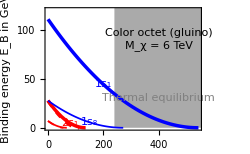

```mathematica
ps=Flatten[Outer[List,{Thickness[0.01],Thickness[0.005]},{Blue,Red,{Red,Dashed}}],1];
Mχ=6000.;xmax=600;
EBplot8=Plot[Evaluate[Table[{Eb[λ α3[α3MZ Mχ],1,0,Mχ,MgT[T]],Eb[λ α3[α3MZ Mχ],2,0,Mχ,MgT[T]],Eb[λ α3[α3MZ Mχ],2,1,Mχ,MgT[T]]},{λ,{3,3/2}}]],{T,0,xmax},Frame->True,FrameLabel->{"Temperature in GeV","Binding energy E_B in GeV","z = M_χ/T",""},PlotRange->{0,120},
Prolog->{Lighter@Gray,Rectangle[{xmax,0},{Mχ/25,200}]},
Epilog->{Gray,Text[Style["Thermal equilibrium",Small],{400,30}],Black,
Text["Color octet (gluino)\nM_χ = 6 TeV",{400,90}],Blue,Text["1s_1",{T,Eb[3 α3[α3MZ Mχ],1,0,Mχ,MgT[T]]}/.T->200,Background->White],
Text["1s_8",{T,Eb[3/2 α3[α3MZ Mχ],1,0,Mχ,MgT[T]]}/.T->150,Background->White],Red,
Text["2s_1",{T,Eb[3 α3[α3MZ Mχ],2,0,Mχ,MgT[T]]}/.T->80,Background->White]},FrameTicks->{{Automatic,Automatic},{Automatic,Table[{Mχ/z,z},{z,{10,20,30,50,200}}]}},PlotStyle->ps,ImageSize->250]
```

```mathematica
Export["/Users/Andrea/Dropbox/DM bound state/figs/EB8c.pdf",EBplot8]
```

/Users/Andrea/Dropbox/DM bound state/figs/EB8c.pdf

```mathematica
Eb[α3[α3MZ Mχ],2,1,Mχ,MgT[0]]
```

3.07293